## PCA

## Intro

```mathematica
(*ClearAll["Global`*"];*)
```

```mathematica
<<PollyModularity`
```

Modularity for Mathematica 2.0
(c) P. David Polly and A. Goswami, 20 Dec 2010
Updated 7 April 2018.

```mathematica
<<PollyPhylogenetics`
```

Phylogenetics for Mathematica 5.0
(c) P. David Polly, 21 January 2018

```mathematica
<<PollyMorphometrics`
```

PollyMorphometrics 12.2
(c) P. David Polly, 5 March 2017

```mathematica
F={"AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
FL={"BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe"};
AllTaxaList={"AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe","AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
```

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
UlnaLabels=UlnaData[[1,1;;,1]];
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
ManusData=ManusData[[1;;,1;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
ManusLabels=ManusData[[1;;,1]];
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
HumerusLabels=HumerusData[[1,1;;,1]];
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
TarsoLabels=TarsoData[[1,1;;,1]];
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
TibioLabels=TibioData[[1,1;;,1]];
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
FemurLabels=FemurData[[1,1;;,1]];
UlnaLabelsList=Table[StringSplit[UlnaLabels[[x]],"_"][[1;;2]], {x,Length[UlnaLabels]}];
ManusLabelsList=Table[StringSplit[ManusLabels[[x]],"_"][[1;;2]], {x,Length[ManusLabels]}];
HumerusLabelsList=Table[StringSplit[HumerusLabels[[x]],"_"][[1;;2]], {x,Length[HumerusLabels]}];
FemurLabelsList=Table[StringSplit[FemurLabels[[x]],"_"][[1;;2]], {x,Length[FemurLabels]}];
TibioLabelsList=Table[StringSplit[TibioLabels[[x]],"_"][[1;;2]], {x,Length[TibioLabels]}];
TarsoLabelsList=Table[StringSplit[TarsoLabels[[x]],"_"][[1;;2]], {x,Length[TarsoLabels]}];
ForeLimb=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,2]]];
HindLimb=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,2]]];
```

```mathematica
FemurVSHumerusList=Union[Intersection[HumerusLabelsList,FemurLabelsList][[1;;,2]]];
```

```mathematica
(*Clear[X];
Clear[x];
Clear[M];*)
```

```mathematica
PrincipalComponentsOfShape[proc_,PCs_,labels_]:=Module[{marginfactor,MShape,Resids,P,u,w,v,EValues,PropEValues,scores,xrange,yrange,pts,labs,InsScale},marginfactor=1.5;
MShape=Mean[proc];
Resids=#-MShape&/@proc;
P=Covariance[Resids];
{u,w,v}=SingularValueDecomposition[P];
EValues=Tr[w,List];
PropEValues=EValues/Plus@@EValues;
scores=Resids.u;
u=Transpose[u];
xrange=marginfactor*{Min[scores[[1;;,PCs[[1]]]]],Max[scores[[1;;,PCs[[1]]]]]};
yrange=marginfactor*{Min[scores[[1;;,PCs[[2]]]]],Max[scores[[1;;,PCs[[2]]]]]};
InsScale=.4*Mean[{Plus@@Abs[xrange],Plus@@Abs[yrange]}];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labelss],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labelss],#]]&/@F]];
pts1={PointSize[0.01],Blue,Point[#]}&/@scores[[flightless,PCs]];
pts2={PointSize[0.01],Orange,Point[#]}&/@scores[[flighted,PCs]];
labs=Table[{FontFamily->"Helvetica",Text[labels[[x]],scores[[x,PCs]],{-1.15,-1.15}]},{x,Length[labels]}];
Print[Graphics[{pts1, pts2,labs},Frame->True,AspectRatio->1/GoldenRatio, FrameLabel->{"PC "<>ToString[PCs[[1]]],"PC "<>ToString[PCs[[2]]]},BaseStyle->{FontFamily->"Helvetica"}]];
Print["PC "<>ToString[PCs[[1]]]<>" explains "<>ToString[PropEValues[[PCs[[1]]]]]<>" of total shape variance"];
Print["PC "<>ToString[PCs[[2]]]<>" explains "<>ToString[PropEValues[[PCs[[2]]]]]<>" of total shape variance"];
Print[PlanarGraphPlot[Partition[Mean[proc],2],ConvexHull[Partition[Mean[proc],2]],BaseStyle->{FontFamily->"Helvetica",FontSize->14},PlotLabel->"Mean Shape",AspectRatio->Automatic,ImageSize->250]];
Print[Graphics[{},Frame->True,PlotLabel->"Morphospace",FrameLabel->{"PC "<>ToString[PCs[[1]]],"PC "<>ToString[PCs[[2]]]},BaseStyle->{FontFamily->"Helvetica",FontSize->12},PlotRange->{1.5*xrange,1.5*yrange},Epilog->{Inset[tpSpline[MShape,xrange[[1]]*u[[PCs[[1]]]]+yrange[[1]]*u[[PCs[[2]]]]+MShape],{xrange[[1]],yrange[[1]]},Center,InsScale*{1,1}],Inset[tpSpline[MShape,yrange[[1]]*u[[PCs[[2]]]]+MShape],{0,yrange[[1]]},Center,InsScale*{1,1}],Inset[tpSpline[MShape,xrange[[2]]*u[[PCs[[1]]]]+yrange[[1]]*u[[PCs[[2]]]]+MShape],{xrange[[2]],yrange[[1]]},Center,InsScale*{1,1}],Inset[tpSpline[MShape,xrange[[1]]*u[[PCs[[1]]]]+yrange[[2]]*u[[PCs[[2]]]]+MShape],{xrange[[1]],yrange[[2]]},Center,InsScale*{1,1}],Inset[tpSpline[MShape,yrange[[2]]*u[[PCs[[2]]]]+MShape],{0,yrange[[2]]},Center,InsScale*{1,1}],Inset[tpSpline[MShape,xrange[[2]]*u[[PCs[[1]]]]+yrange[[2]]*u[[PCs[[2]]]]+MShape],{xrange[[2]],yrange[[2]]},Center,InsScale*{1,1}],Inset[tpSpline[MShape,xrange[[1]]*u[[PCs[[1]]]]+MShape],{xrange[[1]],0},Center,InsScale*{1,1}],Inset[tpSpline[MShape,MShape],{0,0},Center,InsScale*{1,1}],Inset[tpSpline[MShape,xrange[[2]]*u[[PCs[[1]]]]+MShape],{xrange[[2]],0},Center,InsScale*{1,1}]}]];

shortlabels=StringSplit[#,"_"][[1]]&/@labelss;
RegressionData=#&/@scores[[1;;,PCs]];
Clear[T];
lm=LinearModelFit[RegressionData,{1,T},T];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,T},T];
lmflight=LinearModelFit[RegressionData[[flighted]],{1,T},T];

xrange={((Min[scores[[1;;,PCs[[1]]]]]*-1)+0.01)*-1,Max[scores[[1;;,PCs[[1]]]]]+0.01};
yrange={((Min[scores[[1;;,PCs[[2]]]]]*-1)+0.01)*-1,Max[scores[[1;;,PCs[[2]]]]]+0.01};

Print[Show[ListPlot[{RegressionData[[flightless]],RegressionData[[flighted]]}, AspectRatio->1/GoldenRatio,Axes->False,Frame->True,PlotRange->{xrange,yrange}, PlotLegends->{"Flightless","Volant"}],Plot[lmflight[T],{T,-0.5,0.5}, PlotStyle->Orange],Plot[lmflightless[T],{T,-0.5,0.5}, PlotStyle->Blue]]];

bootdiffs=Table[bootdata=RandomSample[Transpose[{RandomSample[RegressionData[[1;;,1]]],RandomSample[RegressionData[[1;;,2]]]}]];
lmflightless=LinearModelFit[bootdata[[flightless]],{1,T},T]["BestFitParameters"][[2]];
lmflight=LinearModelFit[bootdata[[flighted]],{1,T},T]["BestFitParameters"][[2]];lmflightless-lmflight,{5000}];
Print[lmflightless=LinearModelFit[RegressionData[[flightless]],{1,T},T]["BestFitParameters"][[2]]];
Print[lmflight=LinearModelFit[RegressionData[[flighted]],{1,T},T]["BestFitParameters"][[2]]];
Print[lmflightless-lmflight];
Print[Show[Histogram[bootdiffs],Graphics[Line[{{lmflightless-lmflight,0},{lmflightless-lmflight,100}}]]]];
Print[N[Length[Select[bootdiffs,#≥lmflight-lmflightless&]]/5000]];
Return[];]
```

## Tarso

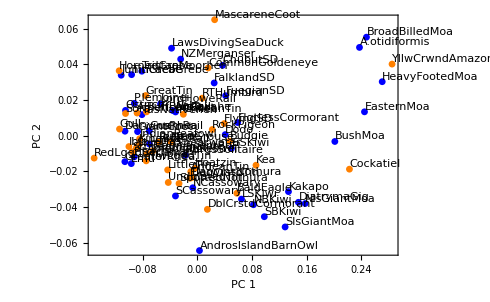

PC 1 explains 0.811937 of total shape variance

PC 2 explains 0.0546263 of total shape variance

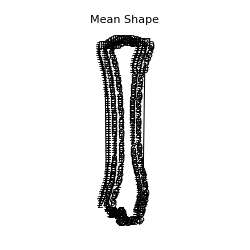

-Graphics-

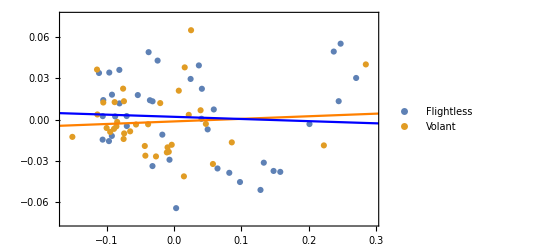

-0.0157228

0.018727

-0.0344498

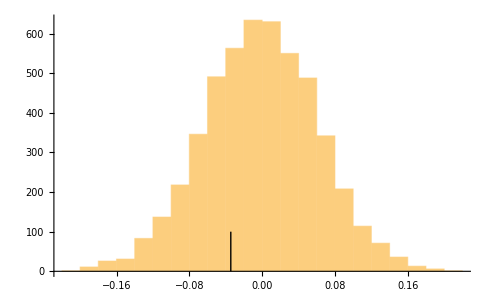

0.2832

```mathematica
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=TarsoData[[1,1;;,2;;]];
outline=TarsoData[[2,1;;,2;;]];
labels=TarsoData[[1,1;;,1]];
labelss=labels;
TarsoLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{12,19,79,20,70}]],{M,Length[outline]}];
(*Table[Graphics[{{Gray,Point[Partition[brokeoutlines[[M]],2]]},{Red,PointSize[0.1],Point[brokeoutlines[[M,{1,2}]]]},{Blue,PointSize[0.1],Point[Partition[landmarks[[M]],2]]}}],{M,Length[brokeoutlines]}];*)
Union[StringSplit[#,"_"][[1]]&/@labels];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TarsoProc=Procrustes[means2, 200, 2];
PrincipalComponentsOfShape[TarsoProc,{1,2}, Union[shortlabels]]
(*Speak["PCA for tarso is finished"]*)
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
flightless=TarsoProc[[flightless]];
flighted=TarsoProc[[flighted]];
CovFlightless=Covariance[flightless];
CovFlighted=Covariance[flighted];

TarsoPos=Flatten[Position[TarsoLabelsList,#]]&/@HindLimb;
TarsoPos=TarsoPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@TarsoPos;
Tarsolabelsfew=TarsoLabels[[#]]&/@TarsoPos;
shortTarsoLabels=StringSplit[#,"_"][[1]]&/@Tarsolabelsfew;
pos=Flatten[Position[shortTarsoLabels,#]]&/@Union[shortTarsoLabels];

(*shortPos=Flatten[Position[TarsoLabelsList,#]]&/@HindLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=TarsoLabels[[#]]&/@shortPos;
shortLabels=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels,#]]&/@Union[shortLabels];*)
means2=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
TarsoProc=Procrustes[means2, 200, 2];
TarsoProc=Table[Prepend[TarsoProc[[x]],Union[shortTarsoLabels][[x]]],{x,Length[TarsoProc]}];
```

```mathematica
(*Timing[MantelForMorphometrics[CovFlightless,CovFlighted,10000]]
Speak["Mantel for tarso is finished"]*)
```

{783.681,{0.91784,0.}}

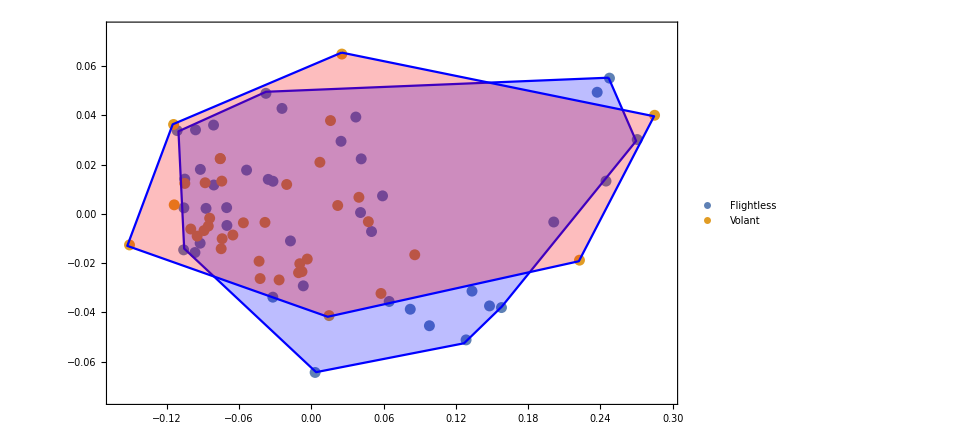

## Tibia

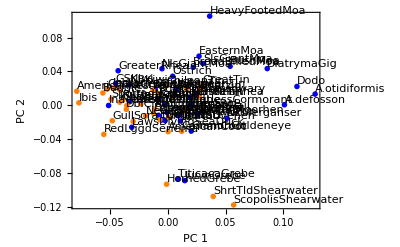

PC 1 explains 0.433011 of total shape variance

PC 2 explains 0.353113 of total shape variance

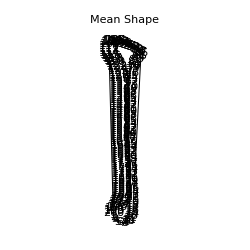

-Graphics-

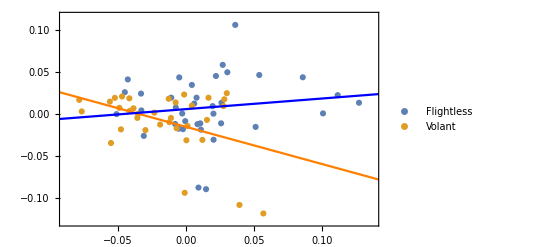

0.125543

-0.440554

0.566097

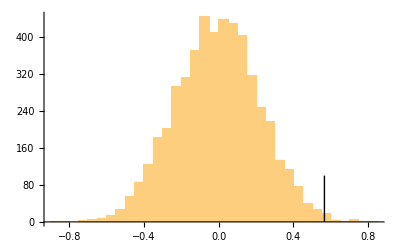

0.9944

```mathematica
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=TibioData[[1,1;;,2;;]];
outline=TibioData[[2,1;;,2;;]];
labels=TibioData[[1,1;;,1]];
labelss=labels;
TibioLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{85,20,95}]],{M,Length[outline]}];
(*Table[Graphics[{{Gray,Point[Partition[brokeoutlines[[M]],2]]},{Red,PointSize[0.1],Point[brokeoutlines[[M,{1,2}]]]},{Blue,PointSize[0.1],Point[Partition[landmarks[[M]],2]]}}],{M,Length[brokeoutlines]}];*)
Union[StringSplit[#,"_"][[1]]&/@labels];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TibioProc=Procrustes[means2, 200, 2];
PrincipalComponentsOfShape[TibioProc,{1,2}, Union[shortlabels]]
Speak["PCA for tibia is finished"]
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
flightless=TibioProc[[flightless]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
flighted=TibioProc[[flighted]];
CovFlightless=Covariance[flightless];
CovFlighted=Covariance[flighted];

TibioPos=Flatten[Position[TibioLabelsList,#]]&/@HindLimb;
TibioPos=TibioPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@TibioPos;
Tibiolabelsfew=TibioLabels[[#]]&/@TibioPos;
shortTibioLabels=StringSplit[#,"_"][[1]]&/@Tibiolabelsfew;
pos=Flatten[Position[shortTibioLabels,#]]&/@Union[shortTibioLabels];

(*shortPos=Flatten[Position[TibioLabelsList,#]]&/@HindLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=TibioLabels[[#]]&/@shortPos;
shortLabels=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels,#]]&/@Union[shortLabels];*)
means2=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
TibioProc=Procrustes[means2, 200, 2];
TibioProc=Table[Prepend[TibioProc[[x]],Union[shortTibioLabels][[x]]],{x,Length[TibioProc]}];
```

```mathematica
(*Timing[MantelForMorphometrics[CovFlightless,CovFlighted,10000]]
Speak["Mantel for tibia is finished"]*)
```

{320.629,{0.770297,0.}}

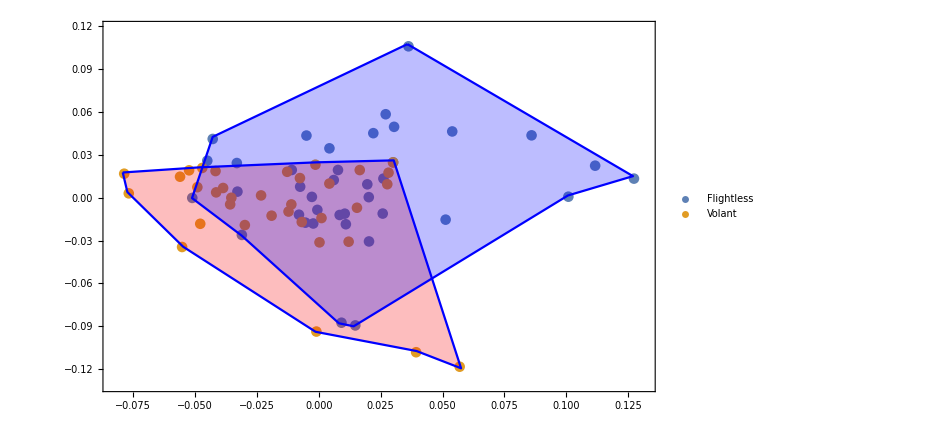

## Femur

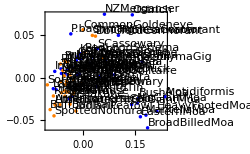

PC 1 explains 0.764979 of total shape variance

PC 2 explains 0.0905274 of total shape variance

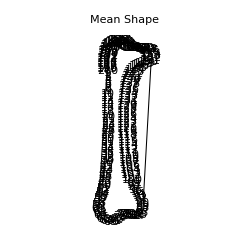

-Graphics-

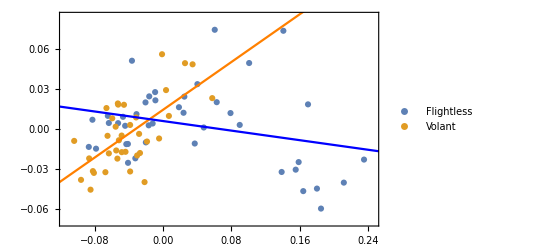

-0.0896873

0.447732

-0.537419

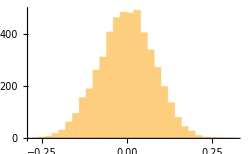

0.

```mathematica
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=FemurData[[1,1;;,2;;]];
outline=FemurData[[2,1;;,2;;]];
labels=FemurData[[1,1;;,1]];
labelss=labels;
FemurLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{69,8,6,69,25, 23}]],{M,Length[outline]}];
(*Table[Graphics[{{Gray,Point[Partition[brokeoutlines[[M]],2]]},{Red,PointSize[0.1],Point[brokeoutlines[[M,{1,2}]]]},{Blue,PointSize[0.1],Point[Partition[landmarks[[M]],2]]}}],{M,Length[brokeoutlines]}];*)
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
FemurProc=Procrustes[means2, 200, 2];
PrincipalComponentsOfShape[FemurProc,{1,2}, Union[shortlabels]]
Speak["PCA for femur is finished"]
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
flightless=FemurProc[[flightless]];
flighted=FemurProc[[flighted]];
CovFlightless=Covariance[flightless];
CovFlighted=Covariance[flighted];

FemurPos=Flatten[Position[FemurLabelsList,#]]&/@HindLimb;
FemurPos=FemurPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@FemurPos;
Femurlabelsfew=FemurLabels[[#]]&/@FemurPos;
shortFemurLabels=StringSplit[#,"_"][[1]]&/@Femurlabelsfew;
pos=Flatten[Position[shortFemurLabels,#]]&/@Union[shortFemurLabels];


(*shortPos=Flatten[Position[FemurLabelsList,#]]&/@HindLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=FemurLabels[[#]]&/@shortPos;
shortLabels=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels,#]]&/@Union[shortLabels];*)
means2=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
FemurProc=Procrustes[means2, 200, 2];
FemurProc=Table[Prepend[FemurProc[[x]],Union[shortFemurLabels][[x]]],{x,Length[FemurProc]}];
```

```mathematica
(*Timing[MantelForMorphometrics[CovFlightless,CovFlighted,10000]]
Speak["Mantel for tibia is finished"]*)
```

{327.615,{0.703473,0.}}

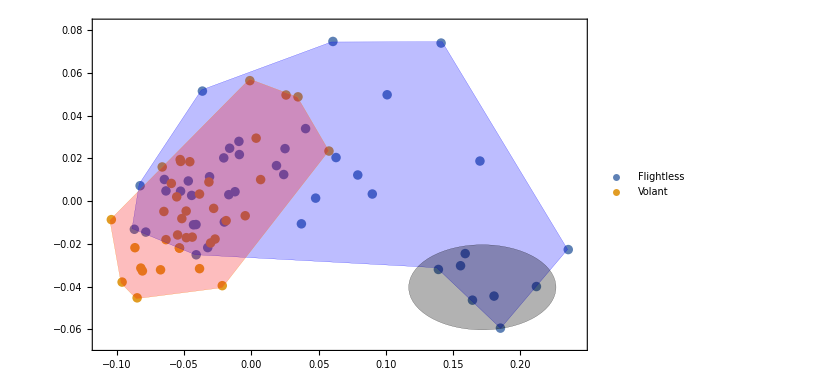

## Humerus

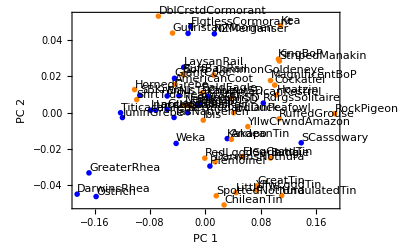

PC 1 explains 0.762941 of total shape variance

PC 2 explains 0.0833326 of total shape variance

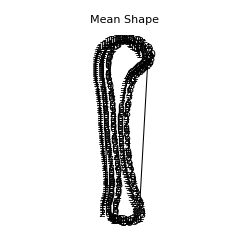

-Graphics-

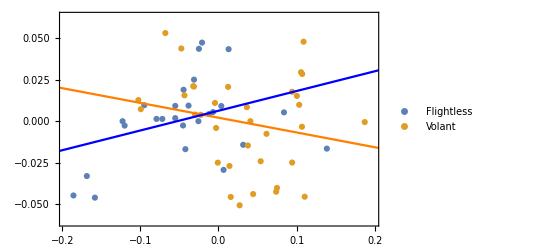

0.118911

-0.0889522

0.207863

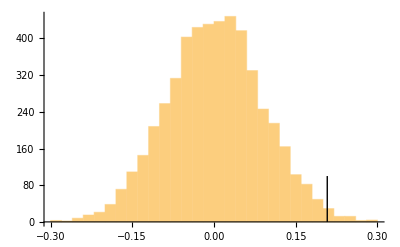

0.992

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
labelss=labels;
HumerusLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
(*Table[Graphics[{{Gray,Point[Partition[brokeoutlines[[x]],2]]},{Red,PointSize[0.1],Point[brokeoutlines[[x,{1,2}]]]},{Blue,PointSize[0.1],Point[Partition[landmarks[[x]],2]]}}],{x,Length[brokeoutlines]}];*)
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
HumerusProc=Procrustes[means2, 200, 2];
PrincipalComponentsOfShape[HumerusProc,{1,2}, Union[shortlabels]]
Speak["PCA for humerus is finished"]
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
flightless=HumerusProc[[flightless]];
flighted=HumerusProc[[flighted]];
CovFlightless=Covariance[flightless];
CovFlighted=Covariance[flighted];
(*shortPos=Flatten[Position[HumerusLabelsList,#]]&/@ForeLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;*)

HumerusPos=Flatten[Position[HumerusLabelsList,#]]&/@ForeLimb;
HumerusPos=HumerusPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@HumerusPos;
Humeruslabelsfew=HumerusLabels[[#]]&/@HumerusPos;
shortHumerusLabels=StringSplit[#,"_"][[1]]&/@Humeruslabelsfew;
pos=Flatten[Position[shortHumerusLabels,#]]&/@Union[shortHumerusLabels];

(*labelsfew=HumerusLabels[[#]]&/@shortPos;
shortLabels=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels,#]]&/@Union[shortLabels];*)
means2=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
HumerusProc=Procrustes[means2, 200, 2];
HumerusProc=Table[Prepend[HumerusProc[[x]],Union[shortHumerusLabels][[x]]],{x,Length[HumerusProc]}];
```

```mathematica
(*Timing[MantelForMorphometrics[CovFlightless,CovFlighted,10000]]
Speak["Mantel for humerus is finished"]*)
```

{329.165,{0.91539,0.}}

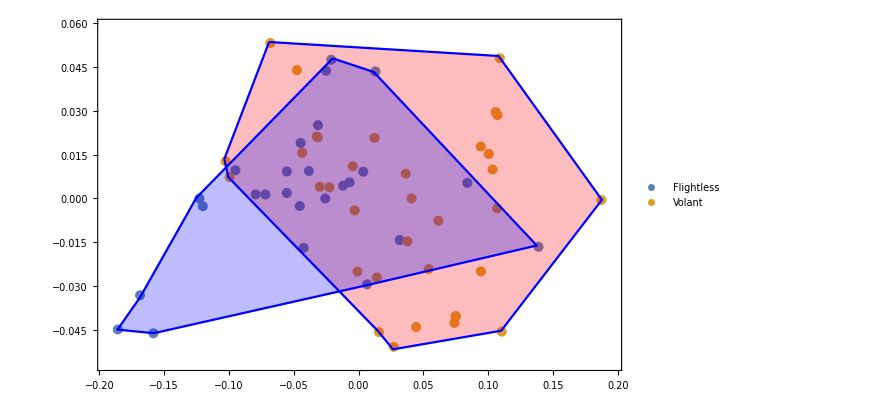

## Ulna

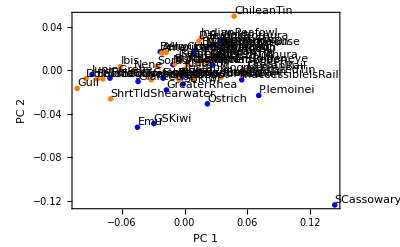

PC 1 explains 0.635052 of total shape variance

PC 2 explains 0.182178 of total shape variance

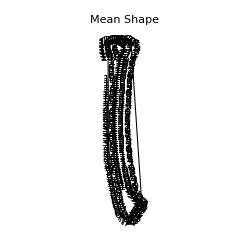

-Graphics-

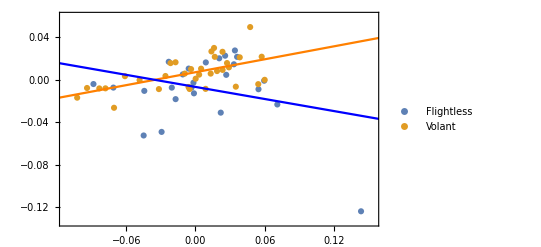

-0.18948

0.20302

-0.3925

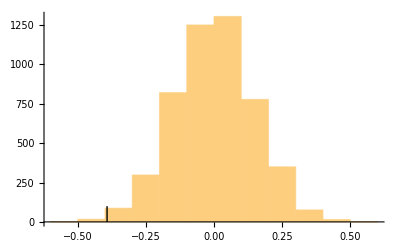

0.0042

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=UlnaData[[1,1;;,2;;]];
outline=UlnaData[[2,1;;,2;;]];
labels=UlnaData[[1,1;;,1]];
labelss=labels;
UlnaLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{73,14,89,12,12}]],{x,Length[outline]}];
(*Table[Graphics[{{Gray,Point[Partition[brokeoutlines[[x]],2]]},{Red,PointSize[0.1],Point[brokeoutlines[[x,{1,2}]]]},{Blue,PointSize[0.1],Point[Partition[landmarks[[x]],2]]}}],{x,Length[brokeoutlines]}];*)
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
Dimensions[means2];
UlnaProc=Procrustes[means2, 200, 2];
PrincipalComponentsOfShape[UlnaProc,{1,2}, Union[shortlabels]]
Speak["PCA for ulna is finished"]
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
flightless=UlnaProc[[flightless]];
flighted=UlnaProc[[flighted]];
CovFlightless=Covariance[flightless];
CovFlighted=Covariance[flighted];
UlnaPos=Flatten[Position[UlnaLabelsList,#]]&/@ForeLimb;
UlnaPos=UlnaPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@UlnaPos;
Ulnalabelsfew=UlnaLabels[[#]]&/@UlnaPos;
shortUlnaLabels=StringSplit[#,"_"][[1]]&/@Ulnalabelsfew;
pos=Flatten[Position[shortUlnaLabels,#]]&/@Union[shortUlnaLabels];
means2=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
UlnaProc=Procrustes[means2, 200, 2];
UlnaProc=Table[Prepend[UlnaProc[[x]],Union[shortUlnaLabels][[x]]],{x,Length[UlnaProc]}];
```

```mathematica
(*Timing[MantelForMorphometrics[CovFlightless,CovFlighted,10000]]
Speak["Mantel for ulna is finished"]*)
```

{324.184,{0.825455,0.}}

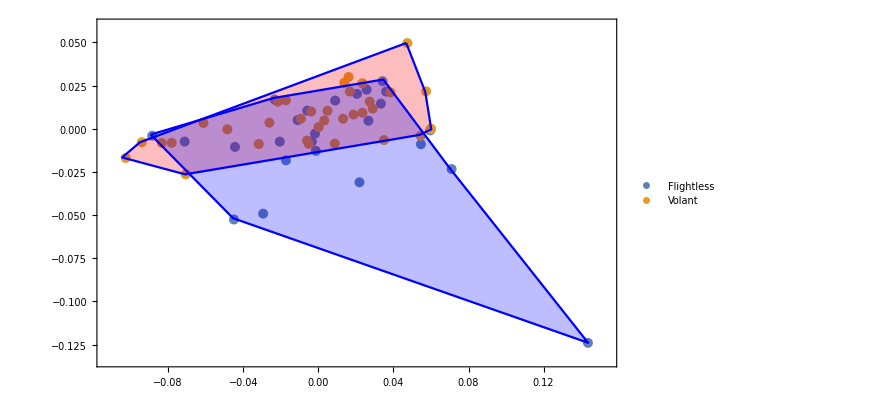

## Manus

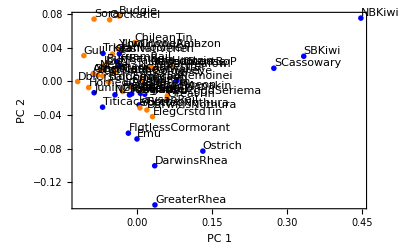

PC 1 explains 0.696838 of total shape variance

PC 2 explains 0.116401 of total shape variance

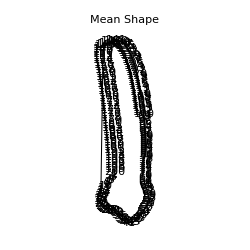

-Graphics-

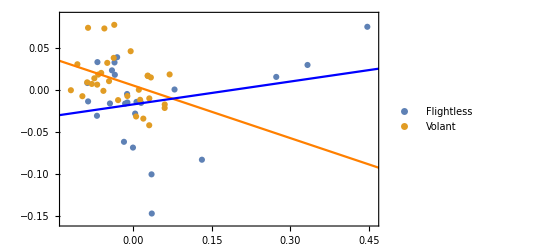

0.0908857

-0.209172

0.300057

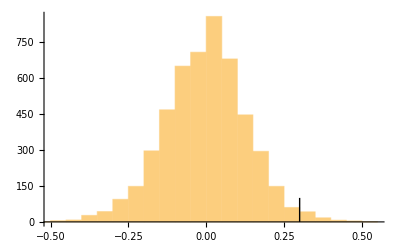

0.983

```mathematica
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=ManusData[[1;;,1]];
labelss=labels;
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusLabels=labels;
outline= ManusData[[1;;,2;;]];
lands=Table[Partition[outline[[x]],2][[{Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Min[Partition[outline[[x]],2][[1;;,2]]]]][[1]],Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Max[Partition[outline[[x]],2][[1;;,2]]]]][[1]]}]],{x,Length[outline]}];
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],lands[[x]],{40,100,60}]],{x,Length[outline]}];(*Table[Graphics[{{Gray,Point[Partition[brokeoutlines[[x]],2]]},{Red,PointSize[0.1],Point[brokeoutlines[[x,{1,2}]]]},{Blue,PointSize[0.1],Point[Partition[lands[[x]],2]]}}],{x,Length[brokeoutlines]}];*)
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means1=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
ManusProc=Procrustes[means1, 200, 2];
PrincipalComponentsOfShape[ManusProc,{1,2}, Union[shortlabels]]
Speak["PCA for Manus is finished"]
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
flightless=ManusProc[[flightless]];
flighted=ManusProc[[flighted]];
CovFlightless=Covariance[flightless];
CovFlighted=Covariance[flighted];

ManusPos=Flatten[Position[ManusLabelsList,#]]&/@ForeLimb;
ManusPos=ManusPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@ManusPos;
Manuslabelsfew=ManusLabels[[#]]&/@ManusPos;
shortManusLabels=StringSplit[#,"_"][[1]]&/@Manuslabelsfew;
pos=Flatten[Position[shortManusLabels,#]]&/@Union[shortManusLabels];

(*shortPos=Flatten[Position[ManusLabelsList,#]]&/@ForeLimb;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=ManusLabels[[#]]&/@shortPos;
shortLabels=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels,#]]&/@Union[shortLabels];*)
means2=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
ManusProc=Procrustes[means2, 200, 2];
ManusProc=Table[Prepend[ManusProc[[x]],Union[shortManusLabels][[x]]],{x,Length[ManusProc]}];
```

```mathematica
(*Timing[MantelForMorphometrics[CovFlightless,CovFlighted,10000]]
Speak["Mantel for Manus is finished"]*)
```

{332.547,{0.664021,0.}}

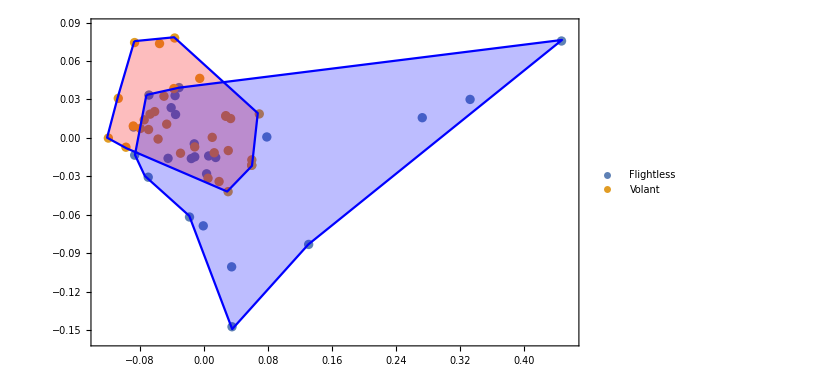

## CPCA

## Tarso

### Intro

```mathematica
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=TarsoData[[1,1;;,2;;]];
outline=TarsoData[[2,1;;,2;;]];
labels=TarsoData[[1,1;;,1]];
labelss=TarsoData[[1,1;;,1]];
TarsoLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{12,19,79,20,70}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TarsoProc=Procrustes[means2, 200, 2];
Consensus=Mean[TarsoProc];
residss=#-Consensus&/@TarsoProc;
P=Covariance[TarsoProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=residss.vectors;
scores=scores[[1;;,1;;75]];
scores=scores*1000;
```

```mathematica
Dimensions[residss.vectors]
```

{76,400}

```mathematica
AllLabels=Union[shortlabels];
X=1;
Table[Table[If[AllLabels[[i]]==F[[j]],AllLabels[[i]]="flight"],{j,Length[F]}];
Table[If[AllLabels[[i]]==FL[[k]],AllLabels[[i]]="flightless"],{k,Length[FL]}];
,{i,Length[AllLabels]}];

FlyList=AllLabels;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/TarsoAllTaxa_NoGeneric_Scores.csv",scores,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/TarsoAllTaxa_NoGeneric_labels.csv",FlyList,"CSV"];
```

### After R

```mathematica
CPCAloadings1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarso_results.csv"];
(*CPCAloadings=CPCAloadings1[[2;;,2;;]]/1000;
CPCAloadings=Prepend[{Prepend[CPCAloadings[[1]],"flighted"],Prepend[CPCAloadings[[2]],"flightless"]},CPCAloadings1[[1]]];*)

CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarso_exp-var.csv"];

CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarso_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Tarsoexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 80.1143 | 5.18519 | 0.599901 | 2.84654 | 0.935643 | 3.48448 | 1.80702 | 0.829364 | 0.360223 | 0.80662
flightless | 78.6125 | 5.70861 | 7.98731 | 1.40289 | 1.93466 | 0.639464 | 0.616959 | 0.596321 | 0.750544 | 0.232416)

```mathematica
Tarsolambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Tarsoloadings=CPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*Tarsocpc={
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,3]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,4]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]};*)
```

### EV to CPCA comparison

```mathematica
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@F]]]];
landmarks=TarsoData[[1,1;;,2;;]];
outline=TarsoData[[2,1;;,2;;]];
labels=TarsoData[[1,1;;,1]];
labelss=TarsoData[[1,1;;,1]];
TarsoLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{12,19,79,20,70}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TarsoProc=Procrustes[means2, 200, 2];
Consensus=Mean[TarsoProc];
residss=#-Consensus&/@TarsoProc;
P=Covariance[TarsoProc];
{vectors,values, w}=SingularValueDecomposition[P];
Fvalues=values;
fEV=Eigenvalues[Fvalues];
```

```mathematica
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@FL]]]];
landmarks=TarsoData[[1,1;;,2;;]];
outline=TarsoData[[2,1;;,2;;]];
labels=TarsoData[[1,1;;,1]];
labelss=TarsoData[[1,1;;,1]];
TarsoLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{12,19,79,20,70}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TarsoProc=Procrustes[means2, 200, 2];
Consensus=Mean[TarsoProc];
residss=#-Consensus&/@TarsoProc;
P=Covariance[TarsoProc];
{vectors,values, w}=SingularValueDecomposition[P];
FLvalues=values;
flEV=Eigenvalues[FLvalues];
```

```mathematica
EVcpcaTarso={AccountingForm[CPCAlambda[[2,2;;11]],11],fEV[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],flEV[[1;;10]]};
EVcpcaTarso
```

{{0.007890164,0.00051067,0.000059082,0.000280345,0.000092148,0.000343173,0.000177967,0.000081681,0.000035477,0.000079441},{0.00815292,0.000579766,0.000358598,0.000276337,0.000179486,0.000146566,0.000107503,0.0000738276,0.0000491388,0.0000443675},{0.011956779,0.000868267,0.001214852,0.000213376,0.000294257,0.000097261,0.000093838,0.000090699,0.000114156,0.00003535},{0.0131216,0.000971687,0.000469764,0.00023916,0.000189602,0.000141704,0.00011073,0.0000860225,0.0000741554,0.0000457331}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.0383376

```mathematica
VectorAngle[CPCAlambda[[2,3;;6]],flEV[[1;;5]]]
```

VectorAngle::length: The vectors {0.00051067,0.000059082,0.000280345,0.000092148} and {0.0131216,0.000971687,0.000469764,0.00023916,0.000189602} have different lengths.

VectorAngle[{0.00051067,0.000059082,0.000280345,0.000092148},{0.0131216,0.000971687,0.000469764,0.00023916,0.000189602}]

## Tibia

### Intro

```mathematica
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=TibioData[[1,1;;,2;;]];
outline=TibioData[[2,1;;,2;;]];
labels=TibioData[[1,1;;,1]];
labelss=TibioData[[1,1;;,1]];
TibioLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{85,20,95}]],{M,Length[outline]}];
Union[StringSplit[#,"_"][[1]]&/@labels];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TibioProc=Procrustes[means2, 200, 2];
Consensus=Mean[TibioProc];
residss=#-Consensus&/@TibioProc;
P=Covariance[TibioProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=residss.vectors;
scores=scores[[1;;,1;;70]];
```

```mathematica
scores=scores*1000;
```

```mathematica
Dimensions[residss.vectors]
```

{71,400}

```mathematica
AllLabels=Union[shortlabels];
X=1;
Table[Table[If[AllLabels[[i]]==F[[j]],AllLabels[[i]]="flight"],{j,Length[F]}];
Table[If[AllLabels[[i]]==FL[[k]],AllLabels[[i]]="flightless"],{k,Length[FL]}];
,{i,Length[AllLabels]}];
FlyList=AllLabels;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/TibiaAllTaxa_NoGeneric_Scores.csv",scores,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/TibiaAllTaxa_NoGeneric_labels.csv",FlyList,"CSV"];
```

### After R

```mathematica
CPCAloadings1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTibia_results.csv"];
(*CPCAloadings=CPCAloadings1[[2;;,2;;]]/1000;
CPCAloadings=Prepend[{Prepend[CPCAloadings[[1]],"flighted"],Prepend[CPCAloadings[[2]],"flightless"]},CPCAloadings1[[1]]];*)

CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTibia_exp-var.csv"];

CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTibia_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Tibioexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 27.5375 | 56.4466 | 4.10616 | 1.4006 | 3.61396 | 1.69163 | 1.08904 | 0.623592 | 0.388796 | 0.755836
flightless | 41.3028 | 28.6396 | 8.74691 | 11.735 | 2.35837 | 2.00467 | 1.22324 | 0.79737 | 0.459716 | 0.0791263)

```mathematica
Tibiolambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Tibioloadings=CPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*Tibiacpc={
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,3]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]};*)
```

### EV to CPCA comparison

```mathematica
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@F]]]];
landmarks=TibioData[[1,1;;,2;;]];
outline=TibioData[[2,1;;,2;;]];
labels=TibioData[[1,1;;,1]];
labelss=TibioData[[1,1;;,1]];
TibioLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{85,20,95}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TibioProc=Procrustes[means2, 200, 2];
Consensus=Mean[TibioProc];
residss=#-Consensus&/@TibioProc;
P=Covariance[TibioProc];
{vectors,values, w}=SingularValueDecomposition[P];
Fvalues=values;
fEV=Eigenvalues[Fvalues];
```

```mathematica
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@FL]]]];
landmarks=TibioData[[1,1;;,2;;]];
outline=TibioData[[2,1;;,2;;]];
labels=TibioData[[1,1;;,1]];
labelss=TibioData[[1,1;;,1]];
TibioLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{85,20,95}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
TibioProc=Procrustes[means2, 200, 2];
Consensus=Mean[TibioProc];
residss=#-Consensus&/@TibioProc;
P=Covariance[TibioProc];
{vectors,values, w}=SingularValueDecomposition[P];
FLvalues=values;
flEV=Eigenvalues[FLvalues];
```

```mathematica
EVcpcaTibio={AccountingForm[CPCAlambda[[2,2;;11]],11],fEV[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],flEV[[1;;10]]};
EVcpcaTibio
```

{{0.000805027,0.001650154,0.000120039,0.000040945,0.00010565,0.000049453,0.000031837,0.00001823,0.000011366,0.000022096},{0.00171557,0.000835156,0.00015329,0.0000905852,0.0000627839,0.0000449991,0.0000269266,0.0000199602,0.0000126983,0.000010262},{0.001548733,0.001073899,0.000327983,0.000440028,0.000088432,0.000075169,0.000045868,0.000029899,0.000017238,0.000002967},{0.00178609,0.00129732,0.000315934,0.000123951,0.000100061,0.0000671848,0.0000418528,0.0000287598,0.0000192162,0.0000129224}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.661998

```mathematica
VectorAngle[CPCAlambda[[2,3;;6]],flEV[[1;;5]]]
```

VectorAngle::length: The vectors {0.00165015,0.000120039,0.000040945,0.00010565} and {0.00178609,0.00129732,0.000315934,0.000123951,0.000100061} have different lengths.

VectorAngle[{0.00165015,0.000120039,0.000040945,0.00010565},{0.00178609,0.00129732,0.000315934,0.000123951,0.000100061}]

## Femur

### Intro

```mathematica
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=FemurData[[1,1;;,2;;]];
outline=FemurData[[2,1;;,2;;]];
labels=FemurData[[1,1;;,1]];
labelss=FemurData[[1,1;;,1]];
FemurLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{69,8,6,69,25, 23}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
FemurProc=Procrustes[means2, 200, 2];
Consensus=Mean[FemurProc];
residss=#-Consensus&/@FemurProc;
P=Covariance[FemurProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=residss.vectors;
scores=scores[[1;;,1;;77]];
```

```mathematica
scores=scores*1000;
```

```mathematica
Dimensions[residss.vectors]
```

{78,400}

```mathematica
AllLabels=Union[shortlabels];
X=1;
Table[Table[If[AllLabels[[i]]==F[[j]],AllLabels[[i]]="flight"],{j,Length[F]}];
Table[If[AllLabels[[i]]==FL[[k]],AllLabels[[i]]="flightless"],{k,Length[FL]}];
,{i,Length[AllLabels]}];

FlyList=AllLabels;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/FemurAllTaxa_NoGeneric_Scores.csv",scores,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/FemurAllTaxa_NoGeneric_labels.csv",FlyList,"CSV"];
```

### After R

```mathematica
CPCAloadings1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaFemur_results.csv"];
(*CPCAloadings=CPCAloadings1[[2;;,2;;]]/1000;
CPCAloadings=Prepend[{Prepend[CPCAloadings[[1]],"flighted"],Prepend[CPCAloadings[[2]],"flightless"]},CPCAloadings1[[1]]];*)

CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaFemur_exp-var.csv"];

CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaFemur_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Femurexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 40.9205 | 23.94 | 7.7714 | 12.6804 | 3.27421 | 3.47406 | 0.800556 | 1.93238 | 0.983797 | 0.270635
flightless | 79.7174 | 7.39258 | 3.58946 | 2.03072 | 2.09054 | 0.922687 | 1.10444 | 0.451051 | 0.557485 | 0.457074)

```mathematica
Femurlambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Femurloadings=CPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*Femurcpc={
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,3]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]};*)
```

### EV to CPCA comparison

```mathematica
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@F]]]];
landmarks=FemurData[[1,1;;,2;;]];
outline=FemurData[[2,1;;,2;;]];
labels=FemurData[[1,1;;,1]];
labelss=FemurData[[1,1;;,1]];
FemurLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{69,8,6,69,25, 23}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
FemurProc=Procrustes[means2, 200, 2];
Consensus=Mean[FemurProc];
residss=#-Consensus&/@FemurProc;
P=Covariance[FemurProc];
{vectors,values, w}=SingularValueDecomposition[P];
Fvalues=values;
fEV=Eigenvalues[Fvalues];
```

```mathematica
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@FL]]]];
landmarks=FemurData[[1,1;;,2;;]];
outline=FemurData[[2,1;;,2;;]];
labels=FemurData[[1,1;;,1]];
labelss=FemurData[[1,1;;,1]];
FemurLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{69,8,6,69,25, 23}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
FemurProc=Procrustes[means2, 200, 2];
Consensus=Mean[FemurProc];
residss=#-Consensus&/@FemurProc;
P=Covariance[FemurProc];
{vectors,values, w}=SingularValueDecomposition[P];
FLvalues=values;
flEV=Eigenvalues[FLvalues];
```

```mathematica
EVcpcaFemur={AccountingForm[CPCAlambda[[2,2;;11]],11],fEV[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],flEV[[1;;10]]};
EVcpcaFemur
```

{{0.001229573,0.000719345,0.000233514,0.000381019,0.000098383,0.000104388,0.000024055,0.000058064,0.000029561,0.000008132},{0.00172272,0.000379372,0.000347064,0.000239764,0.000135053,0.0000800458,0.0000342439,0.0000278999,0.0000240078,0.0000216354},{0.00827182,0.000767086,0.000372458,0.000210716,0.000216923,0.000095742,0.000114601,0.000046803,0.000057847,0.000047428},{0.00849691,0.000824978,0.000409,0.000260672,0.000165024,0.000104998,0.0000828113,0.0000608746,0.0000484672,0.0000456864}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.32731

```mathematica
VectorAngle[CPCAlambda[[2,3;;6]],flEV[[1;;5]]]
```

VectorAngle::length: The vectors {0.000719345,0.000233514,0.000381019,0.000098383} and {0.00849691,0.000824978,0.000409,0.000260672,0.000165024} have different lengths.

VectorAngle[{0.000719345,0.000233514,0.000381019,0.000098383},{0.00849691,0.000824978,0.000409,0.000260672,0.000165024}]

## Humerus

### Intro

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
labelss=HumerusData[[1,1;;,1]];
HumerusLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
HumerusProc=Procrustes[means2, 200, 2];
Consensus=Mean[HumerusProc];
residss=#-Consensus&/@HumerusProc;
P=Covariance[HumerusProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=residss.vectors;
scores=scores[[1;;,1;;59]];
```

```mathematica
scores=scores*1000;
```

```mathematica
Dimensions[residss.vectors]
```

{60,400}

```mathematica
AllLabels=Union[shortlabels];
X=1;
Table[Table[If[AllLabels[[i]]==F[[j]],AllLabels[[i]]="flight"],{j,Length[F]}];
Table[If[AllLabels[[i]]==FL[[k]],AllLabels[[i]]="flightless"],{k,Length[FL]}];
,{i,Length[AllLabels]}];

FlyList=AllLabels;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/HumerusAllTaxa_NoGeneric_Scores.csv",scores,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/HumerusAllTaxa_NoGeneric_labels.csv",FlyList,"CSV"];
```

### After R

```mathematica
CPCAloadings1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerus_results.csv"];
(*CPCAloadings=CPCAloadings1[[2;;,2;;]]/1000;
CPCAloadings=Prepend[{Prepend[CPCAloadings[[1]],"flighted"],Prepend[CPCAloadings[[2]],"flightless"]},CPCAloadings1[[1]]];*)

CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerus_exp-var.csv"];

CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerus_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Humerusexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 68.4705 | 13.4728 | 2.81139 | 4.5466 | 2.80468 | 1.11483 | 0.369684 | 0.886474 | 0.450499 | 0.172679
flightless | 74.8222 | 3.21101 | 9.91727 | 1.56683 | 4.14368 | 2.00899 | 1.65135 | 0.251832 | 0.654677 | 0.668406)

```mathematica
Humeruslambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Humerusloadings=CPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*Humeruscpc={x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,3]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,4]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]}*)
```

### EV to CPCA comparison

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@F]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
labelss=HumerusData[[1,1;;,1]];
HumerusLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
HumerusProc=Procrustes[means2, 200, 2];
Consensus=Mean[HumerusProc];
residss=#-Consensus&/@HumerusProc;
P=Covariance[HumerusProc];
{vectors,values, w}=SingularValueDecomposition[P];
Fvalues=values;
fEV=Eigenvalues[Fvalues];
```

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@FL]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
labelss=HumerusData[[1,1;;,1]];
HumerusLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
HumerusProc=Procrustes[means2, 200, 2];
Consensus=Mean[HumerusProc];
residss=#-Consensus&/@HumerusProc;
P=Covariance[HumerusProc];
{vectors,values, w}=SingularValueDecomposition[P];
FLvalues=values;
flEV=Eigenvalues[FLvalues];
```

```mathematica
EVcpcaHumerus={AccountingForm[CPCAlambda[[2,2;;11]],11],fEV[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],flEV[[1;;10]]};
EVcpcaHumerus
```

{{0.004393823,0.000864563,0.00018041,0.00029176,0.000179979,0.00007154,0.000023723,0.000056886,0.000028909,0.000011081},{0.00470461,0.00084368,0.000333692,0.000248186,0.000160741,0.0000940182,0.0000495434,0.0000423755,0.0000386253,0.000021704},{0.005183108,0.000222434,0.000686992,0.000108538,0.000287042,0.000139167,0.000114393,0.000017445,0.000045351,0.000046302},{0.00546956,0.00072994,0.000344844,0.0002098,0.000170613,0.0000872272,0.0000584053,0.0000397653,0.0000312359,0.0000147155}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.0369091

```mathematica
VectorAngle[CPCAlambda[[2,3;;6]],flEV[[1;;5]]]
```

VectorAngle::length: The vectors {0.000864563,0.00018041,0.00029176,0.000179979} and {0.00546956,0.00072994,0.000344844,0.0002098,0.000170613} have different lengths.

VectorAngle[{0.000864563,0.00018041,0.00029176,0.000179979},{0.00546956,0.00072994,0.000344844,0.0002098,0.000170613}]

## Ulna

### Intro

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=UlnaData[[1,1;;,2;;]];
outline=UlnaData[[2,1;;,2;;]];
labels=UlnaData[[1,1;;,1]];
labelss=UlnaData[[1,1;;,1]];
UlnaLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{73,14,89,12,12}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
Dimensions[means2];
UlnaProc=Procrustes[means2, 200, 2];
Consensus=Mean[UlnaProc];
residss=#-Consensus&/@UlnaProc;
P=Covariance[UlnaProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=residss.vectors;
scores=scores[[1;;,1;;59]];
```

```mathematica
scores=scores*1000;
```

```mathematica
Dimensions[residss.vectors]
```

{60,400}

```mathematica
AllLabels=Union[shortlabels];
X=1;
Table[Table[If[AllLabels[[i]]==F[[j]],AllLabels[[i]]="flight"],{j,Length[F]}];
Table[If[AllLabels[[i]]==FL[[k]],AllLabels[[i]]="flightless"],{k,Length[FL]}];
,{i,Length[AllLabels]}];

FlyList=AllLabels;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/UlnaAllTaxa_NoGeneric_Scores.csv",scores,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/UlnaAllTaxa_NoGeneric_labels.csv",FlyList,"CSV"];
```

### After R

```mathematica
CPCAloadings1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaUlna_results.csv"];
(*CPCAloadings=CPCAloadings1[[2;;,2;;]]/1000;
CPCAloadings=Prepend[{Prepend[CPCAloadings[[1]],"flighted"],Prepend[CPCAloadings[[2]],"flightless"]},CPCAloadings1[[1]]];*)

CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaUlna_exp-var.csv"];

CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaUlna_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Ulnaexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 76.534 | 5.31019 | 4.59846 | 4.53789 | 1.72334 | 2.18209 | 1.36426 | 0.450209 | 0.325738 | 0.487326
flightless | 50.9658 | 29.9333 | 8.59216 | 2.47828 | 3.19372 | 0.645802 | 0.464877 | 0.861312 | 0.879543 | 0.298589)

```mathematica
Ulnalambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Ulnaloadings=CPCAloadings[[1;;10,1;;10]]//MatrixForm*)
```

```mathematica
(*Ulnacpc={x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,3]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]}*)
```

### EV to CPCA comparison

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@F]]]];
landmarks=UlnaData[[1,1;;,2;;]];
outline=UlnaData[[2,1;;,2;;]];
labels=UlnaData[[1,1;;,1]];
labelss=UlnaData[[1,1;;,1]];
UlnaLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{73,14,89,12,12}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
Dimensions[means2];
UlnaProc=Procrustes[means2, 200, 2];
Consensus=Mean[UlnaProc];
residss=#-Consensus&/@UlnaProc;
P=Covariance[UlnaProc];
{vectors,values, w}=SingularValueDecomposition[P];
Fvalues=values;
fEV=Eigenvalues[Fvalues];
```

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@FL]]]];
landmarks=UlnaData[[1,1;;,2;;]];
outline=UlnaData[[2,1;;,2;;]];
labels=UlnaData[[1,1;;,1]];
labelss=UlnaData[[1,1;;,1]];
UlnaLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{73,14,89,12,12}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
Dimensions[means2];
UlnaProc=Procrustes[means2, 200, 2];
Consensus=Mean[UlnaProc];
residss=#-Consensus&/@UlnaProc;
P=Covariance[UlnaProc];
{vectors,values, w}=SingularValueDecomposition[P];
FLvalues=values;
flEV=Eigenvalues[FLvalues];
```

```mathematica
EVcpcaUlna={AccountingForm[CPCAlambda[[2,2;;11]],11],fEV[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],flEV[[1;;10]]};
EVcpcaUlna
```

{{0.00197128,0.000136774,0.000118442,0.000116882,0.000044388,0.000056204,0.000035139,0.000011596,0.00000839,0.000012552},{0.00203499,0.000207116,0.000136786,0.000081959,0.00005939,0.0000384665,0.0000257411,0.0000153483,0.000011782,0.0000101934},{0.001956945,0.001149355,0.000329915,0.000095159,0.00012263,0.000024797,0.00001785,0.000033072,0.000033772,0.000011465},{0.00238617,0.000859081,0.000345479,0.000131882,0.000102808,0.0000375767,0.0000320614,0.0000260185,0.0000201961,0.0000111297}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.0384524

```mathematica
VectorAngle[CPCAlambda[[2,3;;6]],flEV[[1;;5]]]
```

VectorAngle::length: The vectors {0.000136774,0.000118442,0.000116882,0.000044388} and {0.00238617,0.000859081,0.000345479,0.000131882,0.000102808} have different lengths.

VectorAngle[{0.000136774,0.000118442,0.000116882,0.000044388},{0.00238617,0.000859081,0.000345479,0.000131882,0.000102808}]

## Manus

### Intro

```mathematica
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
ManusData=ManusData[[1;;,1;;]];
labels=ManusData[[1;;,1]];
ManusLabels=labels;
outline= ManusData[[1;;,2;;]];
lands=Table[Partition[outline[[x]],2][[{Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Min[Partition[outline[[x]],2][[1;;,2]]]]][[1]],Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Max[Partition[outline[[x]],2][[1;;,2]]]]][[1]]}]],{x,Length[outline]}];
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],lands[[x]],{40,100,60}]],{x,Length[outline]}];
Union[StringSplit[#,"_"][[1]]&/@labels];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means1=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
ManusProc=Procrustes[means1, 200, 2];
Consensus=Mean[ManusProc];
residss=#-Consensus&/@ManusProc;
P=Covariance[ManusProc];
{vectors,values, w}=SingularValueDecomposition[P];
scores=residss.vectors;
scores=scores[[1;;,1;;54]];
```

```mathematica
scores=scores*1000;
```

```mathematica
Dimensions[residss.vectors]
```

{55,400}

```mathematica
AllLabels=Union[shortlabels];
X=1;
Table[Table[If[AllLabels[[i]]==F[[j]],AllLabels[[i]]="flight"],{j,Length[F]}];
Table[If[AllLabels[[i]]==FL[[k]],AllLabels[[i]]="flightless"],{k,Length[FL]}];
,{i,Length[AllLabels]}];

FlyList=AllLabels;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ManusAllTaxa_NoGeneric_Scores.csv",scores,"CSV"];
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ManusAllTaxa_NoGeneric_labels.csv",FlyList,"CSV"];
```

### After R

```mathematica
CPCAloadings1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaManus_results.csv"];
(*CPCAloadings=CPCAloadings1[[2;;,2;;]]/1000;
CPCAloadings=Prepend[{Prepend[CPCAloadings[[1]],"flighted"],Prepend[CPCAloadings[[2]],"flightless"]},CPCAloadings1[[1]]];*)

CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaManus_exp-var.csv"];

CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaManus_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
Manusexpvar=CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 47.2182 | 14.9639 | 18.5193 | 3.49567 | 3.05153 | 1.27693 | 2.02577 | 2.62123 | 0.187523 | 2.22239
flightless | 76.511 | 9.57123 | 5.28595 | 2.63803 | 0.643922 | 2.12929 | 0.570996 | 0.26125 | 1.11736 | 0.0427334)

```mathematica
Manuslambda=CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
(*Manuscpc={x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,2]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,3]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,4]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}],
x=1;
Table[
Test=(vectors[[1;;,1;;Length[CPCAloadings]-1]].CPCAloadings[[2;;,5]])*x+Consensus;ListPlot[Partition[Test,2],AspectRatio->Automatic,PlotRange->Full],{x,-0.1,0.1,0.02}]}*)
```

### EV to CPCA comparison

```mathematica
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@F]]]];
ManusData=ManusData[[1;;,1;;]];
labels=ManusData[[1;;,1]];
ManusLabels=labels;
outline= ManusData[[1;;,2;;]];
lands=Table[Partition[outline[[x]],2][[{Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Min[Partition[outline[[x]],2][[1;;,2]]]]][[1]],Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Max[Partition[outline[[x]],2][[1;;,2]]]]][[1]]}]],{x,Length[outline]}];
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],lands[[x]],{40,100,60}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means1=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
ManusProc=Procrustes[means1, 200, 2];
Consensus=Mean[ManusProc];
residss=#-Consensus&/@ManusProc;
P=Covariance[ManusProc];
{vectors,values, w}=SingularValueDecomposition[P];
Fvalues=values;
fEV=Eigenvalues[Fvalues];
```

```mathematica
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@FL]]]];
ManusData=ManusData[[1;;,1;;]];
labels=ManusData[[1;;,1]];
ManusLabels=labels;
outline= ManusData[[1;;,2;;]];
lands=Table[Partition[outline[[x]],2][[{Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Min[Partition[outline[[x]],2][[1;;,2]]]]][[1]],Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Max[Partition[outline[[x]],2][[1;;,2]]]]][[1]]}]],{x,Length[outline]}];
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],lands[[x]],{40,100,60}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means1=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
ManusProc=Procrustes[means1, 200, 2];
Consensus=Mean[ManusProc];
residss=#-Consensus&/@ManusProc;
P=Covariance[ManusProc];
{vectors,values, w}=SingularValueDecomposition[P];
FLvalues=values;
flEV=Eigenvalues[FLvalues];
```

```mathematica
EVcpcaManus={AccountingForm[CPCAlambda[[2,2;;11]],11],fEV[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],flEV[[1;;10]]};
EVcpcaManus
```

{{0.002677386,0.000848486,0.001050086,0.000198213,0.000173029,0.000072405,0.000114866,0.00014863,0.000010633,0.000126015},{0.00385461,0.000869951,0.000320049,0.000268162,0.000153705,0.0000908233,0.0000843331,0.000050423,0.0000454561,0.0000219891},{0.01757663,0.002198768,0.001214325,0.000606025,0.000147926,0.000489154,0.000131173,0.000060016,0.000256687,0.000009817},{0.0184924,0.00239466,0.00130949,0.000615599,0.000406815,0.000246646,0.000181367,0.00010119,0.0000881743,0.0000442838}}

```mathematica
VectorAngle[CPCAlambda[[2,2;;6]],fEV[[1;;5]]]
```

0.288653

```mathematica
VectorAngle[CPCAlambda[[2,3;;6]],flEV[[1;;5]]]
```

VectorAngle::length: The vectors {0.000848486,0.00105009,0.000198213,0.000173029} and {0.0184924,0.00239466,0.00130949,0.000615599,0.000406815} have different lengths.

VectorAngle[{0.000848486,0.00105009,0.000198213,0.000173029},{0.0184924,0.00239466,0.00130949,0.000615599,0.000406815}]

## Results

```mathematica
AllTaxacpcaEVResults={EVcpcaHumerus,EVcpcaUlna,EVcpcaManus,EVcpcaFemur,EVcpcaTibio,EVcpcaTarso};
```

```mathematica
EVcpcaHumerus
```

```mathematica
EVcpcaUlna
```

```mathematica
EVcpcaManus
```

```mathematica
EVcpcaFemur
```

```mathematica
EVcpcaTibio
```

```mathematica
EVcpcaTarso
```

```mathematica
(*AllTaxaCPCAresults={{Humerusexpvar,Humeruslambda,EVcpcaHumerus,Humeruscpc},{Ulnaexpvar,Ulnalambda,EVcpcaUlna,Ulnacpc},{Manusexpvar,Manuslambda,EVcpcaManus,Manuscpc},{Femurexpvar,Femurlambda,EVcpcaFemur,Femurcpc},{Tibiaexpvar,Tibialambda,EVcpcaTibia,Tibiacpc},{Tarsoexpvar,Tarsolambda,EVcpcaTarso,Tarsocpc}}*)
```

```mathematica
(*AllTaxaCPCimageResults={Humeruscpc,Ulnacpc,Manuscpc,Femurcpc,Tibiacpc,Tarsocpc}*)
```

## Eigen Value Dispersion

## Intro

```mathematica
<<HierarchicalClustering`
Modularity[Landmarks_,NLands_,NDims_,Labels_,Randomization_:"False"]:=Module[{superimposed,residuals,P2,EVStdev2,Plot2,NinetyFivePercentCutoff2,Tree2,EV2,BootEV2,MaxMinBootEV2,MeanBootEV1,MeanBootEV2,
Rows,Columns,dims,NumMods2,RelEVStdev2,ModulePicture},
superimposed=Procrustes[Landmarks,NLands,NDims];
superimposed=Partition[Partition[Flatten[superimposed],NDims],NLands];
{Rows,Columns,dims}=Dimensions[superimposed];
P2=CanonicalCorrelation[superimposed];
EV2=Chop[Eigenvalues[P2]];
EVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]];
RelEVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]]/Sqrt[MatrixRank[P2]];


If[Randomization=="RandomizationTest",
BootEV2=Table[Eigenvalues[CanonicalCorrelation[Partition[superimposed[[#[[1]],#[[2]]]]&/@Flatten[ Table[Table[{RandomInteger[{1,Rows}],RandomInteger[{1,Columns}]},{Columns}],{Rows}],1],NLands]]],{100}];
MaxMinBootEV2=Chop[Transpose[{Max[#]&/@Transpose[BootEV2],Min[#]&/@Transpose[BootEV2]}]];
MeanBootEV2=Chop[Mean[#]&/@Transpose[BootEV2]];
NumMods2=Length[Select[EV2-(#[[1]]&/@MaxMinBootEV2),Positive]];
If[NumMods2==0,NumMods2=1];
Plot2=Graphics[{
{Gray,Table[Rectangle[{x-.45,0},{x+.45,EV2[[x]]}],{x,Length[EV2]}]},
{Black,AbsoluteThickness[2],Dashed,Table[Line[{{x,MaxMinBootEV2[[x,2]]},{x,MaxMinBootEV2[[x,1]]}}],{x,Length[MaxMinBootEV2]}]},
{Black,AbsolutePointSize[5],Table[Point[{x,MeanBootEV2[[x]]}],{x,Length[MeanBootEV2]}]}
},PlotLabel->"Eigenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&),HighlightLevel->NumMods2];

clust=Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"];
If[NumMods2>1,splitClusts=ClusterSplit[clust,NumMods2]];

If[NumMods2<2,
AllComas=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[clust],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[1<NumMods2<3,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[2<NumMods2<4,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[3<NumMods2<5,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[NumMods2<2,TipPos=Flatten[Position[AllComas,#]&/@Labels];
Tips=FromRomanNumeral[AllComas[[Sort[TipPos]]]];];

If[1<NumMods2<3,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
AllTips={Tips1,Tips2};
CorrectTips=AllTips;];

If[2<NumMods2<4,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
AllTips={Tips1,Tips2,Tips3};
CorrectTips=AllTips;];

If[3<NumMods2<5,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
AllTips={Tips1,Tips2,Tips3,Tips4};
CorrectTips=AllTips;];

If[NumMods2<2,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[Tips]]]}
}
]];
If[1<NumMods2<3,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]}
}
];];
If[2<NumMods2<4,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]}
}
];];
If[3<NumMods2<5,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]}
}
];];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eignvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{"Estimated Number of Modules: "<>ToString[NumMods2]},
(*{Plot2,Tree2,ModulePicture},*)
{Plot2,Tree2,ModulePicture}
},Alignment->Left],FontFamily->"Helvetica"]
]
,

Plot2=BarChart[EV2,PlotLabel->"Eigvenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&)];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eigenvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{Plot2,Tree2}
},Alignment->Left],FontFamily->"Helvetica"]
]

];



]
```

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

## TARSO

```mathematica
F={"AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","GreatTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
FL={"BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe"};
AllTaxaList={"AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe","AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","GreatTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
```

```mathematica
Length[Flatten[{F,FL}]]
```

86

### Intro

NO KAKAPO, KEA, NZ MERGANSER, OR COMMON GOLDENEYE BC THERE ARE ONLY 2 KAKAPO & 2 NZ MERGANSER

```mathematica
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=TarsoData[[1,1;;,2;;]];
outline=TarsoData[[2,1;;,2;;]];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{12,19,79,20,70}]],{M,Length[outline]}];
```

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
Union[shortlabels[[Complement[Range[1,Length[shortlabels]],Flatten[Join[Fpos,FLpos]]]]]]
```

{AndeanTin,AndrosIslandBarnOwl,A.otidiformis,Budgie,ChileanTin,DarwinsRhea,GreatTin,GSKiwi,Kakapo,KingBoP,LawsDivingSeaDuck,LaysanRail,LittleTin,LordHoweRail,LSKiwi,MascareneCoot,NBKiwi,NCassowary,NIsTakahe,NZMerganser,P.bachmani,P.lemoinei,RdrgsSolitaire,RedLggdSeriema,RTHumbird,SIsGiantMoa,SpottedNothura,StripedManakin,TristanMoorhen,UndulatedTin,YllwLggdTin}

```mathematica
X=1;
FBrokeoutlines=Table[Procrustes[brokeoutlines[[Fpos[[X]]]],200,2],{X,Length[Fpos]}];
(*Fprocrustes=Table[Procrustes[FBrokeoutlines[[X]],200,2],{X,Length[FBrokeoutlines]}];*)
X=1;
FMod=Table[Modularity[FBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FBrokeoutlines]}];
TaFMod=FMod;
(*Export["EigenvalueDispersion_Flying_Tarso_Pairs.csv",FMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FMod[[1;;,1,1,3;;6]];
X=1;
Ftaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FTarsoED=Partition[Flatten[Table[Prepend[NewMod[[X]],Ftaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FLBrokeoutlines=Table[Procrustes[brokeoutlines[[FLpos[[X]]]],200,2],{X,Length[FLpos]}];
(*FLprocrustes=Table[Procrustes[FLBrokeoutlines[[X]],200,2],{X,Length[FLBrokeoutlines]}];*)
X=1;
FLMod=Table[Modularity[FLBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FLBrokeoutlines]}];
TaFLMod=FLMod;
(*Export["EigenvalueDispersion_Flightless_Tarso_Pairs.csv",FLMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FLMod[[1;;,1,1,3;;6]];
X=1;
FLtaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[FLpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FLTarsoED=Partition[Flatten[Table[Prepend[NewMod[[X]],FLtaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
TarsoED=Join[FTarsoED,{ConstantArray[" ",5]},FLTarsoED];
(*Export["EigenvalueDispersion_Tarso_Pairs.csv",TarsoED,"CSV"]*)
(*TarsoED//MatrixForm*)
```

### Mod

```mathematica
(*FMod[[1;;,1,1,7,2;;]]*)
```

```mathematica
(*FLMod[[1;;,1,1,7,2;;]]*)
```

## TIBIA

NO COMMON GOLDENEYE OR NZ MERGANSER BC ONLY 2 NZ MERGANSER

### Intro

```mathematica
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=TibioData[[1,1;;,2;;]];
outline=TibioData[[2,1;;,2;;]];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{85,20,95}]],{M,Length[outline]}];
```

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
(*Union[shortlabels[[Complement[Range[1,Length[shortlabels]],Flatten[Join[Fpos,FLpos]]]]]]*)
```

```mathematica
X=1;
FBrokeoutlines=Table[Procrustes[brokeoutlines[[Fpos[[X]]]],200,2],{X,Length[Fpos]}];
(*Fprocrustes=Table[Procrustes[FBrokeoutlines[[X]],200,2],{X,Length[FBrokeoutlines]}];*)
X=1;
FMod=Table[Modularity[FBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FBrokeoutlines]}];
TiFMod=FMod;
(*Export["EigenvalueDispersion_Flying_Tarso_Pairs.csv",FMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FMod[[1;;,1,1,3;;6]];
X=1;
Ftaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FTibiaED=Partition[Flatten[Table[Prepend[NewMod[[X]],Ftaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FLBrokeoutlines=Table[Procrustes[brokeoutlines[[FLpos[[X]]]],200,2],{X,Length[FLpos]}];
(*FLprocrustes=Table[Procrustes[FLBrokeoutlines[[X]],200,2],{X,Length[FLBrokeoutlines]}];*)
X=1;
FLMod=Table[Modularity[FLBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FLBrokeoutlines]}];
TiFLMod=FLMod;
(*Export["EigenvalueDispersion_Flightless_Tarso_Pairs.csv",FLMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FLMod[[1;;,1,1,3;;6]];
X=1;
FLtaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts,{averages}];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
X=1;
M=1;
FLTibiaED=Partition[Flatten[Table[Prepend[NewMod[[X]],FLtaxa[[X]]],{X,Length[NewMod]}]],5];
```

```mathematica
TibiaED=Join[FTibiaED,{ConstantArray[" ",5]},FLTibiaED];
(*Export["EigenvalueDispersion_Tibia_Pairs.csv",TibiaED,"CSV"]*)
(*TibiaED//MatrixForm*)
```

### Mod

```mathematica
(*FMod[[1;;,1,1,7,2;;]]*)
```

```mathematica
(*FLMod[[1;;,1,1,7,2;;]]*)
```

## FEMUR

### Intro

```mathematica
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=FemurData[[1,1;;,2;;]];
outline=FemurData[[2,1;;,2;;]];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{69,8,6,69,25, 23}]],{M,Length[outline]}];
```

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FBrokeoutlines=Table[Procrustes[brokeoutlines[[Fpos[[X]]]],200,2],{X,Length[Fpos]}];
(*Fprocrustes=Table[Procrustes[FBrokeoutlines[[X]],200,2],{X,Length[FBrokeoutlines]}];*)
X=1;
FMod=Table[Modularity[FBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FBrokeoutlines]}];
FeFMod=FMod;
(*Export["EigenvalueDispersion_Flying_Tarso_Pairs.csv",FMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FMod[[1;;,1,1,3;;6]];
X=1;
Ftaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FFemurED=Partition[Flatten[Table[Prepend[NewMod[[X]],Ftaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FLBrokeoutlines=Table[Procrustes[brokeoutlines[[FLpos[[X]]]],200,2],{X,Length[FLpos]}];
(*FLprocrustes=Table[Procrustes[FLBrokeoutlines[[X]],200,2],{X,Length[FLBrokeoutlines]}];*)
X=1;
FLMod=Table[Modularity[FLBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FLBrokeoutlines]}];
FeFLMod=FLMod;
(*Export["EigenvalueDispersion_Flightless_Tarso_Pairs.csv",FLMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FLMod[[1;;,1,1,3;;6]];
X=1;
FLtaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FLFemurED=Partition[Flatten[Table[Prepend[NewMod[[X]],FLtaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
FemurED=Join[FFemurED,{ConstantArray[" ",5]},FLFemurED];
(*Export["EigenvalueDispersion_Femur_Pairs.csv",FemurED,"CSV"]*)
(*FemurED//MatrixForm*)
```

### Mod

```mathematica
(*FMod[[1;;,1,1,7,2;;]]*)
```

```mathematica
(*FLMod[[1;;,1,1,7,2;;]]*)
```

## HUMERUS

### Intro

NO KAKAPO OR KEA BC ONLY 1 KAKAPO

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
```

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FBrokeoutlines=Table[brokeoutlines[[Fpos[[X]]]],{X,Length[Fpos]}];
(*FBrokeoutlines=Table[Procrustes[brokeoutlines[[Fpos[[X]]]],200,2],{X,Length[Fpos]}];*)
(*Fprocrustes=Table[Procrustes[FBrokeoutlines[[X]],200,2],{X,Length[FBrokeoutlines]}];*)
X=1;
FMod=Table[Modularity[FBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FBrokeoutlines]}];
HuFMod=FMod;
(*Export["EigenvalueDispersion_Flying_Tarso_Pairs.csv",FMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FMod[[1;;,1,1,3;;6]];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
X=1;
Ftaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts,{averages}];
```

```mathematica
X=1;
M=1;
FHumerusED=Partition[Flatten[Table[Prepend[NewMod[[X]],Ftaxa[[X]]],{X,Length[NewMod]}]],5];
```

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FLBrokeoutlines=Table[Procrustes[brokeoutlines[[FLpos[[X]]]],200,2],{X,Length[FLpos]}];
(*FLprocrustes=Table[Procrustes[FLBrokeoutlines[[X]],200,2],{X,Length[FLBrokeoutlines]}];*)
X=1;
FLMod=Table[Modularity[FLBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FLBrokeoutlines]}];
HuFLMod=FLMod;
(*Export["EigenvalueDispersion_Flightless_Tarso_Pairs.csv",FLMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FLMod[[1;;,1,1,3;;6]];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
X=1;
FLtaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts,{averages}];
```

```mathematica
X=1;
M=1;
FLHumerusED=Partition[Flatten[Table[Prepend[NewMod[[X]],FLtaxa[[X]]],{X,Length[NewMod]}]],5];
```

```mathematica
HumerusED=Join[FHumerusED,{ConstantArray[" ",5]},FLHumerusED];
(*Export["EigenvalueDispersion_Humerus_Pairs.csv",HumerusED,"CSV"]*)
(*HumerusED//MatrixForm*)
```

### Mod

```mathematica
(*FMod[[1;;,1,1,7,2;;]]*)
```

```mathematica
(*FLMod[[1;;,1,1,7,2;;]]*)
```

## ULNA

### Intro

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=UlnaData[[1,1;;,2;;]];
outline=UlnaData[[2,1;;,2;;]];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{73,14,89,12,12}]],{x,Length[outline]}];
```

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FBrokeoutlines=Table[Procrustes[brokeoutlines[[Fpos[[X]]]],200,2],{X,Length[Fpos]}];
(*Fprocrustes=Table[Procrustes[FBrokeoutlines[[X]],200,2],{X,Length[FBrokeoutlines]}];*)
X=1;
FMod=Table[Modularity[FBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FBrokeoutlines]}];
UlFMod=FMod;
(*Export["EigenvalueDispersion_Flying_Tarso_Pairs.csv",FMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FMod[[1;;,1,1,3;;6]];
X=1;
Ftaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FUlnaED=Partition[Flatten[Table[Prepend[NewMod[[X]],Ftaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FLBrokeoutlines=Table[Procrustes[brokeoutlines[[FLpos[[X]]]],200,2],{X,Length[FLpos]}];
(*FLprocrustes=Table[Procrustes[FLBrokeoutlines[[X]],200,2],{X,Length[FLBrokeoutlines]}];*)
X=1;
FLMod=Table[Modularity[FLBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FLBrokeoutlines]}];
UlFLMod=FLMod;
(*Export["EigenvalueDispersion_Flightless_Tarso_Pairs.csv",FLMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FLMod[[1;;,1,1,3;;6]];
X=1;
FLtaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FLUlnaED=Partition[Flatten[Table[Prepend[NewMod[[X]],FLtaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
UlnaED=Join[FUlnaED,{ConstantArray[" ",5]},FLUlnaED];
(*Export["EigenvalueDispersion_Ulna_Pairs.csv",UlnaED,"CSV"]*)
(*UlnaED//MatrixForm*)
```

### Mod

```mathematica
(*FMod[[1;;,1,1,7,2;;]]*)
```

```mathematica
(*FLMod[[1;;,1,1,7,2;;]]*)
```

## MANUS

### Intro

```mathematica
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusLabels=labels;
outline= ManusData[[1;;,2;;]];
lands=Table[Partition[outline[[x]],2][[{Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Min[Partition[outline[[x]],2][[1;;,2]]]]][[1]],Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Max[Partition[outline[[x]],2][[1;;,2]]]]][[1]]}]],{x,Length[outline]}];
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],lands[[x]],{40,100,60}]],{x,Length[outline]}];
```

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FBrokeoutlines=Table[Procrustes[brokeoutlines[[Fpos[[X]]]],200,2],{X,Length[Fpos]}];
(*X=1;
Fprocrustes=Table[Procrustes[FBrokeoutlines[[X]],200,2],{X,Length[FBrokeoutlines]}];*)
X=1;
FMod=Table[Modularity[FBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FBrokeoutlines]}];
MaFMod=FMod;
(*Export["EigenvalueDispersion_Flying_Tarso_Pairs.csv",FMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FMod[[1;;,1,1,3;;6]];
X=1;
Ftaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FManusED=Partition[Flatten[Table[Prepend[NewMod[[X]],Ftaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
Fpos=Flatten[Position[shortlabels,#]]&/@F;
Fpos=Fpos[[Flatten[Position[X=1;
Table[If[Length[Fpos[[X]]]>2,"t"],{X,Length[Fpos]}],"t"]]]];
FLpos=Flatten[Position[shortlabels,#]]&/@FL;
FLpos=FLpos[[Flatten[Position[X=1;
Table[If[Length[FLpos[[X]]]>2,"t"],{X,Length[FLpos]}],"t"]]]];
```

```mathematica
X=1;
FLBrokeoutlines=Table[Procrustes[brokeoutlines[[FLpos[[X]]]],200,2],{X,Length[FLpos]}];
(*X=1;
FLprocrustes=Table[Procrustes[FLBrokeoutlines[[X]],200,2],{X,Length[FLBrokeoutlines]}];*)
X=1;
FLMod=Table[Modularity[FLBrokeoutlines[[X]],200,2,Labels,"RandomizationTest"],{X,Length[FLBrokeoutlines]}];
MaFLMod=FLMod;
(*Export["EigenvalueDispersion_Flightless_Tarso_Pairs.csv",FLMod[[1;;,1,1,3;;6]],"CSV"]*)
mod=FLMod[[1;;,1,1,3;;6]];
X=1;
FLtaxa=Partition[Flatten[{" "," ",Union[shortlabels[[Flatten[Fpos]]]],"Averages"}],1];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Partition[Flatten[getElmnts],2],4][[1;;,1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod[[1]]],2][[1;;,1]];
averages=Table[N[Mean[ToExpression[getElmnts[[1;;,X]]]]],{X,Length[getElmnts[[1]]]}];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts,{averages}];
X=1;
M=1;
FLManusED=Partition[Flatten[Table[Prepend[NewMod[[X]],FLtaxa[[X]]],{X,Length[NewMod]}]],5];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

```mathematica
ManusED=Join[FManusED,{ConstantArray[" ",5]},FLManusED];
(*Export["EigenvalueDispersion_Manus_Pairs.csv",ManusED,"CSV"]*)
(*ManusED//MatrixForm*)
```

### Mod

```mathematica
(*FMod[[1;;,1,1,7,2;;]]*)
```

```mathematica
(*FLMod[[1;;,1,1,7,2;;]]*)
```

## RESULTS

```mathematica
Export["~/OneDrive/flying-flightless project 4.17.18/EigenvalueDispersion_Pairs_AllResults.csv",AllEDpairResults,"CSV"];
```

```mathematica
bones=Partition[{"HUMERUS","ULNA","MANUS", "FEMUR","TIBIA","TARSO"},1];
AllEDPairs=Partition[{HumerusED,UlnaED,ManusED,FemurED,TibiaED,TarsoED},1];
X=1;
AllEDpairResults=Table[Join[{ConstantArray[" ",5]},{ConstantArray[" ",5]},{ConstantArray[bones[[X]],5]},{ConstantArray[" ",5]},AllEDPairs[[X]]],{X,Length[bones]}];
AllEDpairResultsNumbsOnly=Partition[Flatten[AllEDpairResults],5];
(*Export["EigenvalueDispersion_Pairs_AllResults.csv",AllEDpairResults,"CSV"]*)
AllEDpairResultsNumbsOnly//MatrixForm
```

(  |   |   |   |  
  |   |   |   |  
HUMERUS | HUMERUS | HUMERUS | HUMERUS | HUMERUS
  |   |   |   |  
  | Flying | Flying | Flying | Flying
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  34.4528 |  9.94566 |  0.27735 |  3
AmericanKestrel |  63.7016 |  31.8508 |  0.447214 |  2
BaldEagle |  122.054 |  86.3049 |  0.57735 |  1
Budgie |  90.5581 |  52.2837 |  0.5 |  1
BuffBanRail |  80.3048 |  40.1524 |  0.447214 |  1
Cockatiel |  75.0073 |  33.5443 |  0.408248 |  1
CommonGoldeneye |  76.8458 |  34.3665 |  0.408248 |  1
DarwinsNothura |  64.7684 |  32.3842 |  0.447214 |  1
DblCrstdCormorant |  51.0719 |  20.85 |  0.377964 |  2
ElegCrstdTin |  40.4792 |  11.2269 |  0.267261 |  2
FlyingSD |  80.0374 |  46.2096 |  0.5 |  1
Gull |  104.848 |  74.1389 |  0.57735 |  1
Hoatzin |  107.742 |  76.1852 |  0.57735 |  1
HornedGrebe |  71.8014 |  41.4545 |  0.5 |  1
Ibis |  60.5982 |  27.1004 |  0.408248 |  1
IndianPeafowl |  57.8919 |  25.89 |  0.408248 |  2
Kea |  41.1331 |  13.0074 |  0.301511 |  2
KingBoP |  73.088 |  36.544 |  0.447214 |  1
MagnificentBoP |  61.4798 |  27.4946 |  0.408248 |  2
Nene |  109.011 |  77.0823 |  0.57735 |  1
RedLggdSeriema |  54.0399 |  19.106 |  0.333333 |  2
RockPigeon |  77.6808 |  38.8404 |  0.447214 |  1
RuffedGrouse |  69.1978 |  34.5989 |  0.447214 |  2
ShrtTldShearwater |  73.1143 |  36.5571 |  0.447214 |  1
Sora |  56.9155 |  25.4534 |  0.408248 |  1
YllwCrwndAmazon |  63.7438 |  28.5071 |  0.408248 |  1
Averages | 71.5987 | 37.7338 | 0.436733 | 1.38462
  |   |   |   |  
  | Flightless | Flightless | Flightless | Flightless
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  87.949 |  43.9745 |  0.447214 |  1
AmericanKestrel |  44.3816 |  11.4593 |  0.25 |  1
BaldEagle |  69.5126 |  34.7563 |  0.447214 |  1
Budgie |  92.9252 |  53.6504 |  0.5 |  1
BuffBanRail |  53.8612 |  21.9887 |  0.377964 |  2
Cockatiel |  52.9251 |  17.6417 |  0.316228 |  1
CommonGoldeneye |  44.9888 |  14.2267 |  0.301511 |  2
DarwinsNothura |  31.4682 |  7.63216 |  0.235702 |  3
DblCrstdCormorant |  114.293 |  80.8171 |  0.57735 |  1
ElegCrstdTin |  66.0603 |  33.0302 |  0.447214 |  2
FlyingSD |  27.3098 |  6.6236 |  0.235702 |  4
Gull |  55.967 |  21.1535 |  0.353553 |  1
Hoatzin |  79.3207 |  39.6604 |  0.447214 |  1
HornedGrebe |  122.488 |  86.612 |  0.57735 |  1
Ibis | 67.3893 | 33.8019 | 0.393873 | 1.57143
  |   |   |   |  
  |   |   |   |  
ULNA | ULNA | ULNA | ULNA | ULNA
  |   |   |   |  
  | Flying | Flying | Flying | Flying
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  51.0194 |  22.8166 |  0.408248 |  2
AmericanKestrel |  67.5407 |  33.7704 |  0.447214 |  2
BaldEagle |  122.229 |  86.429 |  0.57735 |  1
Budgie |  104.341 |  73.7803 |  0.57735 |  1
BuffBanRail |  86.0194 |  49.6633 |  0.5 |  1
Cockatiel |  76.6306 |  34.2703 |  0.408248 |  1
CommonGoldeneye |  69.6985 |  34.8492 |  0.447214 |  1
DarwinsNothura |  69.9143 |  34.9571 |  0.447214 |  1
DblCrstdCormorant |  66.0347 |  26.9585 |  0.377964 |  1
ElegCrstdTin |  49.8623 |  16.6208 |  0.316228 |  2
FlyingSD |  95.5321 |  55.1555 |  0.5 |  1
Gull |  122.256 |  86.4483 |  0.57735 |  1
Hoatzin |  90.736 |  52.3865 |  0.5 |  1
HornedGrebe |  76.5991 |  38.2995 |  0.447214 |  1
Ibis |  75.3363 |  43.4954 |  0.5 |  1
IndianPeafowl |  44.1042 |  13.947 |  0.301511 |  1
Kea |  95.9983 |  55.4246 |  0.5 |  1
MagnificentBoP |  67.0404 |  29.9814 |  0.408248 |  1
Nene |  50.3818 |  17.8126 |  0.333333 |  2
RockPigeon |  67.9764 |  33.9882 |  0.447214 |  2
RuffedGrouse |  96.2274 |  55.5569 |  0.5 |  1
ShrtTldShearwater |  67.2692 |  33.6346 |  0.447214 |  1
Sora |  69.8689 |  31.2463 |  0.408248 |  1
YllwCrwndAmazon |  79.0115 |  39.5058 |  0.447214 |  1
Averages | 77.5678 | 41.7083 | 0.451024 | 1.20833
  |   |   |   |  
  | Flightless | Flightless | Flightless | Flightless
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  89.2608 |  51.5348 |  0.5 |  1
AmericanKestrel |  37.3131 |  11.2503 |  0.288675 |  2
BaldEagle |  48.2336 |  21.5707 |  0.408248 |  2
Budgie |  93.1743 |  53.7942 |  0.5 |  1
BuffBanRail |  84.8438 |  42.4219 |  0.447214 |  1
Cockatiel |  52.8636 |  18.6901 |  0.333333 |  1
CommonGoldeneye |  47.4745 |  15.0128 |  0.301511 |  2
DarwinsNothura |  29.6388 |  6.7996 |  0.223607 |  2
DblCrstdCormorant |  110.085 |  77.842 |  0.57735 |  1
ElegCrstdTin |  110.096 |  77.8497 |  0.57735 |  1
FlyingSD |  83.307 |  41.6535 |  0.447214 |  1
Gull |  31.8268 |  8.21765 |  0.25 |  2
Hoatzin |  53.921 |  20.3802 |  0.353553 |  2
HornedGrebe |  84.21 |  42.105 |  0.447214 |  1
Ibis |  117.489 |  83.0775 |  0.57735 |  1
IndianPeafowl | 71.5825 | 38.1467 | 0.415508 | 1.4
  |   |   |   |  
  |   |   |   |  
MANUS | MANUS | MANUS | MANUS | MANUS
  |   |   |   |  
  | Flying | Flying | Flying | Flying
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  62.5744 |  27.9841 |  0.408248 |  2
AmericanKestrel |  64.9191 |  29.0327 |  0.408248 |  1
BaldEagle |  127.72 |  90.3115 |  0.57735 |  1
Budgie |  102.061 |  72.1678 |  0.57735 |  1
BuffBanRail |  63.463 |  31.7315 |  0.447214 |  2
Cockatiel |  58.2823 |  26.0646 |  0.408248 |  2
CommonGoldeneye |  78.3749 |  45.2498 |  0.5 |  2
DarwinsNothura |  69.6292 |  34.8146 |  0.447214 |  1
DblCrstdCormorant |  46.1752 |  18.8509 |  0.377964 |  3
ElegCrstdTin |  45.434 |  16.0633 |  0.333333 |  2
FlyingSD |  108.199 |  76.5082 |  0.57735 |  1
Gull |  102.44 |  72.4362 |  0.57735 |  1
Hoatzin |  75.0888 |  43.3526 |  0.5 |  1
HornedGrebe |  88.0914 |  50.8596 |  0.5 |  1
Ibis |  63.4202 |  31.7101 |  0.447214 |  2
IndianPeafowl |  42.5029 |  13.4406 |  0.301511 |  2
Kea |  80.9015 |  40.4508 |  0.447214 |  1
MagnificentBoP |  50.6684 |  22.6596 |  0.408248 |  2
Nene |  44.126 |  15.6009 |  0.333333 |  2
RockPigeon |  68.8003 |  34.4001 |  0.447214 |  1
RuffedGrouse |  83.9838 |  41.9919 |  0.447214 |  1
ShrtTldShearwater |  72.4665 |  36.2333 |  0.447214 |  1
Sora |  58.8724 |  26.3285 |  0.408248 |  1
YllwCrwndAmazon |  58.8174 |  26.3039 |  0.408248 |  1
Averages | 71.5422 | 38.5228 | 0.447314 | 1.45833
  |   |   |   |  
  | Flightless | Flightless | Flightless | Flightless
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  115.333 |  81.5526 |  0.57735 |  1
AmericanKestrel |  44.5238 |  12.8529 |  0.27735 |  2
BaldEagle |  50.8287 |  20.7507 |  0.377964 |  2
Budgie |  113.775 |  80.4513 |  0.57735 |  1
BuffBanRail |  57.5953 |  25.7574 |  0.408248 |  2
Cockatiel |  46.5906 |  16.4723 |  0.333333 |  2
CommonGoldeneye |  49.6703 |  16.5568 |  0.316228 |  1
DarwinsNothura |  28.3829 |  6.51149 |  0.223607 |  3
DblCrstdCormorant |  118.246 |  83.6128 |  0.57735 |  1
ElegCrstdTin |  100.433 |  71.0166 |  0.57735 |  1
FlyingSD |  57.4927 |  28.7464 |  0.447214 |  1
Gull |  35.0371 |  9.36407 |  0.258199 |  3
Hoatzin |  55.495 |  20.9751 |  0.353553 |  2
HornedGrebe |  75.264 |  37.632 |  0.447214 |  1
Ibis |  104.884 |  74.1639 |  0.57735 |  1
IndianPeafowl | 70.2368 | 39.0944 | 0.421977 | 1.6
  |   |   |   |  
  |   |   |   |  
FEMUR | FEMUR | FEMUR | FEMUR | FEMUR
  |   |   |   |  
  | Flying | Flying | Flying | Flying
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  54.1603 |  22.1108 |  0.377964 |  2
AmericanKestrel |  63.7823 |  31.8912 |  0.447214 |  1
BaldEagle |  131.74 |  93.1543 |  0.57735 |  1
BuffBanRail |  79.3245 |  45.798 |  0.5 |  1
Cockatiel |  66.7266 |  29.841 |  0.408248 |  1
CommonGoldeneye |  74.5535 |  43.0435 |  0.5 |  1
DarwinsNothura |  56.54 |  28.27 |  0.447214 |  2
DblCrstdCormorant |  45.5814 |  16.1155 |  0.333333 |  2
ElegCrstdTin |  53.6786 |  21.9142 |  0.377964 |  2
FlyingSD |  78.9215 |  45.5654 |  0.5 |  2
Gull |  101.022 |  71.4332 |  0.57735 |  1
Hoatzin |  105.869 |  74.8603 |  0.57735 |  1
HornedGrebe |  77.981 |  45.0224 |  0.5 |  1
Ibis |  58.169 |  26.014 |  0.408248 |  1
IndianPeafowl |  58.9732 |  26.3736 |  0.408248 |  2
Kea |  42.3628 |  13.3963 |  0.301511 |  2
KingBoP |  68.2397 |  34.1199 |  0.447214 |  1
MagnificentBoP |  58.8224 |  26.3062 |  0.408248 |  2
Nene |  48.4839 |  18.3252 |  0.353553 |  2
RockPigeon |  75.3122 |  37.6561 |  0.447214 |  1
RuffedGrouse |  70.7821 |  35.391 |  0.447214 |  2
ShrtTldShearwater |  66.9134 |  33.4567 |  0.447214 |  1
Sora |  61.3479 |  27.4356 |  0.408248 |  1
YllwCrwndAmazon |  61.3987 |  27.4583 |  0.408248 |  1
Averages | 69.1953 | 36.4564 | 0.442048 | 1.41667
  |   |   |   |  
  | Flightless | Flightless | Flightless | Flightless
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  113.317 |  80.1271 |  0.57735 |  1
AmericanKestrel |  40.8499 |  14.4426 |  0.333333 |  2
BaldEagle |  33.891 |  10.7173 |  0.301511 |  3
BuffBanRail |  54.0894 |  20.4439 |  0.353553 |  1
Cockatiel |  73.039 |  36.5195 |  0.447214 |  1
CommonGoldeneye |  108.902 |  77.0054 |  0.57735 |  1
DarwinsNothura |  59.8207 |  24.4217 |  0.377964 |  1
DblCrstdCormorant |  32.3516 |  8.35315 |  0.25 |  3
ElegCrstdTin |  32.2041 |  9.29652 |  0.27735 |  3
FlyingSD |  53.5995 |  23.9704 |  0.408248 |  2
Gull |  88.6016 |  51.1542 |  0.5 |  1
Hoatzin |  90.6756 |  45.3378 |  0.447214 |  1
HornedGrebe |  50.4427 |  16.8142 |  0.316228 |  2
Ibis |  50.4024 |  16.8008 |  0.316228 |  1
IndianPeafowl |  35.3682 |  8.11403 |  0.223607 |  2
Kea |  105.04 |  74.2747 |  0.57735 |  1
KingBoP |  114.171 |  80.7307 |  0.57735 |  1
MagnificentBoP |  70.7008 |  35.3504 |  0.447214 |  1
Nene |  28.9621 |  7.02434 |  0.235702 |  2
RockPigeon |  42.4109 |  16.0298 |  0.353553 |  2
RuffedGrouse |  72.5762 |  36.2881 |  0.447214 |  1
ShrtTldShearwater |  133.795 |  94.6075 |  0.57735 |  1
Sora | 67.5096 | 35.8102 | 0.405586 | 1.54545
  |   |   |   |  
  |   |   |   |  
TIBIA | TIBIA | TIBIA | TIBIA | TIBIA
  |   |   |   |  
  | Flying | Flying | Flying | Flying
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  54.6728 |  22.3201 |  0.377964 |  1
AmericanKestrel |  61.8417 |  27.6564 |  0.408248 |  2
BaldEagle |  109.942 |  77.7409 |  0.57735 |  1
BuffBanRail |  75.1215 |  37.5608 |  0.447214 |  1
Cockatiel |  56.5924 |  25.3089 |  0.408248 |  2
CommonGoldeneye |  66.6199 |  33.3099 |  0.447214 |  1
DarwinsNothura |  69.9754 |  34.9877 |  0.447214 |  1
DblCrstdCormorant |  49.0599 |  18.5429 |  0.353553 |  2
ElegCrstdTin |  41.0873 |  15.5295 |  0.353553 |  2
FlyingSD |  120.705 |  85.3515 |  0.57735 |  1
Gull |  111.927 |  79.1444 |  0.57735 |  1
Hoatzin |  75.9747 |  43.864 |  0.5 |  1
HornedGrebe |  64.836 |  28.9956 |  0.408248 |  2
Ibis |  74.9626 |  33.5243 |  0.408248 |  1
IndianPeafowl |  43.7973 |  13.8499 |  0.301511 |  2
Kea |  64.5637 |  32.2819 |  0.447214 |  1
MagnificentBoP |  65.9532 |  29.4952 |  0.408248 |  1
Nene |  56.9542 |  23.2515 |  0.377964 |  1
RockPigeon |  73.145 |  42.2303 |  0.5 |  1
RuffedGrouse |  68.2138 |  34.1069 |  0.447214 |  1
ShrtTldShearwater |  73.1533 |  36.5766 |  0.447214 |  1
Sora |  57.0553 |  25.5159 |  0.408248 |  2
YllwCrwndAmazon |  72.9564 |  32.6271 |  0.408248 |  1
Averages | 69.9613 | 36.251 | 0.436418 | 1.30435
  |   |   |   |  
  | Flightless | Flightless | Flightless | Flightless
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  106.174 |  75.0766 |  0.57735 |  1
AmericanKestrel |  92.0334 |  53.1355 |  0.5 |  1
BaldEagle |  70.7864 |  28.8984 |  0.377964 |  1
BuffBanRail |  73.2053 |  29.8859 |  0.377964 |  1
Cockatiel |  111.915 |  79.1358 |  0.57735 |  1
CommonGoldeneye |  101.963 |  72.0987 |  0.57735 |  1
DarwinsNothura |  35.7042 |  11.2907 |  0.301511 |  2
DblCrstdCormorant |  37.9758 |  10.1495 |  0.258199 |  2
ElegCrstdTin |  87.735 |  50.6539 |  0.5 |  1
FlyingSD |  79.0061 |  45.6142 |  0.5 |  1
Gull |  65.0729 |  32.5364 |  0.447214 |  1
Hoatzin |  51.1273 |  18.0762 |  0.333333 |  2
HornedGrebe |  46.9643 |  15.6548 |  0.316228 |  2
Ibis |  35.3207 |  9.79619 |  0.267261 |  3
IndianPeafowl |  124.022 |  87.6971 |  0.57735 |  1
Kea |  84.6816 |  42.3408 |  0.447214 |  1
MagnificentBoP |  36.0186 |  9.00465 |  0.242536 |  2
Nene |  53.5241 |  20.2302 |  0.353553 |  1
RockPigeon |  80.801 |  40.4005 |  0.447214 |  1
RuffedGrouse |  106.607 |  75.3823 |  0.57735 |  1
ShrtTldShearwater | 74.0319 | 40.3529 | 0.427847 | 1.35
  |   |   |   |  
  |   |   |   |  
TARSO | TARSO | TARSO | TARSO | TARSO
  |   |   |   |  
  | Flying | Flying | Flying | Flying
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
AmericanCoot |  52.2974 |  21.3503 |  0.377964 |  2
AmericanKestrel |  65.6765 |  32.8382 |  0.447214 |  2
BaldEagle |  121.833 |  86.1487 |  0.57735 |  1
BuffBanRail |  80.6249 |  46.5488 |  0.5 |  1
Cockatiel |  60.1506 |  26.9002 |  0.408248 |  1
CommonGoldeneye |  69.8294 |  34.9147 |  0.447214 |  2
DarwinsNothura |  76.7687 |  38.3843 |  0.447214 |  1
DblCrstdCormorant |  41.3755 |  14.6285 |  0.333333 |  2
ElegCrstdTin |  50.1241 |  18.9451 |  0.353553 |  2
FlyingSD |  78.3833 |  45.2546 |  0.5 |  2
Gull |  121.664 |  86.0295 |  0.57735 |  1
Hoatzin |  85.2552 |  49.2221 |  0.5 |  1
HornedGrebe |  61.2498 |  27.3917 |  0.408248 |  1
Ibis |  56.4544 |  28.2272 |  0.447214 |  2
IndianPeafowl |  39.7538 |  13.2513 |  0.316228 |  2
Kea |  76.4552 |  44.1414 |  0.5 |  2
MagnificentBoP |  57.5111 |  25.7198 |  0.408248 |  1
Nene |  52.7037 |  18.6336 |  0.333333 |  1
RockPigeon |  62.6361 |  31.318 |  0.447214 |  2
RuffedGrouse |  100.152 |  57.8226 |  0.5 |  1
ShrtTldShearwater |  73.2134 |  36.6067 |  0.447214 |  1
Sora |  50.8492 |  22.7404 |  0.408248 |  1
YllwCrwndAmazon |  60.7217 |  27.1556 |  0.408248 |  2
Averages | 69.3775 | 36.2684 | 0.438854 | 1.47826
  |   |   |   |  
  | Flightless | Flightless | Flightless | Flightless
  | Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
BroadBilledMoa |  120.196 |  84.9911 |  0.57735 |  1
BushMoa |  48.2412 |  19.6944 |  0.377964 |  2
ChubutSD |  50.1608 |  18.959 |  0.353553 |  2
DiatrymaGig |  50.1326 |  18.9484 |  0.353553 |  2
Dodo |  59.2044 |  26.477 |  0.408248 |  2
EasternMoa |  66.3725 |  33.1862 |  0.447214 |  2
Emu |  54.5654 |  22.2762 |  0.377964 |  2
FalklandSD |  28.1945 |  8.13906 |  0.27735 |  3
FlgtlessCormorant |  37.1522 |  11.2018 |  0.288675 |  2
FuegianSD |  122.014 |  86.2766 |  0.57735 |  1
GiantCoot |  93.2974 |  53.8653 |  0.5 |  1
GreaterRhea |  112.94 |  79.8603 |  0.57735 |  1
GuamRail |  56.9545 |  25.4708 |  0.408248 |  1
HeavyFootedMoa |  62.9601 |  31.48 |  0.447214 |  1
JuninGrebe |  42.1732 |  14.9105 |  0.333333 |  2
NIsGiantMoa |  48.4979 |  18.3305 |  0.353553 |  2
Ostrich |  33.9857 |  8.24275 |  0.235702 |  2
SBKiwi |  72.8558 |  36.4279 |  0.447214 |  1
SCassowary |  33.1664 |  8.29161 |  0.242536 |  2
TasNativehen |  46.3173 |  17.5063 |  0.353553 |  2
TiticacaGrebe |  64.5566 |  32.2783 |  0.447214 |  1
Weka |  106.287 |  75.1564 |  0.57735 |  1
Averages | 64.1012 | 33.2714 | 0.407386 | 1.63636)

```mathematica
AllEDpairResults={{{HuFMod},{HuFLMod}},{{UlFMod},{UlFLMod}},{{MaFMod},{MaFLMod}},{{FeFMod},{FeFLMod}},{{TiFMod},{TiFLMod}},{{TaFMod},{TaFLMod}}};
```

## Ave. Eigen Value Dispersion

## Intro

```mathematica
F={"AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","GreatTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
FL={"BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe"};
AllTaxaList={"AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe","AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","DblCrstdCormorant","ShrtTldShearwater","BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","GreatTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
```

```mathematica
<<HierarchicalClustering`
Modularity[Landmarks_,NLands_,NDims_,Labels_,Randomization_:"False"]:=Module[{superimposed,residuals,P2,EVStdev2,Plot2,NinetyFivePercentCutoff2,Tree2,EV2,BootEV2,MaxMinBootEV2,MeanBootEV1,MeanBootEV2,
Rows,Columns,dims,NumMods2,RelEVStdev2,ModulePicture},
superimposed=Procrustes[Landmarks,NLands,NDims];
superimposed=Partition[Partition[Flatten[superimposed],NDims],NLands];
{Rows,Columns,dims}=Dimensions[superimposed];
P2=CanonicalCorrelation[superimposed];
EV2=Chop[Eigenvalues[P2]];
EVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]];
RelEVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]]/Sqrt[MatrixRank[P2]];


If[Randomization=="RandomizationTest",
BootEV2=Table[Eigenvalues[CanonicalCorrelation[Partition[superimposed[[#[[1]],#[[2]]]]&/@Flatten[ Table[Table[{RandomInteger[{1,Rows}],RandomInteger[{1,Columns}]},{Columns}],{Rows}],1],NLands]]],{100}];
MaxMinBootEV2=Chop[Transpose[{Max[#]&/@Transpose[BootEV2],Min[#]&/@Transpose[BootEV2]}]];
MeanBootEV2=Chop[Mean[#]&/@Transpose[BootEV2]];
NumMods2=Length[Select[EV2-(#[[1]]&/@MaxMinBootEV2),Positive]];
If[NumMods2==0,NumMods2=1];
Plot2=Graphics[{
{Gray,Table[Rectangle[{x-.45,0},{x+.45,EV2[[x]]}],{x,Length[EV2]}]},
{Black,AbsoluteThickness[2],Dashed,Table[Line[{{x,MaxMinBootEV2[[x,2]]},{x,MaxMinBootEV2[[x,1]]}}],{x,Length[MaxMinBootEV2]}]},
{Black,AbsolutePointSize[5],Table[Point[{x,MeanBootEV2[[x]]}],{x,Length[MeanBootEV2]}]}
},PlotLabel->"Eigenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&),HighlightLevel->NumMods2];

clust=Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"];
If[NumMods2>1,splitClusts=ClusterSplit[clust,NumMods2]];

If[NumMods2<2,
AllComas=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[clust],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[1<NumMods2<3,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[2<NumMods2<4,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[3<NumMods2<5,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[NumMods2<2,TipPos=Flatten[Position[AllComas,#]&/@Labels];
Tips=FromRomanNumeral[AllComas[[Sort[TipPos]]]];];

If[1<NumMods2<3,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
AllTips={Tips1,Tips2};
CorrectTips=AllTips;];

If[2<NumMods2<4,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
AllTips={Tips1,Tips2,Tips3};
CorrectTips=AllTips;];

If[3<NumMods2<5,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
AllTips={Tips1,Tips2,Tips3,Tips4};
CorrectTips=AllTips;];

If[NumMods2<2,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[Tips]]]}
}
]];
If[1<NumMods2<3,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]}
}
];];
If[2<NumMods2<4,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]}
}
];];
If[3<NumMods2<5,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]}
}
];];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eignvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{"Estimated Number of Modules: "<>ToString[NumMods2]},
(*{Plot2,Tree2,ModulePicture},*)
{Plot2,Tree2,ModulePicture}
},Alignment->Left],FontFamily->"Helvetica"]
]
,

Plot2=BarChart[EV2,PlotLabel->"Eigvenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&)];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eigenvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{Plot2,Tree2}
},Alignment->Left],FontFamily->"Helvetica"]
]

];



]
```

```mathematica
Labels=RomanNumeral[Range[1,200]];
```

## TARSO

```mathematica
Length[Flatten[{F,FL}]]
```

86

### Intro

```mathematica
TarsoData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_FFSteamerDuck_All_TarsoLM.TPS"];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TarsoData=TarsoData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=TarsoData[[1,1;;,2;;]];
outline=TarsoData[[2,1;;,2;;]];
labels=TarsoData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{12,19,79,20,70}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
```

```mathematica
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
FLBrokeoutlines=means2[[flightless]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
FBrokeoutlines=means2[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,200,2,Labels,"RandomizationTest"];
TaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FTarsoED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,200,2,Labels,"RandomizationTest"];
TaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLTarsoED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
TarsoED=Join[FTarsoED,{ConstantArray[" ",4]},FLTarsoED];
(*Export["EigenvalueDispersion_Tarso_Pairs.csv",TarsoED,"CSV"]*)
(*TarsoED//MatrixForm*)
```

### Mod

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## TIBIA

### Intro

```mathematica
TibioData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_TibiaLM.TPS"];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
TibioData=TibioData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=TibioData[[1,1;;,2;;]];
outline=TibioData[[2,1;;,2;;]];
labels=TibioData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{85,20,95}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
```

```mathematica
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
FLBrokeoutlines=means2[[flightless]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
FBrokeoutlines=means2[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,200,2,Labels,"RandomizationTest"];
TiFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FTibiaED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,200,2,Labels,"RandomizationTest"];
TiFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLTibiaED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
TibiaED=Join[FTibiaED,{ConstantArray[" ",4]},FLTibiaED];
(*Export["EigenvalueDispersion_Tibia_Pairs.csv",TibiaED,"CSV"]*)
(*TibiaED//MatrixForm*)
```

### Mod

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## FEMUR

### Intro

```mathematica
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=FemurData[[1,1;;,2;;]];
outline=FemurData[[2,1;;,2;;]];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{69,8,6,69,25, 23}]],{M,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
```

```mathematica
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
FLBrokeoutlines=means2[[flightless]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
FBrokeoutlines=means2[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,200,2,Labels,"RandomizationTest"];
FeFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FFemurED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,200,2,Labels,"RandomizationTest"];
FeFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLFemurED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FemurED=Join[FFemurED,{ConstantArray[" ",4]},FLFemurED];
(*Export["EigenvalueDispersion_Femur_Pairs.csv",FemurED,"CSV"]*)
(*FemurED//MatrixForm*)
```

### Mod

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## HUMERUS

### Intro

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
```

```mathematica
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
FLBrokeoutlines=means2[[flightless]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
FBrokeoutlines=means2[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,200,2,Labels,"RandomizationTest"];
HuFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FHumerusED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,200,2,Labels,"RandomizationTest"];
HuFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLHumerusED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
HumerusED=Join[FHumerusED,{ConstantArray[" ",4]},FLHumerusED];
(*Export["EigenvalueDispersion_Humerus_Pairs.csv",HumerusED,"CSV"]*)
(*HumerusED//MatrixForm*)
```

### Mod

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## ULNA

### Intro

```mathematica
UlnaData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_UlnaLM.TPS"];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
UlnaData=UlnaData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=UlnaData[[1,1;;,2;;]];
outline=UlnaData[[2,1;;,2;;]];
labels=UlnaData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{73,14,89,12,12}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
```

```mathematica
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
FLBrokeoutlines=means2[[flightless]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
FBrokeoutlines=means2[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,200,2,Labels,"RandomizationTest"];
UlFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FUlnaED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,200,2,Labels,"RandomizationTest"];
UlFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLUlnaED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
UlnaED=Join[FUlnaED,{ConstantArray[" ",4]},FLUlnaED];
(*Export["EigenvalueDispersion_Ulna_Pairs.csv",UlnaED,"CSV"]*)
(*UlnaED//MatrixForm*)
```

### Mod

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## MANUS

### Intro

```mathematica
ManusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Manus_Final_12.20.17.TPS"][[2,2;;]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusData=ManusData[[Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
labels=ManusData[[1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
ManusLabels=labels;
outline= ManusData[[1;;,2;;]];
lands=Table[Partition[outline[[x]],2][[{Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Min[Partition[outline[[x]],2][[1;;,2]]]]][[1]],Flatten[Position[Partition[outline[[x]],2][[1;;,2]],Max[Partition[outline[[x]],2][[1;;,2]]]]][[1]]}]],{x,Length[outline]}];
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],lands[[x]],{40,100,60}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
pos=Flatten[Position[shortlabels,#]]&/@Union[shortlabels];
means2=Mean[Procrustes[brokeoutlines[[#]],200,2]]&/@pos;
```

```mathematica
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@FL]];
FLBrokeoutlines=means2[[flightless]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@labels],#]]&/@F]];
FBrokeoutlines=means2[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,200,2,Labels,"RandomizationTest"];
MaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FManusED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,200,2,Labels,"RandomizationTest"];
MaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLManusED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
ManusED=Join[FManusED,{ConstantArray[" ",4]},FLManusED];
(*Export["EigenvalueDispersion_Manus_Pairs.csv",ManusED,"CSV"]*)
(*ManusED//MatrixForm*)
```

### Mod

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## RESULTS

```mathematica
(*Export["~/OneDrive/flying-flightless project 4.17.18/EigenvalueDispersion_Pairs_AllResults.csv",AllEDpairResults,"CSV"];*)
```

```mathematica
bones=Partition[{"HUMERUS","ULNA","MANUS", "FEMUR","TIBIA","TARSO"},1];
AllEDPairs=Partition[{HumerusED,UlnaED,ManusED,FemurED,TibiaED,TarsoED},1];
X=1;
(*AllEDpairResults=Table[Join[{ConstantArray[" ",5]},{ConstantArray[" ",5]},{ConstantArray[bones[[X]],5]},{ConstantArray[" ",5]},AllEDPairs[[X]]],{X,Length[bones]}];*)
AllEDpairResults=Table[Join[{ConstantArray[" ",4]},{ConstantArray[" ",4]},{ConstantArray[bones[[X]],4]},{ConstantArray[" ",4]},AllEDPairs[[X]]],{X,Length[bones]}];
AllEDpairResultsNumbsOnly=Partition[Flatten[AllEDpairResults],4];
(*Export["EigenvalueDispersion_Pairs_AllResults.csv",AllEDpairResults,"CSV"]*)
(*AllEDpairResultsNumbsOnly//MatrixForm*)
```

```mathematica
AllEDpairResults={{HuFMod,HuFLMod},{UlFMod,UlFLMod},{MaFMod,MaFLMod},{FeFMod,FeFLMod},{TiFMod,TiFLMod},{TaFMod,TaFLMod}};
```

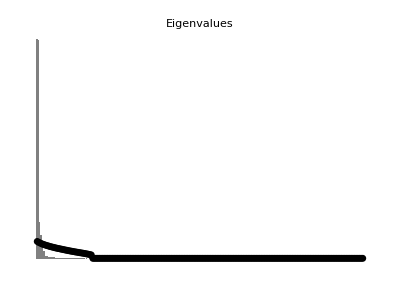
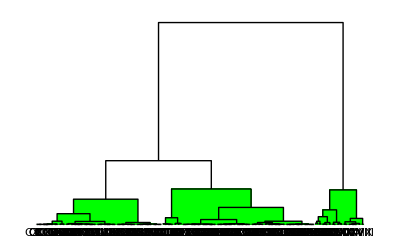
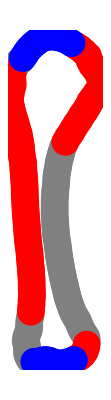
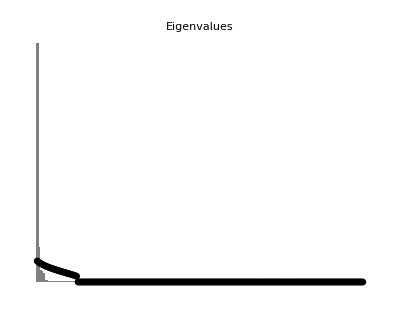
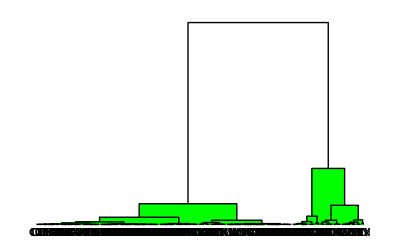
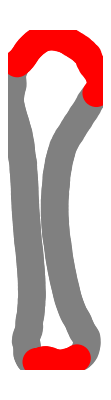
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 25.2079 |  | 
Relative Eigenvalue SD: 4.38814 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.169031 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 31.2715 |  | 
Relative Eigenvalue SD: 6.25431 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.196116 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{HuFMod,HuFLMod}
```

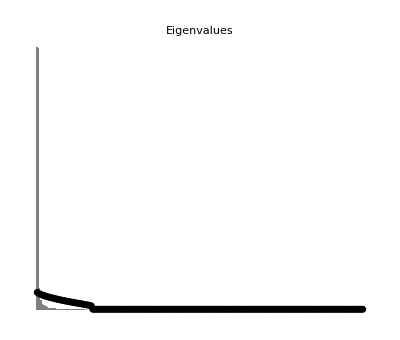
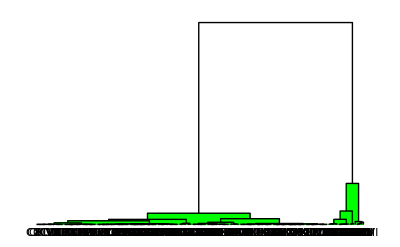
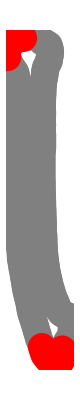
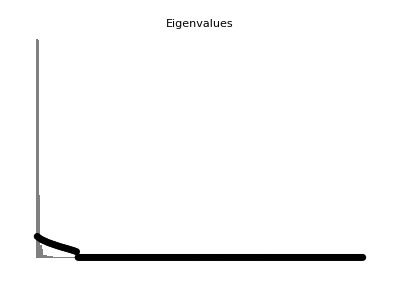
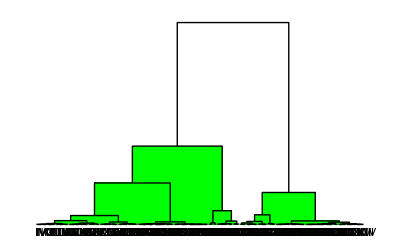
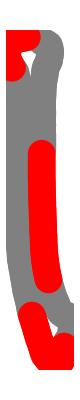
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 29.6729 |  | 
Relative Eigenvalue SD: 5.16539 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.169031 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 29.3316 |  | 
Relative Eigenvalue SD: 5.86632 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.196116 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{UlFMod,UlFLMod}
```

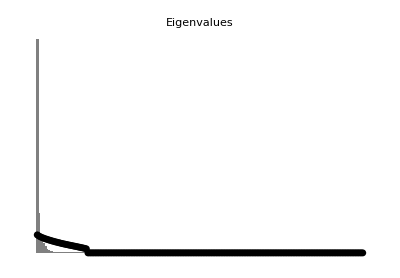
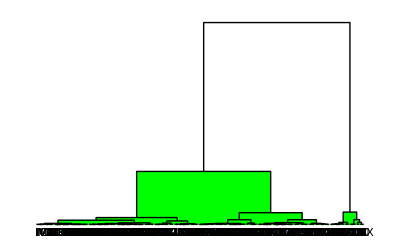
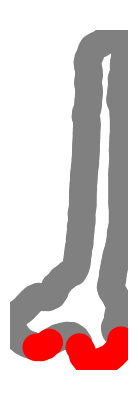
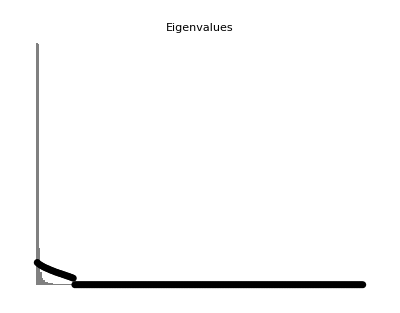
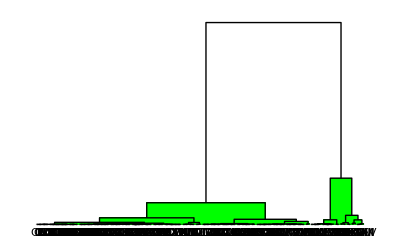
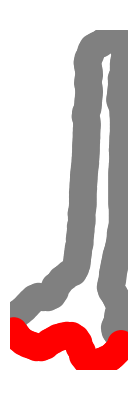
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 25.8245 |  | 
Relative Eigenvalue SD: 4.71488 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.176777 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 32.9852 |  | 
Relative Eigenvalue SD: 6.8779 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.204124 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{MaFMod,MaFLMod}
```

```mathematica
{FeFMod,FeFLMod}
```

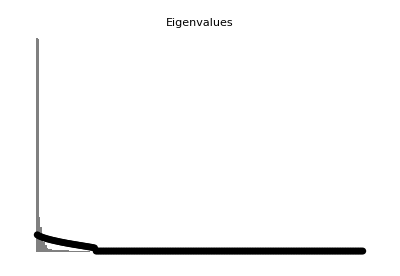
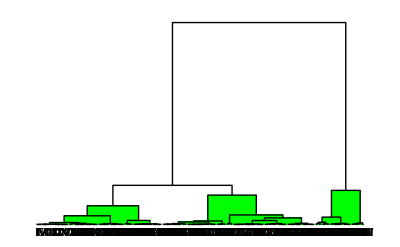
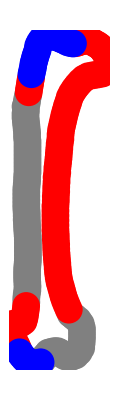
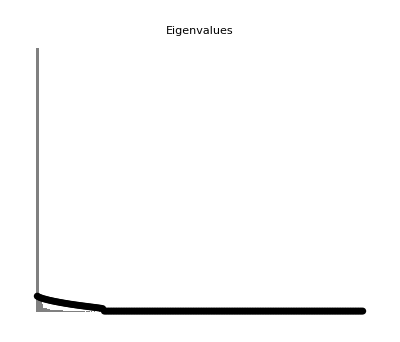
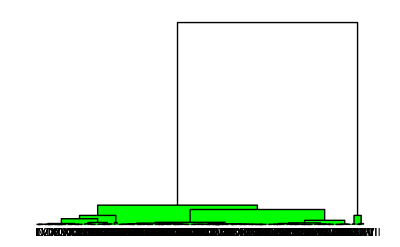
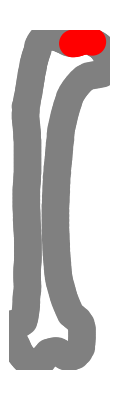
```mathematica
{{{"Modularity Results", "", }, {"Canonical Correlation", "", }, {"Eignvalue SD: 23.7613", , }, {"Relative Eigenvalue SD: 4.01639", , }, {"Expectation of Random Rel. Eigenvalue SD: 0.164399", , }, {"Estimated Number of Modules: 3", , }, {-Graphics-, -Graphics-, -Graphics-}},{{"Modularity Results", "", }, {"Canonical Correlation", "", }, {"Eignvalue SD: 26.693", , }, {"Relative Eigenvalue SD: 4.16874", , }, {"Expectation of Random Rel. Eigenvalue SD: 0.154303", , }, {"Estimated Number of Modules: 2", , }, {-Graphics-, -Graphics-, -Graphics-}}}
```

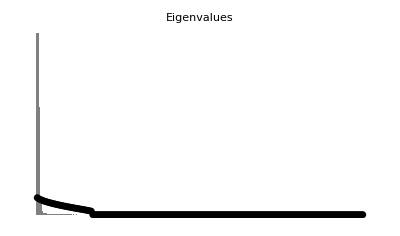
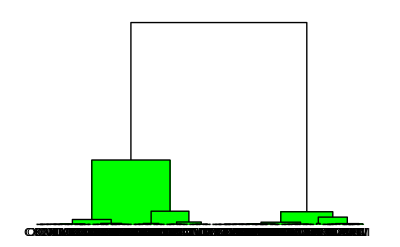
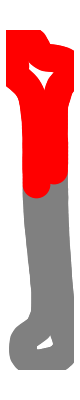
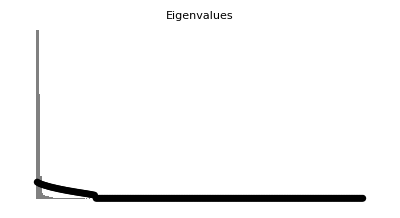
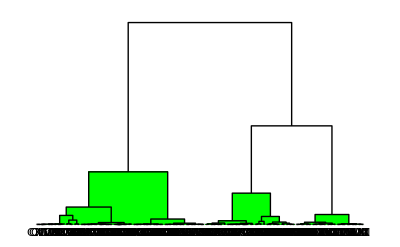
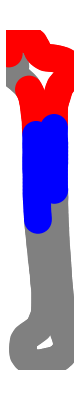
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 23.7411 |  | 
Relative Eigenvalue SD: 4.1328 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.169031 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 21.4126 |  | 
Relative Eigenvalue SD: 3.56876 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.164399 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{TiFMod,TiFLMod}
```

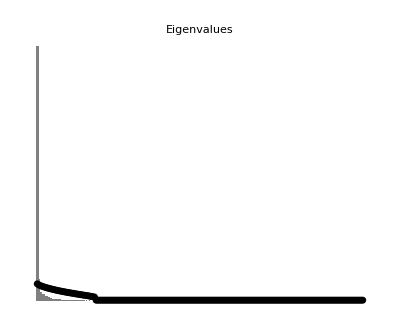
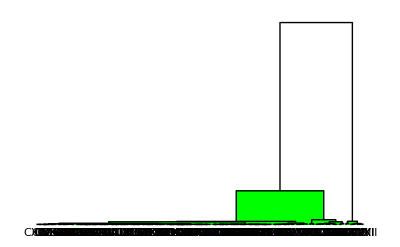
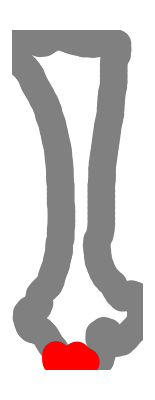
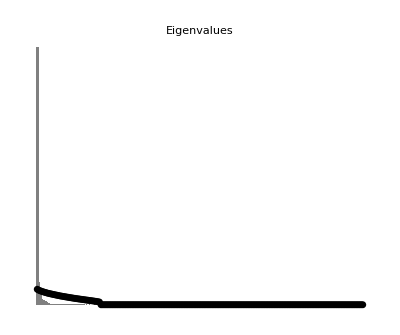
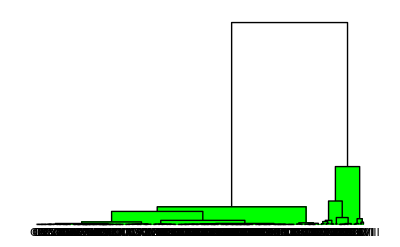
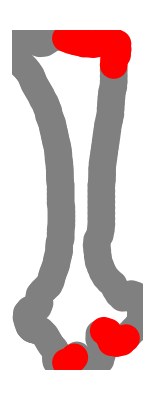
{Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 27.9158 |  | 
Relative Eigenvalue SD: 4.71863 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.164399 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-,Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 26.8556 |  | 
Relative Eigenvalue SD: 4.30034 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.158114 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-}

```mathematica
{TaFMod,TaFLMod}
```

## 2 B PLS

## Intro

```mathematica
(*F={"AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","CassinsAuklet","DblCrstdCormorant","ShrtTldShearwater","CommonMurre"};
FL={"AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GreatAuk","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe"};*)
```

```mathematica
F={"AmericanKestrel","BaldEagle","Budgie","BuffBanRail","Cockatiel","CommonGoldeneye","FlyingSD","GreatTin","Gull","Hoatzin","Ibis","IndianPeafowl","Kea","KingBoP","MagnificentBoP","Nene","RTHumbird","RuffedGrouse","ScopolisShearwater","Sora","YllwCrwndAmazon", "StripedManakin","RockPigeon","RedLggdSeriema","AmericanCoot","MascareneCoot","HornedGrebe","CassinsAuklet","DblCrstdCormorant","ShrtTldShearwater","CommonMurre","AndeanTin","ChileanTin","DarwinsNothura","ElegCrstdTin","LittleTin","SpottedNothura","UndulatedTin","YllwLggdTin"};
FL={"BroadBilledMoa","BushMoa","Cassowary","DarwinsRhea","EasternMoa","Emu","GreaterRhea","GSKiwi","HeavyFootedMoa","LSKiwi","Moa","NBKiwi","NCassowary","NIsGiantMoa","Ostrich","SBKiwi","SCassowary","SIsGiantMoa","GiantMoa","MantellsMoa","AndrosIslandBarnOwl","A.defosson","A.otidiformis","BermudaFLDuck","ChubutSD","DiatrymaGig","Dodo","FalklandSD","FlgtlessCormorant","FuegianSD","GreatAuk","GuamRail","InaccessibleIsRail","Kakapo","LaysanRail","LordHoweRail","NIsTakahe","NZMerganser","P.bachmani","P.lemoinei","RdrgsSolitaire","TasNativehen","TristanMoorhen","Weka", "TiticacaGrebe","NicobarPigeon","GiantCoot","LawsDivingSeaDuck","JuninGrebe"};
```

```mathematica
TwoBlockPLSScoresOnly[Data1_,Data2_,Mode_,PLS_:1]:=Module[{Y1,Y2,N1,N2,R12,F1,Dmat,F2,Z1,Z2,con1,con2,corrs,output,labels1,labels2,ScoresToPlot},

labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];

Which[

Mode=={"Shape","Shape"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2,

Mode=={"Shape","Standardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Standardize[Y2],


Mode=={"Shape","Unstandardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Y2,

Mode=={"Standardized","Standardized"},
Y1=Standardize[Y1];
Y2=Standardize[Y1],

Mode=={"Unstandardized","Standardized"},
Y1=Y1;
Y2=Standardize[Y2],

Mode=={"Unstandardized","Unstandardized"},
Y1=Y1;
Y2=Y2,

Mode==Mode,Return["Mode must be {\"Shape\",\"Shape\"},{\"Shape\",\"Standardized\"}, {\"Shape\",\"Unstandardized\"}, {\"Standardized\",\"Standardized\"}, {\"UnStandardized\",\"Standardized\"}, or  {\"Unstandardized\",\"Unstandardized\"}."];];


N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
R12=Covariance[Y1,Y2];
{F1,Dmat,F2}=SingularValueDecomposition[R12];
Dmat=Tr[Dmat,List];
Z1=Y1.F1;
Z2=Y2.F2;

corrs=Table[Correlation[Z1[[1;;,i]],Z2[[1;;,i]]],{i,Length[Dmat]}];
Which[
Mode=={"Shape","Shape"},output=GraphicsGrid[{{tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],tpSpline[con2,con2+F2[[1;;,PLS]]*Max[Z2[[1;;,PLS]]]]}},ImageSize->500,BaseStyle->{FontFamily->"Arial",FontSize->10},PlotLabel->"Positive End of PLS "<>ToString[PLS]],

Mode=={"Shape","Standardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Shape","Unstandardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Standardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Unstandardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]}];

ScoresToPlot=Transpose[{Z1[[1;;,PLS]],Z2[[1;;,PLS]]}];

Return[{Z1,Z2}]];
```

## Hind limb

### Intro

```mathematica
HLlist=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@FL]];
HindLimbflightless=flightless;
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@F]];
HindLimbflighted=flighted;
```

```mathematica
(*Hindlimb -regular*)
TwoBlockPartialLeastSquares[Data1_,Data2_,Mode_,PLS_:1]:=Module[{Y1,Y2,N1,N2,R12,F1,Dmat,F2,Z1,Z2,con1,con2,corrs,output,labels1,labels2,ScoresToPlot},

labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];

Which[

Mode=={"Shape","Shape"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2,

Mode=={"Shape","Standardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Standardize[Y2],


Mode=={"Shape","Unstandardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Y2,

Mode=={"Standardized","Standardized"},
Y1=Standardize[Y1];
Y2=Standardize[Y1],

Mode=={"Unstandardized","Standardized"},
Y1=Y1;
Y2=Standardize[Y2],

Mode=={"Unstandardized","Unstandardized"},
Y1=Y1;
Y2=Y2,

Mode==Mode,Return["Mode must be {\"Shape\",\"Shape\"},{\"Shape\",\"Standardized\"}, {\"Shape\",\"Unstandardized\"}, {\"Standardized\",\"Standardized\"}, {\"UnStandardized\",\"Standardized\"}, or  {\"Unstandardized\",\"Unstandardized\"}."];];


N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
R12=Covariance[Y1,Y2];
{F1,Dmat,F2}=SingularValueDecomposition[R12];
Dmat=Tr[Dmat,List];
Z1=Y1.F1;
Z2=Y2.F2;

corrs=Table[Correlation[Z1[[1;;,i]],Z2[[1;;,i]]],{i,Length[Dmat]}];
Which[
Mode=={"Shape","Shape"},output=GraphicsGrid[{{tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],tpSpline[con2,con2+F2[[1;;,PLS]]*Max[Z2[[1;;,PLS]]]]}},ImageSize->500,BaseStyle->{FontFamily->"Arial",FontSize->10},PlotLabel->"Positive End of PLS "<>ToString[PLS]],

Mode=={"Shape","Standardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Shape","Unstandardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Standardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Unstandardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]}];

ScoresToPlot=Transpose[{Z1[[1;;,PLS]],Z2[[1;;,PLS]]}];

Return[{

"Proportion of Actual Squared Covariance Explained by PLS "<>ToString[PLS]<>":  "<>ToString[NumberForm[((Dmat^2)/(Plus@@(Dmat^2)))[[PLS]],{3,2}]],

"Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  "<>ToString[NumberForm[(Plus@@(Dmat^2))/(N1*N2),{3,2}]],

flightless=Sort[Flatten[Flatten[Position[Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]],#]]&/@F]];

pts1={PointSize[0.01],Blue,Point[#]}&/@ScoresToPlot[[flightless]];
pts2={PointSize[0.01],Orange,Point[#]}&/@ScoresToPlot[[flighted]];

Graphics[{{pts1,pts2},{Table[Text[labels1[[x]],ScoresToPlot[[x]],{0,1}],{x,Length[labels1]}]}},AspectRatio->1/GoldenRatio,Axes->False,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->10},ImageSize->400,FrameLabel->{"Data 1, PLS "<>ToString[PLS],"Data 2, PLS "<>ToString[PLS]}],

output

}//TableForm];];
```

### Tarso/Tibio

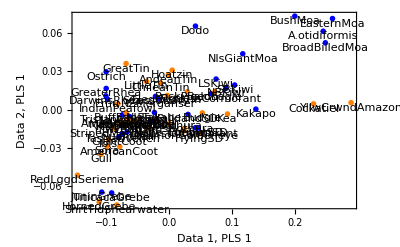
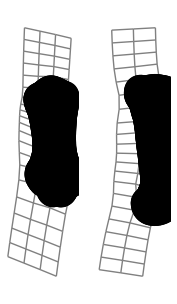
Proportion of Actual Squared Covariance Explained by PLS 1:  0.92
Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  0.10
-Graphics-
-Graphics-

```mathematica
TwoBlockPartialLeastSquares[TarsoProc,TibioProc,{"Shape", "Shape"}]
```

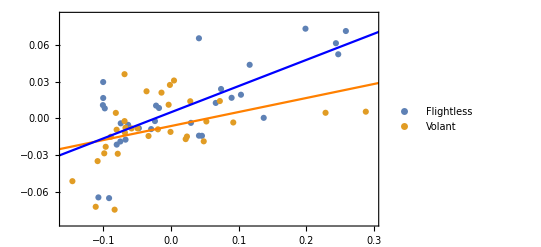

```mathematica
{scoresTarso,scoresTibio}=TwoBlockPLSScoresOnly[TarsoProc,TibioProc,{"Shape", "Shape"}];RegressionData=Transpose[{scoresTarso[[1;;,1]],scoresTibio[[1;;,1]]}];
Clear[x];
lm=LinearModelFit[RegressionData,{1,x},x];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x];
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x];
xrange={((Min[RegressionData[[1;;,1]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,1]]]+0.01};
yrange={((Min[RegressionData[[1;;,2]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,2]]]+0.01};
Show[ListPlot[{RegressionData[[flightless]],RegressionData[[flighted]]}, AspectRatio->1/GoldenRatio,Frame->True, Axes->False,PlotRange->{xrange,yrange},PlotLegends->{"Flightless","Volant"}],Plot[lmflight[T],{T,-0.5,0.5}, PlotStyle->Orange],Plot[lmflightless[T],{T,-0.5,0.5}, PlotStyle->Blue]]
bootdiffs=Table[bootdata=RandomSample[Transpose[{RandomSample[scoresTarso[[1;;,1]]],RandomSample[scoresTibio[[1;;,1]]]}]];
lmflightless=LinearModelFit[bootdata[[flightless]],{1,x},x]["BestFitParameters"][[2]];
lmflight=LinearModelFit[bootdata[[flighted]],{1,x},x]["BestFitParameters"][[2]];lmflightless-lmflight,{5000}];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x]["BestFitParameters"][[2]]
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x]["BestFitParameters"][[2]]
lmflightless-lmflight
Show[Histogram[bootdiffs],Graphics[Line[{{lmflightless-lmflight,0},{lmflightless-lmflight,100}}]]]
N[Length[Select[bootdiffs,#≥lmflight-lmflightless&]]/5000]
```

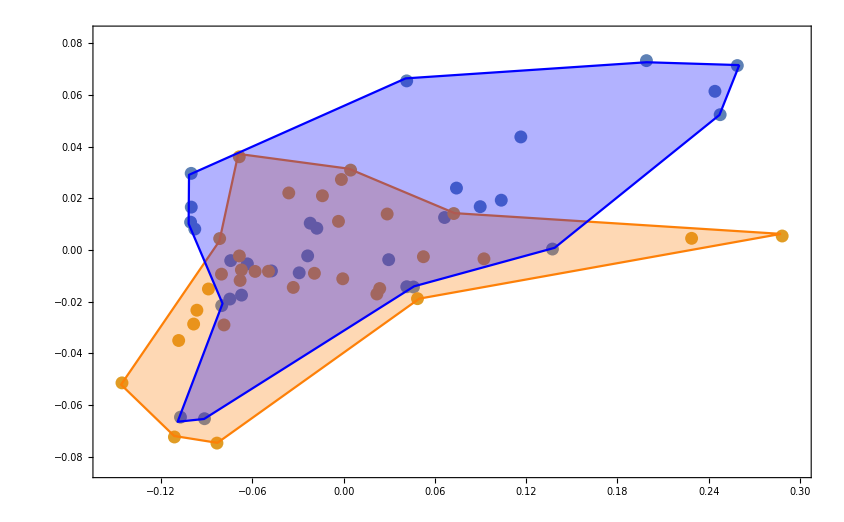

0.213809

0.114495

0.0993138

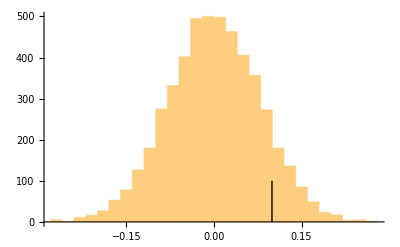

0.8998

### Tarso/Femur

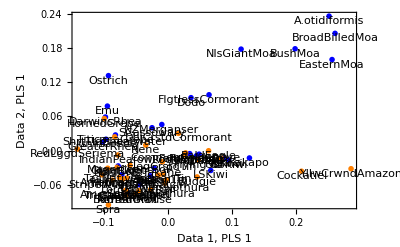
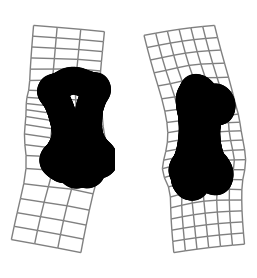
Proportion of Actual Squared Covariance Explained by PLS 1:  0.98
Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  0.13
-Graphics-
-Graphics-

```mathematica
TwoBlockPartialLeastSquares[TarsoProc,FemurProc,{"Shape", "Shape"}]
```

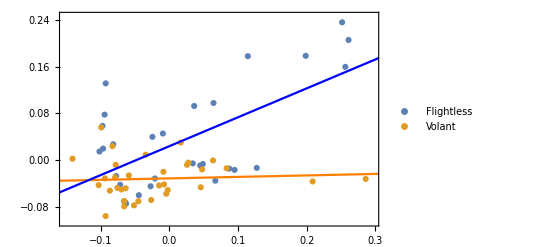

```mathematica
{scoresTarso,scoresFemur}=TwoBlockPLSScoresOnly[TarsoProc,FemurProc,{"Shape", "Shape"}];
RegressionData=Transpose[{scoresTarso[[1;;,1]],scoresFemur[[1;;,1]]}];
Clear[x];
lm=LinearModelFit[RegressionData,{1,x},x];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x];
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x];
xrange={((Min[RegressionData[[1;;,1]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,1]]]+0.01};
yrange={((Min[RegressionData[[1;;,2]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,2]]]+0.01};
Show[ListPlot[{RegressionData[[flightless]],RegressionData[[flighted]]}, AspectRatio->1/GoldenRatio,Frame->True, Axes->False,PlotRange->{xrange,yrange},PlotLegends->{"Flightless","Volant"}],Plot[lmflight[T],{T,-0.5,0.5}, PlotStyle->Orange],Plot[lmflightless[T],{T,-0.5,0.5}, PlotStyle->Blue]]
bootdiffs=Table[bootdata=RandomSample[Transpose[{RandomSample[scoresTarso[[1;;,1]]],RandomSample[scoresFemur[[1;;,1]]]}]];
lmflightless=LinearModelFit[bootdata[[flightless]],{1,x},x]["BestFitParameters"][[2]];
lmflight=LinearModelFit[bootdata[[flighted]],{1,x},x]["BestFitParameters"][[2]];lmflightless-lmflight,{5000}];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x]["BestFitParameters"][[2]]
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x]["BestFitParameters"][[2]]
lmflightless-lmflight
Show[Histogram[bootdiffs],Graphics[Line[{{lmflightless-lmflight,0},{lmflightless-lmflight,100}}]]]
N[Length[Select[bootdiffs,#≥lmflight-lmflightless&]]/5000]
```

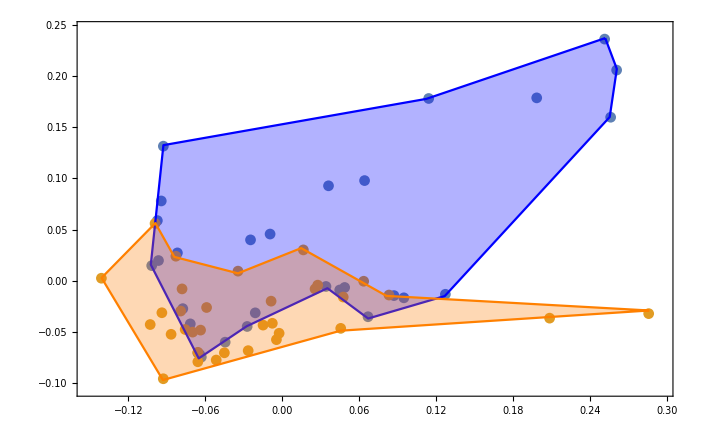

0.494864

0.0253119

0.469552

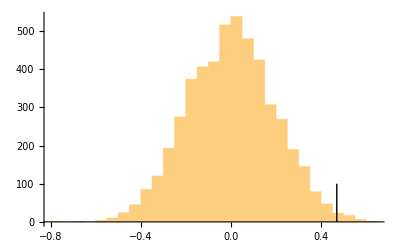

0.9938

### Tibio/Femur

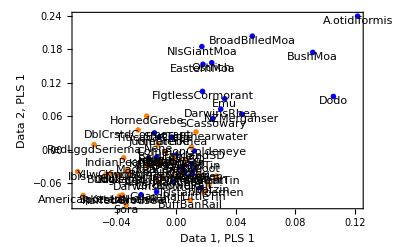
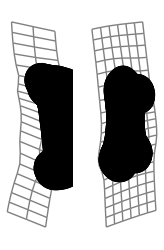
Proportion of Actual Squared Covariance Explained by PLS 1:  0.93
Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  0.12
-Graphics-
-Graphics-

```mathematica
TwoBlockPartialLeastSquares[TibioProc,FemurProc,{"Shape", "Shape"}]
```

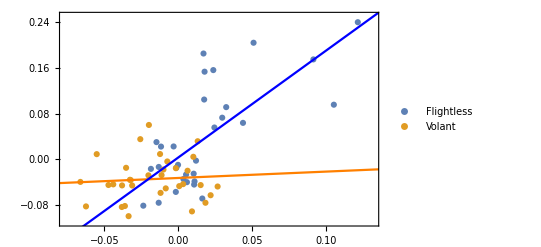

```mathematica
{scoresTibio,scoresFemur}=TwoBlockPLSScoresOnly[TibioProc,FemurProc,{"Shape", "Shape"}];
RegressionData=Transpose[{scoresTibio[[1;;,1]],scoresFemur[[1;;,1]]}];
Clear[x];
lm=LinearModelFit[RegressionData,{1,x},x];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x];
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x];
xrange={((Min[RegressionData[[1;;,1]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,1]]]+0.01};
yrange={((Min[RegressionData[[1;;,2]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,2]]]+0.01};
Show[ListPlot[{RegressionData[[flightless]],RegressionData[[flighted]]}, AspectRatio->1/GoldenRatio,Frame->True, Axes->False,PlotRange->{xrange,yrange},PlotLegends->{"Flightless","Volant"}],Plot[lmflight[T],{T,-0.5,0.5}, PlotStyle->Orange],Plot[lmflightless[T],{T,-0.5,0.5}, PlotStyle->Blue]]
bootdiffs=Table[bootdata=RandomSample[Transpose[{RandomSample[scoresTibio[[1;;,1]]],RandomSample[scoresFemur[[1;;,1]]]}]];
lmflightless=LinearModelFit[bootdata[[flightless]],{1,x},x]["BestFitParameters"][[2]];
lmflight=LinearModelFit[bootdata[[flighted]],{1,x},x]["BestFitParameters"][[2]];lmflightless-lmflight,{5000}];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x]["BestFitParameters"][[2]]
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x]["BestFitParameters"][[2]]
lmflightless-lmflight
Show[Histogram[bootdiffs],Graphics[Line[{{lmflightless-lmflight,0},{lmflightless-lmflight,100}}]]]
N[Length[Select[bootdiffs,#≥lmflight-lmflightless&]]/5000]
```

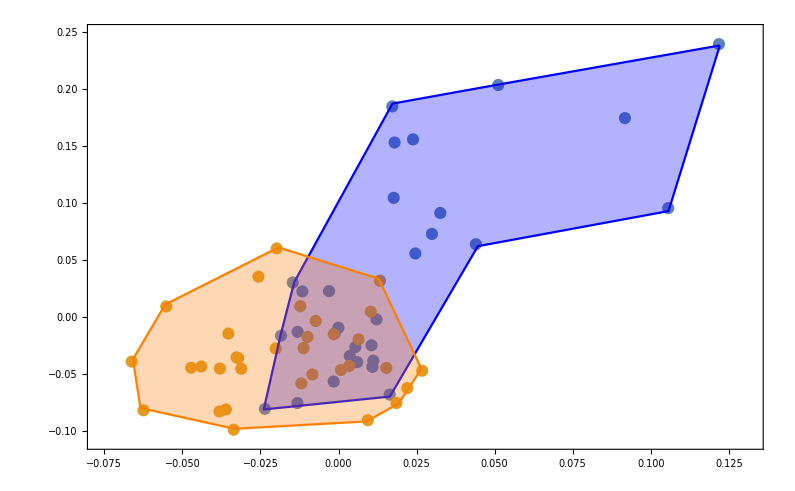

1.86048

0.110887

1.74959

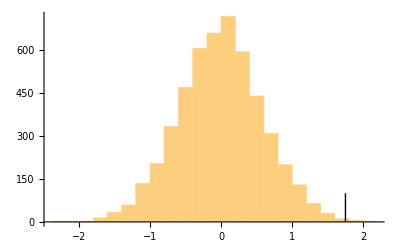

0.9986

## Forelimb

### Intro

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
ForeLimbflightless=flightless;
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
ForeLimbflighted=flighted;
```

```mathematica
(*Forelimb -regular*)
TwoBlockPartialLeastSquares[Data1_,Data2_,Mode_,PLS_:1]:=Module[{Y1,Y2,N1,N2,R12,F1,Dmat,F2,Z1,Z2,con1,con2,corrs,output,labels1,labels2,ScoresToPlot},

labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];

Which[

Mode=={"Shape","Shape"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2,

Mode=={"Shape","Standardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Standardize[Y2],


Mode=={"Shape","Unstandardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Y2,

Mode=={"Standardized","Standardized"},
Y1=Standardize[Y1];
Y2=Standardize[Y1],

Mode=={"Unstandardized","Standardized"},
Y1=Y1;
Y2=Standardize[Y2],

Mode=={"Unstandardized","Unstandardized"},
Y1=Y1;
Y2=Y2,

Mode==Mode,Return["Mode must be {\"Shape\",\"Shape\"},{\"Shape\",\"Standardized\"}, {\"Shape\",\"Unstandardized\"}, {\"Standardized\",\"Standardized\"}, {\"UnStandardized\",\"Standardized\"}, or  {\"Unstandardized\",\"Unstandardized\"}."];];


N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
R12=Covariance[Y1,Y2];
{F1,Dmat,F2}=SingularValueDecomposition[R12];
Dmat=Tr[Dmat,List];
Z1=Y1.F1;
Z2=Y2.F2;

corrs=Table[Correlation[Z1[[1;;,i]],Z2[[1;;,i]]],{i,Length[Dmat]}];
Which[
Mode=={"Shape","Shape"},output=GraphicsGrid[{{tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],tpSpline[con2,con2+F2[[1;;,PLS]]*Max[Z2[[1;;,PLS]]]]}},ImageSize->500,BaseStyle->{FontFamily->"Arial",FontSize->10},PlotLabel->"Positive End of PLS "<>ToString[PLS]],

Mode=={"Shape","Standardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Shape","Unstandardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Standardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Unstandardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]}];

ScoresToPlot=Transpose[{Z1[[1;;,PLS]],Z2[[1;;,PLS]]}];

Return[{

"Proportion of Actual Squared Covariance Explained by PLS "<>ToString[PLS]<>":  "<>ToString[NumberForm[((Dmat^2)/(Plus@@(Dmat^2)))[[PLS]],{3,2}]],

"Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  "<>ToString[NumberForm[(Plus@@(Dmat^2))/(N1*N2),{3,2}]],

flightless=Sort[Flatten[Flatten[Position[Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]],#]]&/@F]];
pts1={PointSize[0.01],Blue,Point[#]}&/@ScoresToPlot[[flightless]];
pts2={PointSize[0.01],Orange,Point[#]}&/@ScoresToPlot[[flighted]];

Graphics[{{pts1,pts2},{Table[Text[labels1[[x]],ScoresToPlot[[x]],{0,1}],{x,Length[labels1]}]}},AspectRatio->1/GoldenRatio,Axes->False,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->10},ImageSize->400,FrameLabel->{"Data 1, PLS "<>ToString[PLS],"Data 2, PLS "<>ToString[PLS]}],

(*Graphics[{{PointSize[0.01],Point[#]}&/@ScoresToPlot,{Table[Text[labels1[[x]],ScoresToPlot[[x]],{0,1}],{x,Length[labels1]}]}},AspectRatio->1/GoldenRatio,Axes->False,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->10},ImageSize->400,FrameLabel->{"Data 1, PLS "<>ToString[PLS],"Data 2, PLS "<>ToString[PLS]}],*)

output

}//TableForm];];
```

### Humerus/Manus

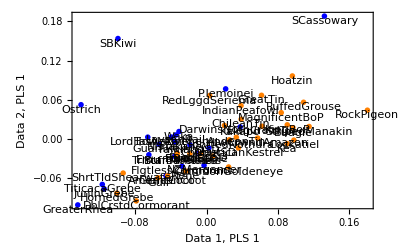
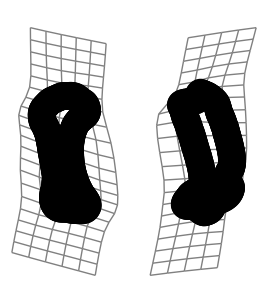
Proportion of Actual Squared Covariance Explained by PLS 1:  0.77
Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  0.06
-Graphics-
-Graphics-

```mathematica
TwoBlockPartialLeastSquares[HumerusProc,ManusProc,{"Shape", "Shape"}]
```

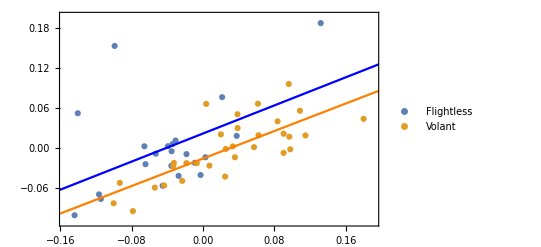

```mathematica
{scoresHumerus,scoresManus}=TwoBlockPLSScoresOnly[HumerusProc,ManusProc,{"Shape", "Shape"}];
RegressionData=Transpose[{scoresHumerus[[1;;,1]],scoresManus[[1;;,1]]}];
Clear[x];
lm=LinearModelFit[RegressionData,{1,x},x];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x];
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x];
xrange={((Min[RegressionData[[1;;,1]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,1]]]+0.01};
yrange={((Min[RegressionData[[1;;,2]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,2]]]+0.01};
Show[ListPlot[{RegressionData[[flightless]],RegressionData[[flighted]]}, AspectRatio->1/GoldenRatio,Frame->True, Axes->False,PlotRange->{xrange,yrange},PlotLegends->{"Flightless","Volant"}],Plot[lmflight[T],{T,-0.5,0.5}, PlotStyle->Orange],Plot[lmflightless[T],{T,-0.5,0.5}, PlotStyle->Blue]]
bootdiffs=Table[bootdata=RandomSample[Transpose[{RandomSample[scoresHumerus[[1;;,1]]],RandomSample[scoresManus[[1;;,1]]]}]];
lmflightless=LinearModelFit[bootdata[[flightless]],{1,x},x]["BestFitParameters"][[2]];
lmflight=LinearModelFit[bootdata[[flighted]],{1,x},x]["BestFitParameters"][[2]];lmflightless-lmflight,{5000}];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x]["BestFitParameters"][[2]]
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x]["BestFitParameters"][[2]]
lmflightless-lmflight
Show[Histogram[bootdiffs],Graphics[Line[{{lmflightless-lmflight,0},{lmflightless-lmflight,100}}]]]
N[Length[Select[bootdiffs,#≥lmflight-lmflightless&]]/5000]
```

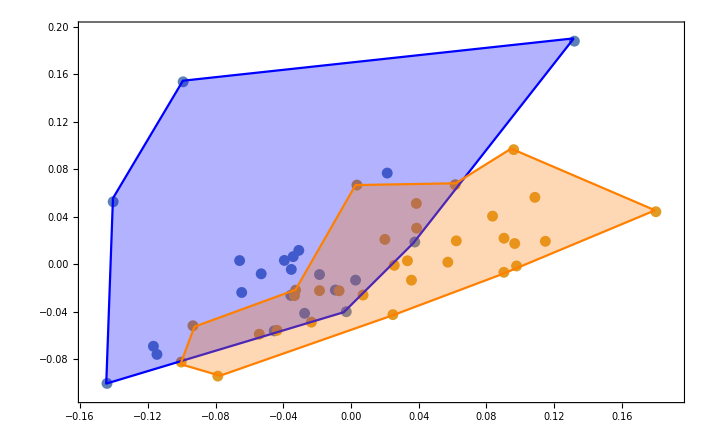

0.527348

0.516177

0.0111713

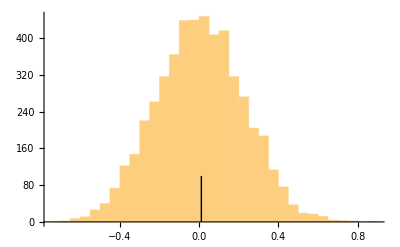

0.5248

### Humerus/Ulna

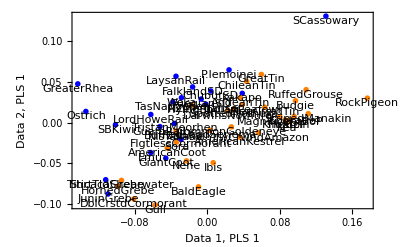
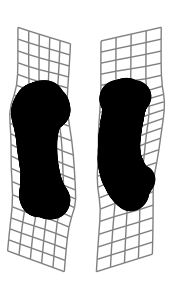
Proportion of Actual Squared Covariance Explained by PLS 1:  0.94
Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  0.10
-Graphics-
-Graphics-

```mathematica
TwoBlockPartialLeastSquares[HumerusProc,UlnaProc,{"Shape", "Shape"}]
```

```mathematica
Dimensions[RegressionData]
```

{53,2}

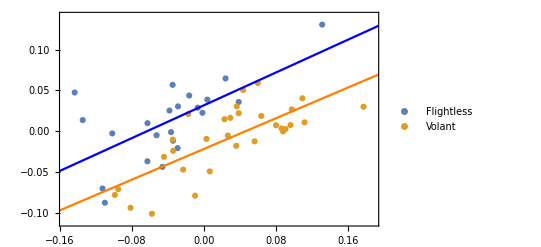

```mathematica
{scoresHumerus,scoresUlna}=TwoBlockPLSScoresOnly[HumerusProc,UlnaProc,{"Shape", "Shape"}];
RegressionData=Transpose[{scoresHumerus[[1;;,1]],scoresUlna[[1;;,1]]}];
Clear[x];
lm=LinearModelFit[RegressionData,{1,x},x];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x];
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x];
xrange={((Min[RegressionData[[1;;,1]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,1]]]+0.01};
yrange={((Min[RegressionData[[1;;,2]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,2]]]+0.01};
Show[ListPlot[{RegressionData[[flightless]],RegressionData[[flighted]]}, AspectRatio->1/GoldenRatio,Frame->True, Axes->False,PlotRange->{xrange,yrange},PlotLegends->{"Flightless","Volant"}],Plot[lmflight[T],{T,-0.5,0.5}, PlotStyle->Orange],Plot[lmflightless[T],{T,-0.5,0.5}, PlotStyle->Blue]]
bootdiffs=Table[bootdata=RandomSample[Transpose[{RandomSample[scoresHumerus[[1;;,1]]],RandomSample[scoresUlna[[1;;,1]]]}]];
lmflightless=LinearModelFit[bootdata[[flightless]],{1,x},x]["BestFitParameters"][[2]];
lmflight=LinearModelFit[bootdata[[flighted]],{1,x},x]["BestFitParameters"][[2]];lmflightless-lmflight,{5000}];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x]["BestFitParameters"][[2]]
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x]["BestFitParameters"][[2]]
lmflightless-lmflight
Show[Histogram[bootdiffs],Graphics[Line[{{lmflightless-lmflight,0},{lmflightless-lmflight,100}}]]]
N[Length[Select[bootdiffs,#≥lmflight-lmflightless&]]/5000]
```

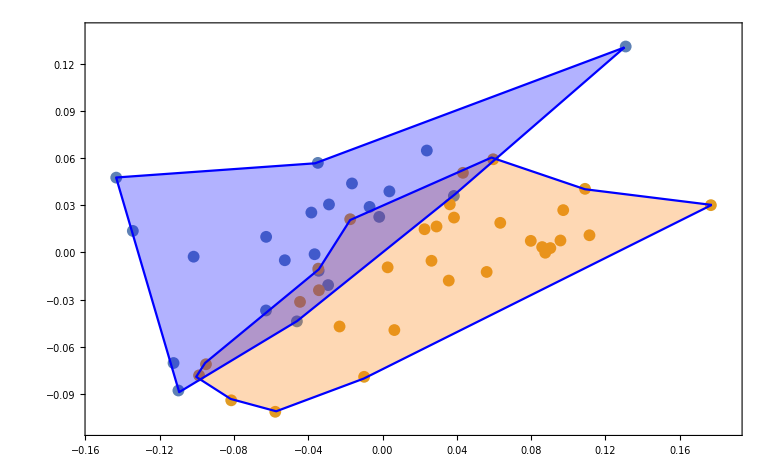

0.504237

0.471978

0.0322596

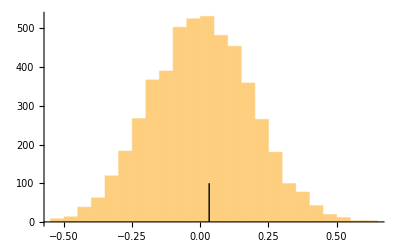

0.57

### Ulna/Manus

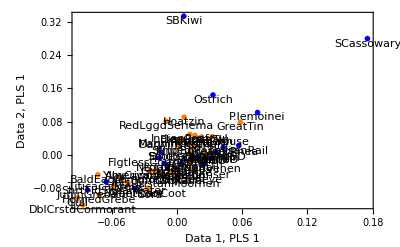
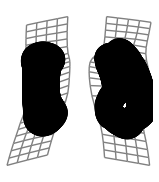
Proportion of Actual Squared Covariance Explained by PLS 1:  0.97
Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  0.18
-Graphics-
-Graphics-

```mathematica
TwoBlockPartialLeastSquares[UlnaProc,ManusProc,{"Shape", "Shape"}]
```

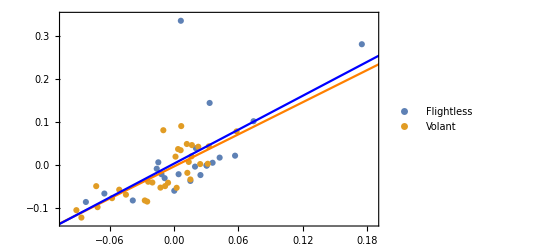

```mathematica
{scoresUlna,scoresManus}=TwoBlockPLSScoresOnly[UlnaProc,ManusProc,{"Shape", "Shape"}];
RegressionData=Transpose[{scoresUlna[[1;;,1]],scoresManus[[1;;,1]]}];
Clear[x];
lm=LinearModelFit[RegressionData,{1,x},x];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x];
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x];
xrange={((Min[RegressionData[[1;;,1]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,1]]]+0.01};
yrange={((Min[RegressionData[[1;;,2]]]*-1)+0.01)*-1,Max[RegressionData[[1;;,2]]]+0.01};
Show[ListPlot[{RegressionData[[flightless]],RegressionData[[flighted]]}, AspectRatio->1/GoldenRatio,Frame->True, Axes->False,PlotRange->{xrange,yrange},PlotLegends->{"Flightless","Volant"}],Plot[lmflight[T],{T,-0.5,0.5}, PlotStyle->Orange],Plot[lmflightless[T],{T,-0.5,0.5}, PlotStyle->Blue]]
bootdiffs=Table[bootdata=RandomSample[Transpose[{RandomSample[scoresUlna[[1;;,1]]],RandomSample[scoresManus[[1;;,1]]]}]];
lmflightless=LinearModelFit[bootdata[[flightless]],{1,x},x]["BestFitParameters"][[2]];
lmflight=LinearModelFit[bootdata[[flighted]],{1,x},x]["BestFitParameters"][[2]];lmflightless-lmflight,{5000}];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x]["BestFitParameters"][[2]]
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x]["BestFitParameters"][[2]]
lmflightless-lmflight
Show[Histogram[bootdiffs],Graphics[Line[{{lmflightless-lmflight,0},{lmflightless-lmflight,100}}]]]
N[Length[Select[bootdiffs,#≥lmflight-lmflightless&]]/5000]
```

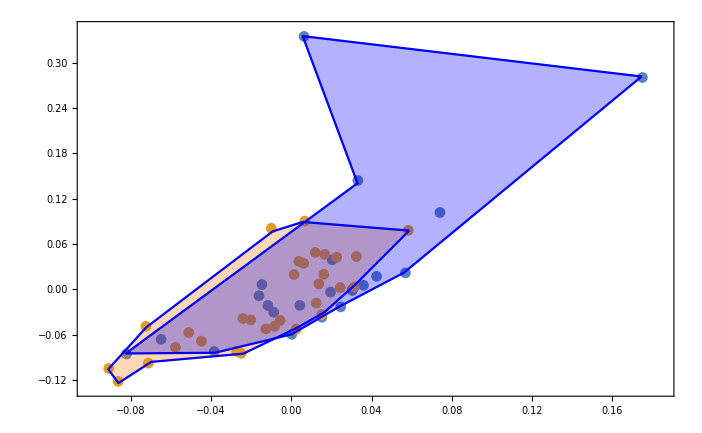

1.31254

1.24284

0.0696988

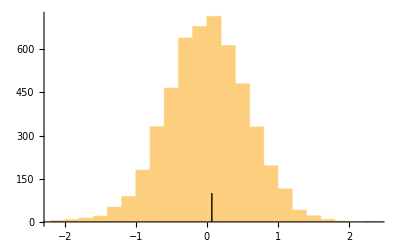

0.5488

## Mantel for 2 B - PLS

```mathematica
MantelForMorphometrics[matrix1_,matrix2_,n_]:=Module[{M1,M2,i,j,z,znull,R1,R2,rz,p},M1=Flatten[Table[Table[matrix1[[i,j]],{j,i,Length[matrix1]}],{i,Length[matrix1]}]];
M1=(#-Mean[M1])/StandardDeviation[M1]&/@M1;
M2=Flatten[Table[Table[matrix2[[i,j]],{j,i,Length[matrix2]}],{i,Length[matrix2]}]];
M2=(#-Mean[M2])/StandardDeviation[M2]&/@M2;
z=Plus@@(M1*M2)/(Length[M1]-1);
znull=Table[R1=RandomSample[M1];R2=RandomSample[M2];
rz=(Plus@@(R1*R2))/(Length[R1]-1),{n}];
p=Length[Select[znull,#>z&]]/n//N;
Return[{z,p}]]
```

## HindLimb

```mathematica
HLlist=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]];
flProc=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@FL]];
fProc=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@F]];
```

### Tarso/Tibia

```mathematica
Data1=TarsoProc[[fProc]];
Data2=TibioProc[[fProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
fR12=Covariance[Y1,Y2];
fR12=fR12[[1;;200,201;;]];
```

```mathematica
Data1=TarsoProc[[flProc]];
Data2=TibioProc[[flProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
flR12=Covariance[Y1,Y2];
flR12=flR12[[1;;200,201;;]];
```

```mathematica
MantelForMorphometrics[fR12,flR12,10000]
```

{0.616918,0.}

### Tibia/Femur

```mathematica
Data1=FemurProc[[fProc]];
Data2=TibioProc[[fProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
fR12=Covariance[Y1,Y2];
fR12=fR12[[1;;200,201;;]];
```

```mathematica
Data1=FemurProc[[flProc]];
Data2=TibioProc[[flProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
flR12=Covariance[Y1,Y2];
flR12=flR12[[1;;200,201;;]];
```

```mathematica
MantelForMorphometrics[fR12,flR12,10000]
```

{-0.174646,1.}

### Tarso/Femur

```mathematica
Data1=TarsoProc[[fProc]];
Data2=FemurProc[[fProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
fR12=Covariance[Y1,Y2];
fR12=fR12[[1;;200,201;;]];
```

```mathematica
Data1=TarsoProc[[flProc]];
Data2=FemurProc[[flProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
flR12=Covariance[Y1,Y2];
flR12=flR12[[1;;200,201;;]];
```

```mathematica
MantelForMorphometrics[fR12,flR12,10000]
```

{0.116064,0.}

## ForeLimb

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
flProc=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
fProc=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
```

### Humerus/Ulna

```mathematica
Data1=HumerusProc[[fProc]];
Data2=UlnaProc[[fProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
fR12=Covariance[Y1,Y2];
fR12=fR12[[1;;200,201;;]];
```

```mathematica
Data1=HumerusProc[[flProc]];
Data2=UlnaProc[[flProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
flR12=Covariance[Y1,Y2];
flR12=flR12[[1;;200,201;;]];
```

```mathematica
MantelForMorphometrics[fR12,flR12,10000]
```

{0.78252,0.}

### Ulna/Manus

```mathematica
Data1=ManusProc[[fProc]];
Data2=UlnaProc[[fProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
fR12=Covariance[Y1,Y2];
fR12=fR12[[1;;200,201;;]];
```

```mathematica
Data1=ManusProc[[flProc]];
Data2=UlnaProc[[flProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
flR12=Covariance[Y1,Y2];
flR12=flR12[[1;;200,201;;]];
```

```mathematica
MantelForMorphometrics[fR12,flR12,10000]
```

{0.655677,0.}

### Humerus/Manus

```mathematica
Data1=ManusProc[[fProc]];
Data2=HumerusProc[[fProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
fR12=Covariance[Y1,Y2];
fR12=fR12[[1;;200,201;;]];
```

```mathematica
Data1=ManusProc[[flProc]];
Data2=HumerusProc[[flProc]];
labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2;
N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
flR12=Covariance[Y1,Y2];
flR12=flR12[[1;;200,201;;]];
```

```mathematica
MantelForMorphometrics[fR12,flR12,10000]
```

{0.571158,0.}

## CPCA 2 BPLS

Run PCA and 2 BPLS and regression AllTaxa code

## HindLimb

```mathematica
HLlist=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@FL]];
HindLimbflightless=flightless;
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@F]];
HindLimbflighted=flighted;
```

```mathematica
AllLabels=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]];
X=1;
Table[
Table[
If[
AllLabels[[i]]==F[[j]],AllLabels[[i]]="flight"]
,{j,Length[F]}];

Table[
If[
AllLabels[[i]]==FL[[k]],AllLabels[[i]]="flightless"]
,{k,Length[FL]}];

,{i,Length[AllLabels]}];

FlyList=AllLabels;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/HindLimbAllTaxa_2BPLS_labels.csv",FlyList,"CSV"];
```

### Tarso Tibio

#### Intro

```mathematica
{scoresTarso,scoresTibio}=TwoBlockPLSScoresOnly[TarsoProc,TibioProc,{"Shape", "Shape"}];
tesst=Riffle[Transpose[scoresTarso],
Transpose[scoresTibio]];
AllPCs=Transpose[tesst];
scores=AllPCs[[1;;,1;;46]];
scores=scores*1000;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/TarsoTibioAllTaxa_2BPLS_Scores.csv",scores,"CSV"];
```

#### After R

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarsoTibio_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarsoTibio_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarsoTibio_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 68.017 | 8.62003 | 6.84716 | 2.90346 | 0.509046 | 1.68044 | 3.6906 | 0.299722 | 0.995129 | 1.41849
flightless | 69.8538 | 9.31045 | 3.66237 | 2.8968 | 4.4819 | 1.41343 | 0.628849 | 2.67871 | 0.767344 | 0.244483)

```mathematica
CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
{FscoresTarso,FscoresTibio}=TwoBlockPLSScoresOnly[TarsoProc[[HindLimbflighted]],TibioProc[[HindLimbflighted]],{"Shape", "Shape"}];
Ftesst=Riffle[Transpose[FscoresTarso],
Transpose[FscoresTibio]];
X=1;
VarF=Table[Variance[Ftesst[[X]]],{X,Length[Ftesst]}];
{FLscoresTarso,FLscoresTibio}=TwoBlockPLSScoresOnly[TarsoProc[[HindLimbflightless]],TibioProc[[HindLimbflightless]],{"Shape", "Shape"}];
FLtesst=Riffle[Transpose[FLscoresTarso],
Transpose[FLscoresTibio]];
X=1;
VarFL=Table[Variance[FLtesst[[X]]],{X,Length[FLtesst]}];
TarsoTibiacpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],VarF[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],VarFL[[1;;10]]};
TarsoTibiacpcaEV
```

{{0.008714486,0.001104416,0.000877273,0.000371997,0.00006522,0.000215301,0.000472847,0.000038401,0.000127498,0.00018174},{0.00860578,0.0009829,0.000244473,0.000960971,0.000446486,0.000132565,0.000585057,0.0000943063,0.00011308,0.000144556},{0.012633688,0.001683878,0.000662373,0.000523913,0.000810591,0.000255632,0.000113733,0.000484468,0.000138781,0.000044217},{0.0128708,0.00113254,0.000873376,0.00130069,0.000276895,0.000437297,0.000334019,0.000152793,0.000225477,0.000075639}}

### Tarso Femur

#### Intro

```mathematica
{scoresTarso,scoresFemur}=TwoBlockPLSScoresOnly[TarsoProc,FemurProc,{"Shape", "Shape"}];
tesst=Riffle[Transpose[scoresTarso],
Transpose[scoresFemur]];
AllPCs=Transpose[tesst];
scores=AllPCs[[1;;,1;;46]];
scores=scores*1000;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/TarsoFemurAllTaxa_2BPLS_Scores.csv",scores,"CSV"];
```

#### After R

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarsoFemur_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarsoFemur_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTarsoFemur_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 61.8293 | 10.923 | 2.75378 | 5.53 | 1.75027 | 1.19828 | 4.00147 | 1.62134 | 2.01068 | 0.327158
flightless | 54.6074 | 29.9227 | 4.1169 | 2.68016 | 1.85086 | 1.11434 | 0.396595 | 0.362033 | 1.0655 | 1.01334)

```mathematica
CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
{FscoresTarso,FscoresFemur}=TwoBlockPLSScoresOnly[TarsoProc[[HindLimbflighted]],FemurProc[[HindLimbflighted]],{"Shape", "Shape"}];
Ftesst=Riffle[Transpose[FscoresTarso],
Transpose[FscoresFemur]];
X=1;
VarF=Table[Variance[Ftesst[[X]]],{X,Length[Ftesst]}];
{FLscoresTarso,FLscoresFemur}=TwoBlockPLSScoresOnly[TarsoProc[[HindLimbflightless]],FemurProc[[HindLimbflightless]],{"Shape", "Shape"}];
FLtesst=Riffle[Transpose[FLscoresTarso],
Transpose[FLscoresFemur]];
X=1;
VarFL=Table[Variance[FLtesst[[X]]],{X,Length[FLtesst]}];
TarsoFemurcpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],VarF[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],VarFL[[1;;10]]};
TarsoFemurcpcaEV//MatrixForm
```

({0.008332537,0.001472054,0.000371118,0.00074526,0.000235878,0.000161488,0.000539265,0.000218503,0.000270973,0.00004409}
{0.00869556,0.000440643,0.000519428,0.00154775,0.000202776,0.000398766,0.000377818,0.000294772,0.00015904,0.000183205}
{0.013685739,0.007499248,0.001031781,0.000671703,0.000463864,0.000279277,0.000099395,0.000090733,0.000267036,0.000253964}
{0.0126948,0.00760686,0.000683082,0.00136619,0.000497937,0.000664036,0.000413605,0.000189975,0.000234587,0.00023436})

### Tibio Femur

#### Intro

```mathematica
{scoresFemur,scoresTibio}=TwoBlockPLSScoresOnly[FemurProc,TibioProc,{"Shape", "Shape"}];
tesst=Riffle[Transpose[scoresFemur],
Transpose[scoresTibio]];
AllPCs=Transpose[tesst];
scores=AllPCs[[1;;,1;;46]];
scores=scores*1000;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/TibioFemurAllTaxa_2BPLS_Scores.csv",scores,"CSV"];
```

#### After R

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTibioFemur_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTibioFemur_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaTibioFemur_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 19.6432 | 22.4918 | 24.4698 | 5.61476 | 4.36115 | 3.56392 | 7.66835 | 1.23663 | 1.26351 | 2.43629
flightless | 66.0366 | 5.99992 | 9.55386 | 5.28939 | 2.28125 | 3.43143 | 0.66135 | 2.12744 | 0.524619 | 0.292897)

```mathematica
CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
{FscoresTibio,FscoresFemur}=TwoBlockPLSScoresOnly[TibioProc[[HindLimbflighted]],FemurProc[[HindLimbflighted]],{"Shape", "Shape"}];
Ftesst=Riffle[Transpose[FscoresTibio],
Transpose[FscoresFemur]];
X=1;
VarF=Table[Variance[Ftesst[[X]]],{X,Length[Ftesst]}];

{FLscoresTibio,FLscoresFemur}=TwoBlockPLSScoresOnly[TibioProc[[HindLimbflightless]],FemurProc[[HindLimbflightless]],{"Shape", "Shape"}];
FLtesst=Riffle[Transpose[FLscoresTibio],
Transpose[FLscoresFemur]];
X=1;
VarFL=Table[Variance[FLtesst[[X]]],{X,Length[FLtesst]}];
TibiaFemurcpcaEV={AccountingForm[CPCAlambda[[2,2;;11]],11],VarF[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]],11],VarFL[[1;;10]]};
TibiaFemurcpcaEV
```

{{0.001092719,0.001251182,0.001361216,0.00031234,0.000242604,0.000198255,0.000426578,0.000068792,0.000070287,0.000135527},{0.00102883,0.0017494,0.000943172,0.000357906,0.000176375,0.000283906,0.0000861149,0.000163839,0.0000434939,0.000199633},{0.008902533,0.000808862,0.001287976,0.000713074,0.00030754,0.000462598,0.000089158,0.000286805,0.000070725,0.000039486},{0.00129504,0.00836977,0.000935553,0.000786931,0.000391814,0.000242329,0.000373087,0.000325953,0.00014802,0.000191575}}

## ForeLimbs

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
ForeLimbflightless=flightless;
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
ForeLimbflighted=flighted;
```

```mathematica
AllLabels=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
X=1;
Table[
Table[
If[
AllLabels[[i]]==F[[j]],AllLabels[[i]]="flight"]
,{j,Length[F]}];

Table[
If[
AllLabels[[i]]==FL[[k]],AllLabels[[i]]="flightless"]
,{k,Length[FL]}];

,{i,Length[AllLabels]}];

FlyList=AllLabels;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/ForeLimbAllTaxa_2BPLS_labels.csv",FlyList,"CSV"];
```

### Humerus Ulna

#### Intro

```mathematica
{scoresHumerus,scoresUlna}=TwoBlockPLSScoresOnly[HumerusProc,UlnaProc,{"Shape", "Shape"}];
tesst=Riffle[Transpose[scoresHumerus],
Transpose[scoresUlna]];
AllPCs=Transpose[tesst];
scores=AllPCs[[1;;,1;;45]];
scores=scores*1000;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/HumerusUlnaAllTaxa_2BPLS_Scores.csv",scores,"CSV"];
```

#### After R

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerusUlna_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerusUlna_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerusUlna_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 60.782 | 14.5119 | 1.0619 | 2.1533 | 2.31095 | 2.26962 | 1.01128 | 2.00795 | 5.10197 | 0.293299
flightless | 51.1805 | 12.9 | 16.6797 | 3.99172 | 5.85369 | 2.4971 | 2.64735 | 0.713574 | 0.317602 | 1.13437)

```mathematica
CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
{FscoresHumerus,FscoresUlna}=TwoBlockPLSScoresOnly[HumerusProc[[ForeLimbflighted]],UlnaProc[[ForeLimbflighted]],{"Shape", "Shape"}];
Ftesst=Riffle[Transpose[FscoresHumerus],
Transpose[FscoresUlna]];
X=1;
VarF=Table[Variance[Ftesst[[X]]],{X,Length[Ftesst]}];

{FLscoresHumerus,FLscoresUlna}=TwoBlockPLSScoresOnly[HumerusProc[[ForeLimbflightless]],UlnaProc[[ForeLimbflightless]],{"Shape", "Shape"}];
FLtesst=Riffle[Transpose[FLscoresHumerus],
Transpose[FLscoresUlna]];
X=1;
VarFL=Table[Variance[FLtesst[[X]]],{X,Length[FLtesst]}];
HumerusUlnacpcaEV={AccountingForm[CPCAlambda[[2,2;;11]]],VarF[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]]],VarFL[[1;;10]]};
HumerusUlnacpcaEV
```

{{0.00565235,0.00134951,0.00009875,0.000200243,0.000214904,0.00021106,0.000094043,0.000186727,0.000474451,0.000027275},{0.00453003,0.00185107,0.000865333,0.000179924,0.000917529,0.0000721249,0.000287483,0.00009682,0.000139742,0.0000630417},{0.00530608,0.00133739,0.00172925,0.000413837,0.000606875,0.000258884,0.000274461,0.000073979,0.000032927,0.000117605},{0.00397038,0.00260805,0.00103808,0.000897811,0.00055828,0.000360351,0.000237897,0.000150398,0.000405425,0.000154842}}

### Humerus Manus

#### Intro

```mathematica
{scoresHumerus,scoresManus}=TwoBlockPLSScoresOnly[HumerusProc,ManusProc,{"Shape", "Shape"}];
tesst=Riffle[Transpose[scoresHumerus],
Transpose[scoresManus]];
AllPCs=Transpose[tesst];
scores=AllPCs[[1;;,1;;45]];
scores=scores*1000;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/HumerusManusAllTaxa_2BPLS_Scores.csv",scores,"CSV"];
```

#### After R

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerusManus_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerusManus_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaHumerusManus_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 53.4832 | 15.3547 | 6.62996 | 0.833999 | 3.56416 | 0.879344 | 2.61722 | 0.787098 | 0.43516 | 6.19288
flightless | 30.9346 | 25.6866 | 5.73034 | 25.7831 | 1.72956 | 1.20554 | 1.09347 | 1.21571 | 3.18226 | 0.0944336)

```mathematica
CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
{FscoresHumerus,FscoresManus}=TwoBlockPLSScoresOnly[HumerusProc[[ForeLimbflighted]],ManusProc[[ForeLimbflighted]],{"Shape", "Shape"}];
Ftesst=Riffle[Transpose[FscoresHumerus],
Transpose[FscoresManus]];
X=1;
VarF=Table[Variance[Ftesst[[X]]],{X,Length[Ftesst]}];

{FLscoresHumerus,FLscoresManus}=TwoBlockPLSScoresOnly[HumerusProc[[ForeLimbflightless]],ManusProc[[ForeLimbflightless]],{"Shape", "Shape"}];
FLtesst=Riffle[Transpose[FLscoresHumerus],
Transpose[FLscoresManus]];
X=1;
VarFL=Table[Variance[FLtesst[[X]]],{X,Length[FLtesst]}];
HumerusManuscpcaEV={AccountingForm[CPCAlambda[[2,2;;11]]],VarF[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]]],VarFL[[1;;10]]};
HumerusManuscpcaEV//MatrixForm
```

({0.00673369,0.0019332,0.000834732,0.000105003,0.000448738,0.000110712,0.000329516,0.000099098,0.000054788,0.000779702}
{0.00451046,0.00355853,0.0012225,0.000787834,0.000509195,0.000354996,0.000315547,0.000147102,0.000181688,0.000165107}
{0.00737383,0.00612288,0.00136593,0.00614589,0.000412273,0.000287362,0.000260648,0.000289786,0.00075855,0.00002251}
{0.00312921,0.00726088,0.00219815,0.00680464,0.000377368,0.0019623,0.000309688,0.00113304,0.000141239,0.000489553})

### Ulna Manus

#### Intro

```mathematica
{scoresUlna,scoresManus}=TwoBlockPLSScoresOnly[UlnaProc,ManusProc,{"Shape", "Shape"}];
tesst=Riffle[Transpose[scoresUlna],
Transpose[scoresManus]];
AllPCs=Transpose[tesst];
scores=AllPCs[[1;;,1;;45]];
scores=scores*1000;
```

```mathematica
Export["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/UlnaManusAllTaxa_2BPLS_Scores.csv",scores,"CSV"];
```

#### After R

```mathematica
CPCAloadings=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaUlnaManus_results.csv"];
CPCAexpvar=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaUlnaManus_exp-var.csv"];
CPCAlambda1=Import["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/CPCA/New CPCA files/cpcaUlnaManus_lambda.csv"];
CPCAlambda=(Sqrt[CPCAlambda1[[2;;,2;;]]]/1000)^2;
CPCAlambda=Prepend[{Prepend[CPCAlambda[[1]],"flighted"],Prepend[CPCAlambda[[2]],"flightless"]},CPCAlambda1[[1]]];
```

```mathematica
CPCAexpvar[[1;;,1;;11]]//MatrixForm
```

( | Dim1 | Dim2 | Dim3 | Dim4 | Dim5 | Dim6 | Dim7 | Dim8 | Dim9 | Dim10
flight | 60.0888 | 13.6506 | 6.64083 | 0.973929 | 1.37609 | 0.942989 | 2.15084 | 1.96369 | 1.15458 | 0.493109
flightless | 42.5651 | 9.19735 | 5.43548 | 28.3721 | 6.43402 | 2.46978 | 0.969012 | 1.63013 | 0.653246 | 1.3358)

```mathematica
CPCAlambda[[1;;,1;;11]]//MatrixForm;
```

```mathematica
{FscoresUlna,FscoresManus}=TwoBlockPLSScoresOnly[UlnaProc[[ForeLimbflighted]],ManusProc[[ForeLimbflighted]],{"Shape", "Shape"}];
Ftesst=Riffle[Transpose[FscoresUlna],
Transpose[FscoresManus]];
X=1;
VarF=Table[Variance[Ftesst[[X]]],{X,Length[Ftesst]}];

{FLscoresUlna,FLscoresManus}=TwoBlockPLSScoresOnly[UlnaProc[[ForeLimbflightless]],ManusProc[[ForeLimbflightless]],{"Shape", "Shape"}];
FLtesst=Riffle[Transpose[FLscoresUlna],
Transpose[FLscoresManus]];
X=1;
VarFL=Table[Variance[FLtesst[[X]]],{X,Length[FLtesst]}];
UlnaManuscpcaEV={AccountingForm[CPCAlambda[[2,2;;11]]],VarF[[1;;10]],AccountingForm[CPCAlambda[[3,2;;11]]],VarFL[[1;;10]]};
UlnaManuscpcaEV
```

{{0.00476204,0.00108181,0.000526287,0.000077184,0.000109055,0.000074732,0.000170454,0.000155623,0.000091501,0.000039079},{0.00183315,0.00366288,0.000169456,0.000897383,0.000107721,0.000344724,0.000118851,0.000251545,0.0000536253,0.000115181},{0.00925615,0.00200004,0.00118199,0.00616976,0.00139913,0.000537074,0.00021072,0.000354486,0.000142054,0.000290481},{0.00246475,0.0117956,0.00100888,0.000940427,0.000359096,0.00182888,0.000112073,0.00229971,0.0000753735,0.000602384}}

## Results

```mathematica
TwoBPLScpcaEVResults={ConstantArray["HumerusUlna",10],HumerusUlnacpcaEV,ConstantArray["UlnaManus",10],UlnaManuscpcaEV,ConstantArray["HumerusManus",10],HumerusManuscpcaEV,ConstantArray["TibiaFemur",10],TibiaFemurcpcaEV,ConstantArray["TarsoTibia",10],TarsoTibiacpcaEV,ConstantArray["TarsoFemur",10],TarsoFemurcpcaEV}
```

{{HumerusUlna,HumerusUlna,HumerusUlna,HumerusUlna,HumerusUlna,HumerusUlna,HumerusUlna,HumerusUlna,HumerusUlna,HumerusUlna},{{0.00565235,0.00134951,0.00009875,0.000200243,0.000214904,0.00021106,0.000094043,0.000186727,0.000474451,0.000027275},{0.00453003,0.00185107,0.000865333,0.000179924,0.000917529,0.0000721249,0.000287483,0.00009682,0.000139742,0.0000630417},{0.00530608,0.00133739,0.00172925,0.000413837,0.000606875,0.000258884,0.000274461,0.000073979,0.000032927,0.000117605},{0.00397038,0.00260805,0.00103808,0.000897811,0.00055828,0.000360351,0.000237897,0.000150398,0.000405425,0.000154842}},{UlnaManus,UlnaManus,UlnaManus,UlnaManus,UlnaManus,UlnaManus,UlnaManus,UlnaManus,UlnaManus,UlnaManus},{{0.00476204,0.00108181,0.000526287,0.000077184,0.000109055,0.000074732,0.000170454,0.000155623,0.000091501,0.000039079},{0.00183315,0.00366288,0.000169456,0.000897383,0.000107721,0.000344724,0.000118851,0.000251545,0.0000536253,0.000115181},{0.00925615,0.00200004,0.00118199,0.00616976,0.00139913,0.000537074,0.00021072,0.000354486,0.000142054,0.000290481},{0.00246475,0.0117956,0.00100888,0.000940427,0.000359096,0.00182888,0.000112073,0.00229971,0.0000753735,0.000602384}},{HumerusManus,HumerusManus,HumerusManus,HumerusManus,HumerusManus,HumerusManus,HumerusManus,HumerusManus,HumerusManus,HumerusManus},{{0.00673369,0.0019332,0.000834732,0.000105003,0.000448738,0.000110712,0.000329516,0.000099098,0.000054788,0.000779702},{0.00451046,0.00355853,0.0012225,0.000787834,0.000509195,0.000354996,0.000315547,0.000147102,0.000181688,0.000165107},{0.00737383,0.00612288,0.00136593,0.00614589,0.000412273,0.000287362,0.000260648,0.000289786,0.00075855,0.00002251},{0.00312921,0.00726088,0.00219815,0.00680464,0.000377368,0.0019623,0.000309688,0.00113304,0.000141239,0.000489553}},{TibiaFemur,TibiaFemur,TibiaFemur,TibiaFemur,TibiaFemur,TibiaFemur,TibiaFemur,TibiaFemur,TibiaFemur,TibiaFemur},{{0.001092719,0.001251182,0.001361216,0.00031234,0.000242604,0.000198255,0.000426578,0.000068792,0.000070287,0.000135527},{0.00102883,0.0017494,0.000943172,0.000357906,0.000176375,0.000283906,0.0000861149,0.000163839,0.0000434939,0.000199633},{0.008902533,0.000808862,0.001287976,0.000713074,0.00030754,0.000462598,0.000089158,0.000286805,0.000070725,0.000039486},{0.00129504,0.00836977,0.000935553,0.000786931,0.000391814,0.000242329,0.000373087,0.000325953,0.00014802,0.000191575}},{TarsoTibia,TarsoTibia,TarsoTibia,TarsoTibia,TarsoTibia,TarsoTibia,TarsoTibia,TarsoTibia,TarsoTibia,TarsoTibia},{{0.008714486,0.001104416,0.000877273,0.000371997,0.00006522,0.000215301,0.000472847,0.000038401,0.000127498,0.00018174},{0.00860578,0.0009829,0.000244473,0.000960971,0.000446486,0.000132565,0.000585057,0.0000943063,0.00011308,0.000144556},{0.012633688,0.001683878,0.000662373,0.000523913,0.000810591,0.000255632,0.000113733,0.000484468,0.000138781,0.000044217},{0.0128708,0.00113254,0.000873376,0.00130069,0.000276895,0.000437297,0.000334019,0.000152793,0.000225477,0.000075639}},{TarsoFemur,TarsoFemur,TarsoFemur,TarsoFemur,TarsoFemur,TarsoFemur,TarsoFemur,TarsoFemur,TarsoFemur,TarsoFemur},{{0.008332537,0.001472054,0.000371118,0.00074526,0.000235878,0.000161488,0.000539265,0.000218503,0.000270973,0.00004409},{0.00869556,0.000440643,0.000519428,0.00154775,0.000202776,0.000398766,0.000377818,0.000294772,0.00015904,0.000183205},{0.013685739,0.007499248,0.001031781,0.000671703,0.000463864,0.000279277,0.000099395,0.000090733,0.000267036,0.000253964},{0.0126948,0.00760686,0.000683082,0.00136619,0.000497937,0.000664036,0.000413605,0.000189975,0.000234587,0.00023436}}}

## Eigen Value Dispersion for Within & Between Bones fixed?

## Intro

```mathematica
(*Labels=RomanNumeral[Range[1,400]];*)
```

```mathematica
PartProc=Table[Partition[TarsoProc[[X,2;;]],2],{X,Length[TarsoProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewTarsoProc=PartProc;
PartProc=Table[Partition[TibioProc[[X,2;;]],2],{X,Length[TibioProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewTibioProc=PartProc;
PartProc=Table[Partition[FemurProc[[X,2;;]],2],{X,Length[FemurProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewFemurProc=PartProc;
PartProc=Table[Partition[HumerusProc[[X,2;;]],2],{X,Length[HumerusProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewHumerusProc=PartProc;
PartProc=Table[Partition[UlnaProc[[X,2;;]],2],{X,Length[UlnaProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewUlnaProc=PartProc;
PartProc=Table[Partition[ManusProc[[X,2;;]],2],{X,Length[ManusProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewManusProc=PartProc;
PartProc=Table[Partition[FemurProc[[X,2;;]],2],{X,Length[FemurProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.4,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewFemurProc2=PartProc;
PartProc=Table[Partition[HumerusProc[[X,2;;]],2],{X,Length[HumerusProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.4,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewHumerusProc2=PartProc;
```

```mathematica
TibioProc1=TibioProc[[1;;,2;;]];
TarsoProc1=TarsoProc[[1;;,2;;]];
FemurProc1=FemurProc[[1;;,2;;]];
HumerusProc1=HumerusProc[[1;;,2;;]];
UlnaProc1=UlnaProc[[1;;,2;;]];
ManusProc1=ManusProc[[1;;,2;;]];
```

```mathematica
<<HierarchicalClustering`
Modularity[Landmarks_,NLands_,NDims_,Labels_,Randomization_:"False"]:=Module[{superimposed,residuals,P2,EVStdev2,Plot2,NinetyFivePercentCutoff2,Tree2,EV2,BootEV2,MaxMinBootEV2,MeanBootEV1,MeanBootEV2,
Rows,Columns,dims,NumMods2,RelEVStdev2,ModulePicture},
superimposed=Landmarks;
superimposed=Partition[Partition[Flatten[superimposed],NDims],NLands];
{Rows,Columns,dims}=Dimensions[superimposed];
P2=CanonicalCorrelation[superimposed];
EV2=Chop[Eigenvalues[P2]];
EVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]];
RelEVStdev2=Sqrt[Plus@@((Eigenvalues[P2]-Mean[Eigenvalues[P2]])^2)/MatrixRank[P2]]/Sqrt[MatrixRank[P2]];


If[Randomization=="RandomizationTest",
BootEV2=Table[Eigenvalues[CanonicalCorrelation[Partition[superimposed[[#[[1]],#[[2]]]]&/@Flatten[ Table[Table[{RandomInteger[{1,Rows}],RandomInteger[{1,Columns}]},{Columns}],{Rows}],1],NLands]]
]
,{100}];
MaxMinBootEV2=Chop[Transpose[{Max[#]&/@Transpose[BootEV2],Min[#]&/@Transpose[BootEV2]}]];
MeanBootEV2=Chop[Mean[#]&/@Transpose[BootEV2]];
NumMods2=Length[Select[EV2-(#[[1]]&/@MaxMinBootEV2),Positive]];
If[NumMods2==0,NumMods2=1];
Plot2=Graphics[{
{Gray,Table[Rectangle[{x-.45,0},{x+.45,EV2[[x]]}],{x,Length[EV2]}]},
{Black,AbsoluteThickness[2],Dashed,Table[Line[{{x,MaxMinBootEV2[[x,2]]},{x,MaxMinBootEV2[[x,1]]}}],{x,Length[MaxMinBootEV2]}]},
{Black,AbsolutePointSize[5],Table[Point[{x,MeanBootEV2[[x]]}],{x,Length[MeanBootEV2]}]}
},PlotLabel->"Eigenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&),HighlightLevel->NumMods2];

clust=Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"];
If[NumMods2>1,splitClusts=ClusterSplit[clust,NumMods2]];

If[NumMods2<2,
AllComas=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[clust],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[1<NumMods2<3,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[2<NumMods2<4,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[3<NumMods2<5,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];
If[4<NumMods2<6,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas5=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[5]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[NumMods2<2,TipPos=Flatten[Position[AllComas,#]&/@Labels];
Tips=FromRomanNumeral[AllComas[[Sort[TipPos]]]];];

If[1<NumMods2<3,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
AllTips={Tips1,Tips2};
CorrectTips=AllTips;];

If[2<NumMods2<4,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
AllTips={Tips1,Tips2,Tips3};
CorrectTips=AllTips;];

If[3<NumMods2<5,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
AllTips={Tips1,Tips2,Tips3,Tips4};
CorrectTips=AllTips;];

If[4<NumMods2<6,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
TipPos5=Flatten[Position[AllComas5,#]&/@Labels];
Tips5=FromRomanNumeral[AllComas5[[Sort[TipPos5]]]];
AllTips={Tips1,Tips2,Tips3,Tips4,Tips5};
CorrectTips=AllTips;];

If[NumMods2<2,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[Tips]]]}
}
]];
If[1<NumMods2<3,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]}
}
];];
If[2<NumMods2<4,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]}
}
];];
If[3<NumMods2<5,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]}
}
];];
If[4<NumMods2<6,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]},
{Purple,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[5]]]]]}
}
];];

Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eignvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{"Estimated Number of Modules: "<>ToString[NumMods2]},
(*{Plot2,Tree2,ModulePicture},*)
{Plot2,Tree2,ModulePicture}
},Alignment->Left],FontFamily->"Helvetica"]
]
,

Plot2=BarChart[EV2,PlotLabel->"Eigvenvalues"];
Tree2=DendrogramPlot[Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&)];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eigenvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{Plot2,Tree2}
},Alignment->Left],FontFamily->"Helvetica"]
]
];
]
```

## HindLimb

```mathematica
HLlist=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@F]];
```

```mathematica
Labels=RomanNumeral[Range[1,400]];
```

### TARSO/TIBIA

#### Intro

```mathematica
X=1;
TarsoTibioProc=Table[Flatten[Append[TibioProc1[[X]],NewTarsoProc[[X]]]],{X,Length[TibioProc1]}];
```

```mathematica
brokeoutlines=TarsoTibioProc;
```

```mathematica
FLBrokeoutlines=TarsoTibioProc[[flightless]];
FBrokeoutlines=TarsoTibioProc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
TiTaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FTarsoTibioED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
TiTaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLTarsoTibioED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
TarsoTibioED=Join[FTarsoTibioED,{ConstantArray[" ",4]},FLTarsoTibioED];
(*Export["EigenvalueDispersion_Tarso_Pairs.csv",TarsoTibioED,"CSV"]*)
(*TarsoTibioED//MatrixForm*)
```

#### Mod

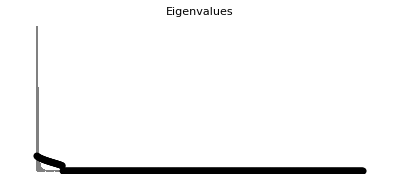
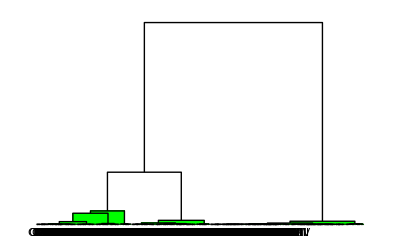
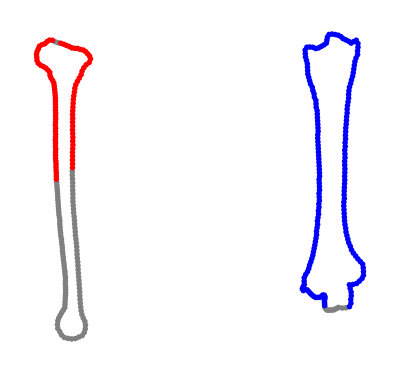
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 39.7607 |  | 
Relative Eigenvalue SD: 7.02877 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

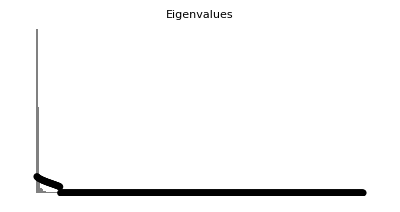
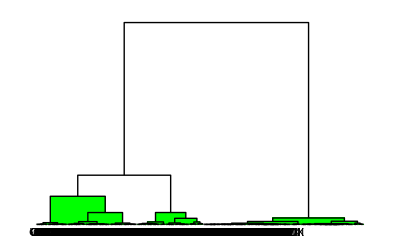
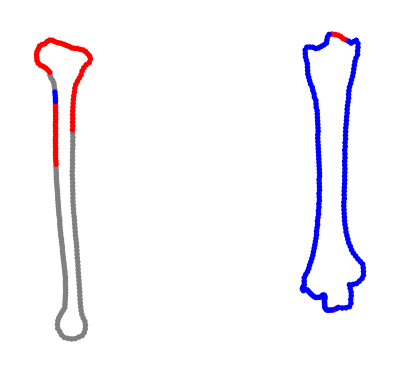
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 44.8559 |  | 
Relative Eigenvalue SD: 8.32954 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

### TIBIA/FEMUR

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[TibioProc1[[X]],NewFemurProc[[X]]]],{X,Length[TibioProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
FeTiFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
FeTiFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FemurTibioED=Join[fED,{ConstantArray[" ",4]},flED];
```

#### Mod

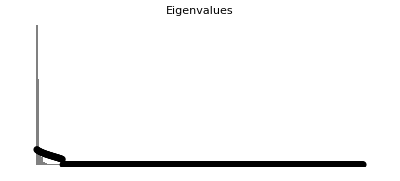
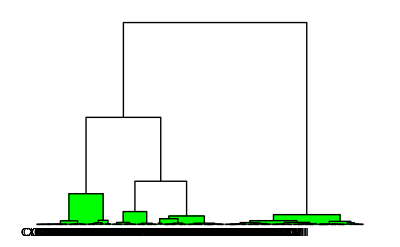
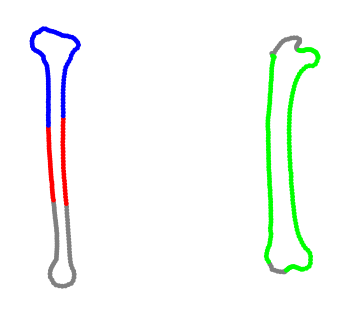
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 38.3255 |  | 
Relative Eigenvalue SD: 6.77505 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

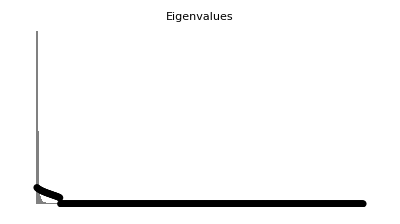
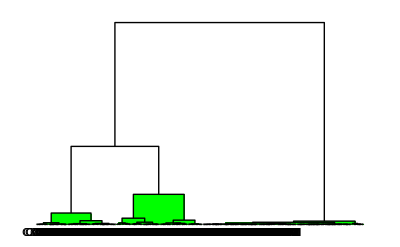
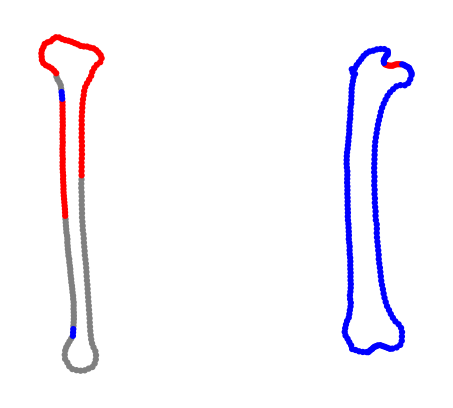
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 45.7205 |  | 
Relative Eigenvalue SD: 8.49009 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

### FEMUR/TARSO

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[TarsoProc1[[X]],NewFemurProc[[X]]]],{X,Length[TarsoProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
FeTaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
FeTaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FemurTarsoED=Join[fED,{ConstantArray[" ",4]},flED];
```

#### Mod

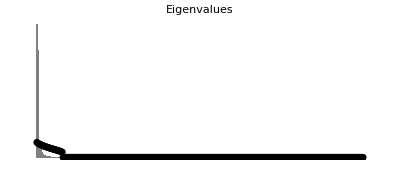
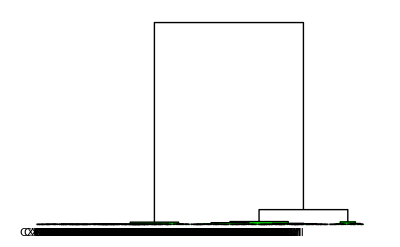
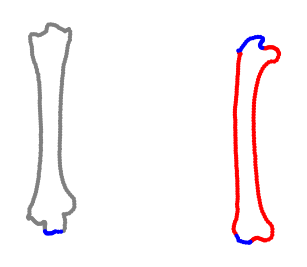
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 39.6202 |  | 
Relative Eigenvalue SD: 7.00393 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.174078 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

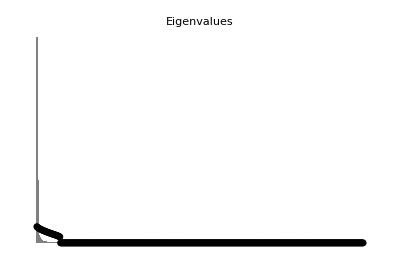
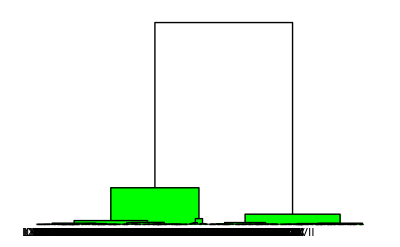
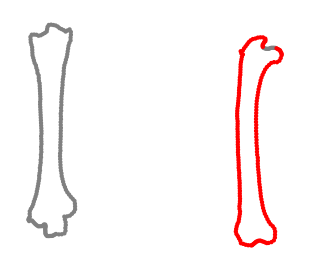
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 51.9712 |  | 
Relative Eigenvalue SD: 9.6508 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 2 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

### Whole HindLimb

#### Intro

```mathematica
HLlist=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@F]];
```

```mathematica
Labels=RomanNumeral[Range[1,600]];
```

```mathematica
(*X=1;
TarsoTibioProc=Table[Flatten[Append[TibioProc[[X]],NewTarsoProc[[X]]]],{X,Length[TibioProc]}];
X=1;
HindLimbProc=Table[Flatten[Append[TarsoTibioProc[[X]],NewFemurProc2[[X]]]],{X,Length[TarsoTibioProc]}];*)
```

```mathematica
X=1;
TarsoTibioProc=Table[Flatten[Append[TarsoProc1[[X]],NewTibioProc[[X]]]],{X,Length[TarsoProc1]}];
X=1;
HindLimbProc=Table[Flatten[Append[TarsoTibioProc[[X]],NewFemurProc2[[X]]]],{X,Length[TarsoTibioProc]}];
```

```mathematica
brokeoutlines=HindLimbProc;
```

```mathematica
FLBrokeoutlines=HindLimbProc[[flightless]];
FBrokeoutlines=HindLimbProc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,600,2,Labels,"RandomizationTest"];
HindLimbFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FHindLimbED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,600,2,Labels,"RandomizationTest"];
HindLimbFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLHindLimbED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
HindLimbED=Join[FHindLimbED,{ConstantArray[" ",4]},FLHindLimbED];
(*Export["EigenvalueDispersion_Tarso_Pairs.csv",TarsoTibioED,"CSV"]*)
(*TarsoTibioED//MatrixForm*)
```

#### Mod

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## ForeLimb

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
```

```mathematica
Labels=RomanNumeral[Range[1,400]];
```

### HUMERUS/ULNA

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[HumerusProc1[[X]],NewUlnaProc[[X]]]],{X,Length[HumerusProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
HuUlFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
HuUlFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
HumerusUlnaED=Join[fED,{ConstantArray[" ",4]},flED];
```

#### Mod

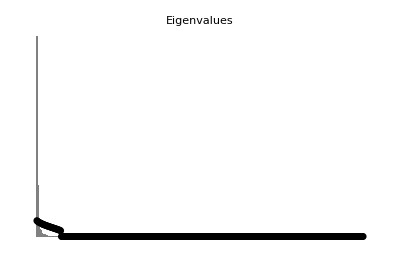
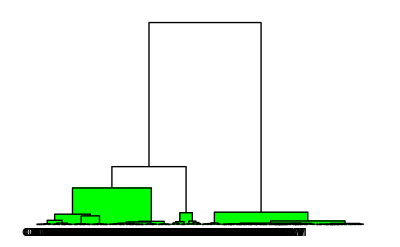
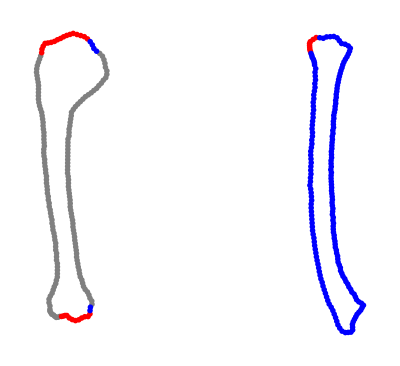
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 49.2048 |  | 
Relative Eigenvalue SD: 8.98352 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.179605 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

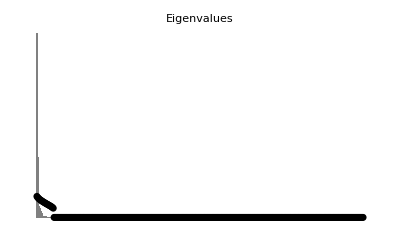
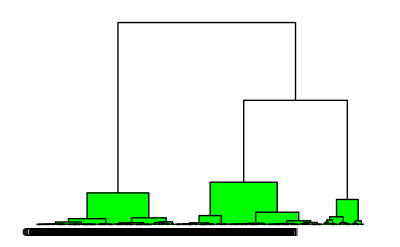
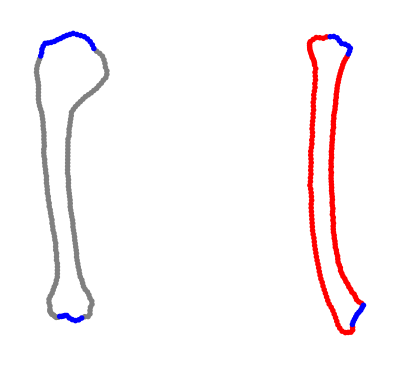
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 55.4657 |  | 
Relative Eigenvalue SD: 12.1036 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.213201 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

### ULNA/MANUS

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[ManusProc1[[X]],NewUlnaProc[[X]]]],{X,Length[ManusProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
UlMaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
UlMaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
ManusUlnaED=Join[fED,{ConstantArray[" ",4]},flED];
```

#### Mod

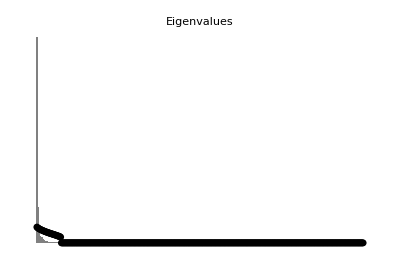
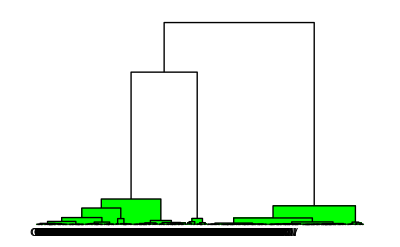
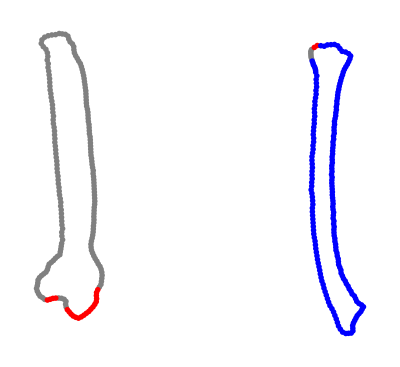
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 49.7693 |  | 
Relative Eigenvalue SD: 9.0866 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.179605 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

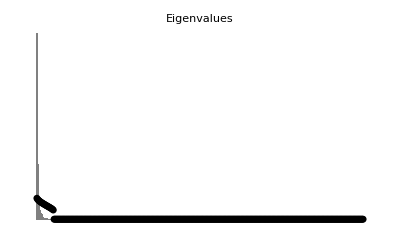
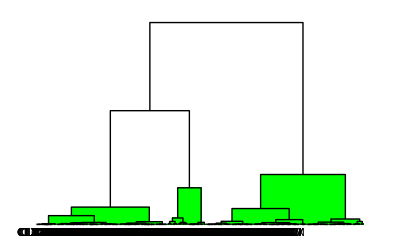
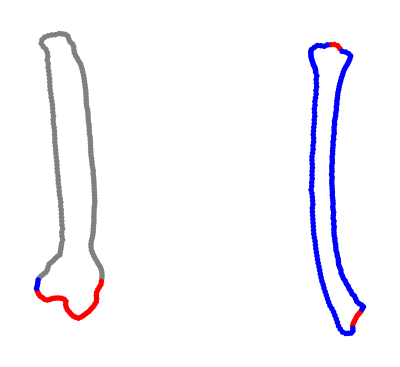
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 55.5198 |  | 
Relative Eigenvalue SD: 12.1154 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.213201 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FLMod
```

### MANUS/HUMERUS

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[ManusProc1[[X]],NewHumerusProc[[X]]]],{X,Length[ManusProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
HuMaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
HuMaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
ManusHumerusED=Join[fED,{ConstantArray[" ",4]},flED];
```

#### Mod

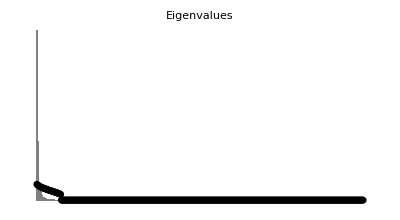
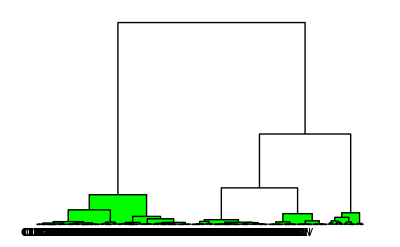
Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 43.0527 |  | 
Relative Eigenvalue SD: 7.86031 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.179605 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
FMod
```

```mathematica
FLMod
```

Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 49.5903 |  | 
Relative Eigenvalue SD: 10.8215 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.213201 |  | 
Estimated Number of Modules: 3 |  | 
-Graphics- | -Graphics- | -Graphics-

### Whole Forelimb

#### Intro

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
```

```mathematica
Labels=RomanNumeral[Range[1,600]];
```

```mathematica
X=1;
ManusUlnaProc=Table[Flatten[Append[ManusProc1[[X]],NewUlnaProc[[X]]]],{X,Length[ManusProc1]}];
```

```mathematica
X=1;
Proc=Table[Flatten[Append[ManusUlnaProc [[X]],NewHumerusProc2[[X]]]],{X,Length[ManusUlnaProc]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,600,2,Labels,"RandomizationTest"];
ForelimbFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
FLMod=Modularity[FLBrokeoutlines,600,2,Labels,"RandomizationTest"];
ForelimbFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
ForelimbED=Join[fED,{ConstantArray[" ",4]},flED];
```

#### Mod

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## RESULTS

```mathematica
(*Export["~/OneDrive/flying-flightless project 4.17.18/EigenvalueDispersion_Pairs_AllResults.csv",AllEDpairResults,"CSV"];*)
```

```mathematica
bones=Partition[{"HumerusUlna","ManusUlna","ManusHumerus", "FemurTibio","TarsoTibio","FemurTarso"},1];
AllEDPairs=Partition[{HumerusUlnaED,ManusUlnaED,ManusHumerusED,FemurTibioED,TarsoTibioED,FemurTarsoED},1];
X=1;
AllEDpairResults=Table[Join[{ConstantArray[" ",5]},{ConstantArray[" ",5]},{ConstantArray[bones[[X]],5]},{ConstantArray[" ",5]},AllEDPairs[[X]]],{X,Length[bones]}];
AllEDpairResultsNumbsOnly=Partition[Flatten[AllEDpairResults],5];
(*Export["EigenvalueDispersion_Pairs_AllResults.csv",AllEDpairResults,"CSV"]*)
(*AllEDpairResultsNumbsOnly//MatrixForm*)
```

```mathematica
(*AllEDResults={{HuUlFMod,HuUlFLMod},{UlMaFMod,UlMaFLMod},{HuMaFMod,HuMaFLMod},{FeTiFMod,FeTiFLMod},{TiTaFMod,TiTaFLMod},{FeTaFMod,FeTaFLMod}}*)
```

```mathematica
ForelimbFLMod
```

Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 73.2396 |  | 
Relative Eigenvalue SD: 15.9822 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.213201 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
ForelimbFMod
```

Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 66.7273 |  | 
Relative Eigenvalue SD: 12.1827 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.176777 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
HindLimbFLMod
```

Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 64.9291 |  | 
Relative Eigenvalue SD: 12.057 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.182574 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
HindLimbFMod
```

Modularity Results |  | 
Canonical Correlation |  | 
Eignvalue SD: 50.2982 |  | 
Relative Eigenvalue SD: 8.89156 |  | 
Expectation of Random Rel. Eigenvalue SD: 0.171499 |  | 
Estimated Number of Modules: 4 |  | 
-Graphics- | -Graphics- | -Graphics-

## Eigen Value Dispersion for 2B-PLS

## Intro

```mathematica
Labels=RomanNumeral[Range[1,400]];
```

```mathematica
PartProc=Table[Partition[TarsoProc[[X,2;;]],2],{X,Length[TarsoProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewTarsoProc=PartProc;
PartProc=Table[Partition[TibioProc[[X,2;;]],2],{X,Length[TibioProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewTibioProc=PartProc;
PartProc=Table[Partition[FemurProc[[X,2;;]],2],{X,Length[FemurProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewFemurProc=PartProc;
PartProc=Table[Partition[HumerusProc[[X,2;;]],2],{X,Length[HumerusProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewHumerusProc=PartProc;
PartProc=Table[Partition[UlnaProc[[X,2;;]],2],{X,Length[UlnaProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewUlnaProc=PartProc;
PartProc=Table[Partition[ManusProc[[X,2;;]],2],{X,Length[ManusProc]}];
X=1;
M=1;
PartProc=Table[Riffle[Table[PartProc[[X,M,1]]+0.2,{M,Length[PartProc[[1]]]}],Table[PartProc[[X,M,2]],{M,Length[PartProc[[1]]]}]],{X,Length[PartProc]}];
NewManusProc=PartProc;
```

```mathematica
TibioProc1=TibioProc[[1;;,2;;]];
TarsoProc1=TarsoProc[[1;;,2;;]];
FemurProc1=FemurProc[[1;;,2;;]];
HumerusProc1=HumerusProc[[1;;,2;;]];
UlnaProc1=UlnaProc[[1;;,2;;]];
ManusProc1=ManusProc[[1;;,2;;]];
```

```mathematica
<<HierarchicalClustering`
Modularity[Landmarks_,NLands_,NDims_,Labels_,Randomization_:"False"]:=Module[{superimposed,residuals,P2,EVStdev2,Plot2,NinetyFivePercentCutoff2,Tree2,EV2,BootEV2,MaxMinBootEV2,MeanBootEV1,MeanBootEV2,
Rows,Columns,dims,NumMods2,RelEVStdev2,ModulePicture},
superimposed=Landmarks;
superimposed=Partition[Partition[Flatten[superimposed],NDims],NLands];
{Rows,Columns,dims}=Dimensions[superimposed];
P2=CanonicalCorrelation[superimposed][[1;;200,201;;]];
EV2=Chop[Tr[SingularValueDecomposition[P2][[2]],List]];
EVStdev2=Sqrt[Plus@@((Tr[SingularValueDecomposition[P2][[2]],List]-Mean[Tr[SingularValueDecomposition[P2][[2]],List]])^2)/MatrixRank[P2]];
RelEVStdev2=Sqrt[Plus@@((Tr[SingularValueDecomposition[P2][[2]],List]-Mean[Tr[SingularValueDecomposition[P2][[2]],List]])^2)/MatrixRank[P2]]/Sqrt[MatrixRank[P2]];


If[Randomization=="RandomizationTest",
BootEV2=Table[Tr[SingularValueDecomposition[CanonicalCorrelation[Partition[superimposed[[#[[1]],#[[2]]]]&/@Flatten[ Table[Table[{RandomInteger[{1,Rows}],RandomInteger[{1,Columns}]},{Columns}],{Rows}],1],NLands]][[1;;200,201;;]]
][[2]],List]
,{100}];
MaxMinBootEV2=Chop[Transpose[{Max[#]&/@Transpose[BootEV2],Min[#]&/@Transpose[BootEV2]}]];
MeanBootEV2=Chop[Mean[#]&/@Transpose[BootEV2]];
NumMods2=Length[Select[EV2-(#[[1]]&/@MaxMinBootEV2),Positive]];
If[NumMods2==0,NumMods2=1];
Plot2=Graphics[{
{Gray,Table[Rectangle[{x-.45,0},{x+.45,EV2[[x]]}],{x,Length[EV2]}]},
{Black,AbsoluteThickness[2],Dashed,Table[Line[{{x,MaxMinBootEV2[[x,2]]},{x,MaxMinBootEV2[[x,1]]}}],{x,Length[MaxMinBootEV2]}]},
{Black,AbsolutePointSize[5],Table[Point[{x,MeanBootEV2[[x]]}],{x,Length[MeanBootEV2]}]}
},PlotLabel->"Eigenvalues"];
Tree2=DendrogramPlot[DirectAgglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&),HighlightLevel->NumMods2];

clust=Agglomerate[1-Abs[P2]->Labels,Linkage->"Ward"];
If[NumMods2>1,splitClusts=ClusterSplit[clust,NumMods2]];

If[NumMods2<2,
AllComas=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[clust],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[1<NumMods2<3,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[2<NumMods2<4,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[3<NumMods2<5,
AllComas1=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[1]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas2=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[2]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas3=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[3]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];
AllComas4=StringReplace[
Flatten[StringSplit[
{StringReplace[StringReplace[StringReplace[ToString[splitClusts[[4]]],"["->","],"]"->","],",,"->","]}
,","]]
," "->""];];

If[NumMods2<2,TipPos=Flatten[Position[AllComas,#]&/@Labels];
Tips=FromRomanNumeral[AllComas[[Sort[TipPos]]]];];

If[1<NumMods2<3,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
AllTips={Tips1,Tips2};
CorrectTips=AllTips;];

If[2<NumMods2<4,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
AllTips={Tips1,Tips2,Tips3};
CorrectTips=AllTips;];

If[3<NumMods2<5,TipPos1=Flatten[Position[AllComas1,#]&/@Labels];
Tips1=FromRomanNumeral[AllComas1[[Sort[TipPos1]]]];
TipPos2=Flatten[Position[AllComas2,#]&/@Labels];
Tips2=FromRomanNumeral[AllComas2[[Sort[TipPos2]]]];
TipPos3=Flatten[Position[AllComas3,#]&/@Labels];
Tips3=FromRomanNumeral[AllComas3[[Sort[TipPos3]]]];
TipPos4=Flatten[Position[AllComas4,#]&/@Labels];
Tips4=FromRomanNumeral[AllComas4[[Sort[TipPos4]]]];
AllTips={Tips1,Tips2,Tips3,Tips4};
CorrectTips=AllTips;];

If[NumMods2<2,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[Tips]]]}
}
]];
If[1<NumMods2<3,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]}
}
];];
If[2<NumMods2<4,ModulePicture=Graphics[
{
{Gray,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.01],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]}
}
];];
If[3<NumMods2<5,ModulePicture=Graphics[
{
{Gray,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[1]]]]]},{Red,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[2]]]]]},{Blue,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[3]]]]]},
{Green,PointSize[0.05],Point[Partition[brokeoutlines[[10]],2][[CorrectTips[[4]]]]]}
}
];];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eignvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{"Estimated Number of Modules: "<>ToString[NumMods2]},
(*{Plot2,Tree2,ModulePicture},*)
{Plot2,Tree2,ModulePicture}
},Alignment->Left],FontFamily->"Helvetica"]
]
,

Plot2=BarChart[EV2,PlotLabel->"Eigvenvalues"];
Tree2=DendrogramPlot[DirectAgglomerate[1-Abs[P2]->Labels,Linkage->"Ward"],LeafLabels->(#&)];
Return[Style[Grid[{
{Style["Modularity Results",FontWeight->Bold],""},
{Style["Canonical Correlation",FontSlant->Italic],""},
{"Eigenvalue SD: "<>ToString[EVStdev2]},
{"Relative Eigenvalue SD: "<>ToString[RelEVStdev2]},
{"Expectation of Random Rel. Eigenvalue SD: "<>ToString[Sqrt[1/Length[Landmarks]//N]]},
{Plot2,Tree2}
},Alignment->Left],FontFamily->"Helvetica"]
]
];
]
```

## HindLimb

```mathematica
HLlist=Union[Intersection[FemurLabelsList,TibioLabelsList, TarsoLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HLlist],#]]&/@F]];
```

### TARSO/TIBIA

#### Intro

```mathematica
X=1;
TarsoTibioProc=Table[Flatten[Append[TibioProc1[[X]],NewTarsoProc[[X]]]],{X,Length[TibioProc1]}];
```

```mathematica
brokeoutlines=TarsoTibioProc;
```

```mathematica
FLBrokeoutlines=TarsoTibioProc[[flightless]];
FBrokeoutlines=TarsoTibioProc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
TiTaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FTarsoTibioED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.774608,0.783054,0.787346,0.794054,0.790978,0.809007,0.829975,0.851866,0.876955,0.902787,0.928093,0.948261,0.967028,0.962012,0.944699,0.924783,0.913366,«18»,0.734737,0.763098,0.75127,0.702507,0.639795,0.614363,0.605734,0.60794,0.61514,0.644289,0.684033,0.72109,0.755422,0.781422,0.804746,«150»},«49»,«150»}→{«1»} at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.774608,0.783054,0.787346,0.794054,0.790978,0.809007,0.829975,0.851866,0.876955,0.902787,0.928093,0.948261,0.967028,0.962012,0.944699,0.924783,«19»,0.734737,0.763098,0.75127,0.702507,0.639795,0.614363,0.605734,0.60794,0.61514,0.644289,0.684033,0.72109,0.755422,0.781422,0.804746,«150»},«49»,«150»}→«1»,«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in «1».

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
TiTaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
FLTarsoTibioED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.32641,0.329647,0.328764,0.331989,0.335994,0.340219,0.346744,0.357137,0.369425,0.383881,0.403752,0.414103,0.423134,0.382738,0.325717,0.288859,«19»,0.379421,0.392146,0.383509,0.341055,0.313918,0.309926,0.354487,0.431236,0.528422,0.570029,0.550355,0.524671,0.485092,0.460568,0.43394,«150»},{«1»},«47»,{«1»},«150»}→«1» at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.32641,0.329647,0.328764,0.331989,0.335994,0.340219,0.346744,0.357137,0.369425,0.383881,0.403752,0.414103,0.423134,0.382738,0.325717,0.288859,«20»,0.392146,0.383509,0.341055,0.313918,0.309926,0.354487,0.431236,0.528422,0.570029,0.550355,0.524671,0.485092,0.460568,0.43394,«150»},«49»,«150»}→{«1»},«7»→…] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{«1»}→{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX,XXI,XXII,XXIII,XXIV,XXV,XXVI,XXVII,XXVIII,XXIX,XXX,XXXI,XXXII,XXXIII,XXXIV,XXXV,XXXVI,XXXVII,XXXVIII,XXXIX,XL,XLI,XLII,XLIII,XLIV,XLV,XLVI,XLVII,XLVIII,XLIX,L,«350»},Linkage→Ward].

```mathematica
TarsoTibioED=Join[FTarsoTibioED,{ConstantArray[" ",4]},FLTarsoTibioED];
(*Export["EigenvalueDispersion_Tarso_Pairs.csv",TarsoTibioED,"CSV"]*)
(*TarsoTibioED//MatrixForm*)
```

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

### TIBIA/FEMUR

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[TibioProc1[[X]],NewFemurProc[[X]]]],{X,Length[TibioProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
FeTiFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.826364,0.823463,0.820171,0.818314,0.81917,0.820332,0.819417,0.821176,0.822982,0.823611,0.823063,0.825146,0.824654,0.828411,0.830768,0.825969,0.83066,«18»,0.80832,0.804982,0.806287,0.809137,0.807915,0.798056,0.78842,0.781079,0.77738,0.773763,0.77603,0.775235,0.77528,0.771514,0.77191,«150»},{«1»},«48»,«150»}→«1» at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.826364,0.823463,0.820171,0.818314,0.81917,0.820332,0.819417,0.821176,0.822982,0.823611,0.823063,0.825146,0.824654,0.828411,0.830768,0.825969,«19»,0.80832,0.804982,0.806287,0.809137,0.807915,0.798056,0.78842,0.781079,0.77738,0.773763,0.77603,0.775235,0.77528,0.771514,0.77191,«150»},«49»,«150»}→{«1»},«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{{0.826364,0.823463,0.820171,0.818314,0.81917,0.820332,0.819417,0.821176,0.822982,0.823611,0.823063,0.825146,0.824654,0.828411,0.830768,0.825969,«19»,0.80832,0.804982,0.806287,0.809137,0.807915,0.798056,0.78842,0.781079,0.77738,0.773763,0.77603,0.775235,0.77528,0.771514,0.77191,«150»},{«1»},«47»,{«1»},«150»}→«1»,«1»].

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
FeTiFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.364516,0.362304,0.35903,0.363936,0.36489,0.370905,0.374732,0.380113,0.385759,0.388896,0.394202,0.407173,0.410362,0.410929,0.413642,0.413189,«19»,0.328993,0.326602,0.329535,0.328544,0.324522,0.324188,0.326269,0.33052,0.332295,0.332705,0.331679,0.331474,0.333866,0.338188,0.333615,«150»},{«19»,«50»},«48»,«150»}→{«1»} at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{«1»}→{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX,XXI,XXII,XXIII,XXIV,XXV,XXVI,XXVII,XXVIII,XXIX,XXX,XXXI,XXXII,XXXIII,XXXIV,XXXV,XXXVI,XXXVII,XXXVIII,XXXIX,XL,XLI,XLII,XLIII,XLIV,XLV,XLVI,XLVII,XLVIII,XLIX,L,«350»},Linkage→Ward] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{{0.364516,0.362304,0.35903,0.363936,0.36489,0.370905,0.374732,0.380113,0.385759,0.388896,0.394202,0.407173,0.410362,0.410929,0.413642,0.413189,«19»,0.328993,0.326602,0.329535,0.328544,0.324522,0.324188,0.326269,0.33052,0.332295,0.332705,0.331679,0.331474,0.333866,0.338188,0.333615,«150»},«49»,«150»}→«1»,«1»].

```mathematica
FemurTibioED=Join[fED,{ConstantArray[" ",4]},flED];
```

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

### FEMUR/TARSO

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[TarsoProc1[[X]],NewFemurProc[[X]]]],{X,Length[TarsoProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
FeTaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.948409,0.945476,0.942802,0.945942,0.952022,0.959162,0.959526,0.964784,0.966567,0.969561,0.972173,0.976449,0.977763,0.982682,0.986028,0.991995,0.997267,«18»,0.915475,0.912209,0.905193,0.901696,0.901764,0.900408,0.903882,0.898603,0.901231,0.910444,0.913412,0.915519,0.915173,0.913418,0.917241,«150»},«49»,«150»}→{«1»} at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.948409,0.945476,0.942802,0.945942,0.952022,0.959162,0.959526,0.964784,0.966567,0.969561,0.972173,0.976449,0.977763,0.982682,0.986028,0.991995,«19»,0.915475,0.912209,0.905193,0.901696,0.901764,0.900408,0.903882,0.898603,0.901231,0.910444,0.913412,0.915519,0.915173,0.913418,0.917241,«150»},«49»,«150»}→{«1»},«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{{0.948409,0.945476,0.942802,0.945942,0.952022,0.959162,0.959526,0.964784,0.966567,0.969561,0.972173,0.976449,0.977763,0.982682,0.986028,0.991995,«19»,0.915475,0.912209,0.905193,0.901696,0.901764,0.900408,0.903882,0.898603,0.901231,0.910444,0.913412,0.915519,0.915173,0.913418,0.917241,«150»},{«1»},«48»,«150»}→{«1»},«1»].

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
FeTaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.607842,0.61475,0.616533,0.626421,0.630281,0.638544,0.646333,0.653758,0.66306,0.669889,0.676476,0.691541,0.69547,0.696811,0.699878,0.699242,«19»,0.449845,0.429221,0.426825,0.41891,0.40969,0.401623,0.394382,0.385059,0.373051,0.363164,0.356831,0.354523,0.357893,0.367682,0.375222,«150»},{«1»},«47»,{«1»},«150»}→«1» at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.607842,0.61475,0.616533,0.626421,0.630281,0.638544,0.646333,0.653758,0.66306,0.669889,0.676476,0.691541,0.69547,0.696811,0.699878,0.699242,«20»,0.429221,0.426825,0.41891,0.40969,0.401623,0.394382,0.385059,0.373051,0.363164,0.356831,0.354523,0.357893,0.367682,0.375222,«150»},{«1»},«48»,«150»}→{«1»},«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{«1»}→{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX,XXI,XXII,XXIII,XXIV,XXV,XXVI,XXVII,XXVIII,XXIX,XXX,XXXI,XXXII,XXXIII,XXXIV,XXXV,XXXVI,XXXVII,XXXVIII,XXXIX,XL,XLI,XLII,XLIII,XLIV,XLV,XLVI,XLVII,XLVIII,XLIX,L,«350»},Linkage→Ward].

```mathematica
FemurTarsoED=Join[fED,{ConstantArray[" ",4]},flED];
```

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## ForeLimb

```mathematica
ForLlist=Union[Intersection[HumerusLabelsList,UlnaLabelsList, ManusLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@ForLlist],#]]&/@F]];
```

### HUMERUS/ULNA

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[HumerusProc1[[X]],NewUlnaProc[[X]]]],{X,Length[HumerusProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
HuUlFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.39634,0.390354,0.383619,0.392482,0.395641,0.396107,0.39937,0.403369,0.402615,0.401284,0.397384,0.398763,0.401167,0.411502,0.430974,0.443316,«19»,0.520009,0.518711,0.51078,0.499448,0.489927,0.490237,0.495766,0.49829,0.486991,0.470149,0.459303,0.450124,0.435932,0.429027,0.429054,«150»},{«1»},«47»,{«1»},«150»}→«1» at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.39634,0.390354,0.383619,0.392482,0.395641,0.396107,0.39937,0.403369,0.402615,0.401284,0.397384,0.398763,0.401167,0.411502,0.430974,0.443316,«20»,0.518711,0.51078,0.499448,0.489927,0.490237,0.495766,0.49829,0.486991,0.470149,0.459303,0.450124,0.435932,0.429027,0.429054,«150»},{«1»},«47»,{«1»},«150»}→«1»,«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{{0.39634,0.390354,0.383619,0.392482,0.395641,0.396107,0.39937,0.403369,0.402615,0.401284,0.397384,0.398763,0.401167,0.411502,0.430974,0.443316,«19»,0.520009,0.518711,0.51078,0.499448,0.489927,0.490237,0.495766,0.49829,0.486991,0.470149,0.459303,0.450124,0.435932,0.429027,0.429054,«150»},«50»}→{«1»},«1»].

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
HuUlFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.310376,0.30499,0.301422,0.291305,0.285845,0.285778,0.284095,0.283178,0.28111,0.276132,0.272779,0.270445,0.268136,0.267457,0.267803,0.266443,«19»,0.342067,0.334735,0.335701,0.331661,0.321281,0.309794,0.308737,0.302364,0.300836,0.301286,0.30132,0.311576,0.31542,0.314047,0.31444,«150»},«49»,«150»}→{«1»} at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.310376,0.30499,0.301422,0.291305,0.285845,0.285778,0.284095,0.283178,0.28111,0.276132,0.272779,0.270445,0.268136,0.267457,0.267803,0.266443,«20»,0.334735,0.335701,0.331661,0.321281,0.309794,0.308737,0.302364,0.300836,0.301286,0.30132,0.311576,0.31542,0.314047,0.31444,«150»},«49»,«150»}→«1»,«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{{0.310376,0.30499,0.301422,0.291305,0.285845,0.285778,0.284095,0.283178,0.28111,0.276132,0.272779,0.270445,0.268136,0.267457,0.267803,0.266443,«20»,0.334735,0.335701,0.331661,0.321281,0.309794,0.308737,0.302364,0.300836,0.301286,0.30132,0.311576,0.31542,0.314047,0.31444,«150»},{«1»},«48»,«150»}→«1»,«1»].

```mathematica
HumerusUlnaED=Join[fED,{ConstantArray[" ",4]},flED];
```

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

### ULNA/MANUS

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[ManusProc1[[X]],NewUlnaProc[[X]]]],{X,Length[ManusProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
UlMaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.244878,0.2442,0.241806,0.238833,0.236559,0.237246,0.240313,0.242383,0.2444,0.245188,0.247904,0.249455,0.254742,0.258225,0.270529,0.283435,«19»,0.381552,0.378715,0.380385,0.37511,0.373428,0.372447,0.376019,0.374459,0.369394,0.364079,0.362137,0.358586,0.350167,0.346453,0.339603,«150»},«49»,«150»}→{«1»} at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.244878,0.2442,0.241806,0.238833,0.236559,0.237246,0.240313,0.242383,0.2444,0.245188,0.247904,0.249455,0.254742,0.258225,0.270529,0.283435,«20»,0.378715,0.380385,0.37511,0.373428,0.372447,0.376019,0.374459,0.369394,0.364079,0.362137,0.358586,0.350167,0.346453,0.339603,«150»},«49»,«150»}→{«1»},«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in «1».

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
UlMaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.550192,0.558883,0.580851,0.589022,0.600105,0.604673,0.607173,0.617393,0.625428,0.632501,0.641581,0.650937,0.656923,0.660357,0.66723,0.671398,0.68751,«18»,0.82413,0.832363,0.835476,0.834874,0.840865,0.846935,0.850936,0.845097,0.848767,0.843615,0.830591,0.818742,0.809324,0.805743,0.797027,«150»},«49»,«150»}→{«1»} at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.550192,0.558883,0.580851,0.589022,0.600105,0.604673,0.607173,0.617393,0.625428,0.632501,0.641581,0.650937,0.656923,0.660357,0.66723,0.671398,«19»,0.82413,0.832363,0.835476,0.834874,0.840865,0.846935,0.850936,0.845097,0.848767,0.843615,0.830591,0.818742,0.809324,0.805743,0.797027,«150»},«49»,«150»}→«1»,«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{{0.550192,0.558883,0.580851,0.589022,0.600105,0.604673,0.607173,0.617393,0.625428,0.632501,0.641581,0.650937,0.656923,0.660357,0.66723,0.671398,«19»,0.82413,0.832363,0.835476,0.834874,0.840865,0.846935,0.850936,0.845097,0.848767,0.843615,0.830591,0.818742,0.809324,0.805743,0.797027,«150»},{«1»},«48»,«150»}→«1»,«1»].

```mathematica
ManusUlnaED=Join[fED,{ConstantArray[" ",4]},flED];
```

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

### MANUS/HUMERUS

#### Intro

```mathematica
X=1;
Proc=Table[Flatten[Append[ManusProc1[[X]],NewHumerusProc[[X]]]],{X,Length[ManusProc1]}];
```

```mathematica
brokeoutlines=Proc;
```

```mathematica
FLBrokeoutlines=Proc[[flightless]];
FBrokeoutlines=Proc[[flighted]];
```

```mathematica
FMod=Modularity[FBrokeoutlines,400,2,Labels,"RandomizationTest"];
HuMaFMod=FMod;
mod=FMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flying",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
fED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.535207,0.540288,0.54219,0.536485,0.530094,0.530492,0.530542,0.528941,0.542307,0.561985,0.576823,0.595771,0.604983,0.609701,0.628599,0.660177,0.696058,«18»,0.517663,0.522405,0.528035,0.540404,0.552567,0.563103,0.578029,0.590199,0.601074,0.611144,0.62097,0.633226,0.645329,0.655691,0.666607,«150»},«49»,«150»}→{«1»} at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.535207,0.540288,0.54219,0.536485,0.530094,0.530492,0.530542,0.528941,0.542307,0.561985,0.576823,0.595771,0.604983,0.609701,0.628599,0.660177,«19»,0.517663,0.522405,0.528035,0.540404,0.552567,0.563103,0.578029,0.590199,0.601074,0.611144,0.62097,0.633226,0.645329,0.655691,0.666607,«150»},«49»,«150»}→«1»,«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in «1».

Part::partw: Part 3 of ClusterSplit[Agglomerate[{{0.535207,0.540288,0.54219,0.536485,0.530094,0.530492,0.530542,0.528941,0.542307,0.561985,0.576823,0.595771,0.604983,0.609701,0.628599,0.660177,«20»,0.522405,0.528035,0.540404,0.552567,0.563103,0.578029,0.590199,0.601074,0.611144,0.62097,0.633226,0.645329,0.655691,0.666607,«150»},«49»,«150»}→{«1»},«7»→…],3] does not exist.

```mathematica
FLMod=Modularity[FLBrokeoutlines,400,2,Labels,"RandomizationTest"];
HuMaFLMod=FLMod;
mod=FLMod[[1,1,3;;6]];
M=1;
X=1;
getElmnts=Transpose[Table[Table[StringSplit[mod[[X,M]],":"],{X,Length[mod]}],{M,Length[mod[[1]]]}]];
getElmnts=Partition[Flatten[getElmnts],2][[1;;,2]];
getColumnTitles=Partition[Flatten[StringSplit[#,":"]&/@mod],2][[1;;,1]];
NewMod=Join[{ConstantArray["Flightless",4]},{getColumnTitles},getElmnts];
X=1;
M=1;
flED=Partition[Flatten[Table[NewMod[[X]],{X,Length[NewMod]}]],4];
```

DirectAgglomerate::matsq: Argument {{0.914473,0.926619,0.944095,0.963906,0.999753,0.934141,0.838888,0.742196,0.683673,0.641831,0.599432,0.571251,0.606609,0.718843,0.821614,0.894324,0.943995,«18»,0.939671,0.939581,0.934021,0.927844,0.920196,0.917146,0.913518,0.908177,0.905349,0.903577,0.897616,0.893471,0.888076,0.887499,0.886326,«150»},«49»,«150»}→{«1»} at position 1 is not a non-empty square matrix.

DendrogramPlot::arg1: DirectAgglomerate[{{0.914473,0.926619,0.944095,0.963906,0.999753,0.934141,0.838888,0.742196,0.683673,0.641831,0.599432,0.571251,0.606609,0.718843,0.821614,0.894324,«19»,0.939671,0.939581,0.934021,0.927844,0.920196,0.917146,0.913518,0.908177,0.905349,0.903577,0.897616,0.893471,0.888076,0.887499,0.886326,«150»},«49»,«150»}→{«1»},«1»] is not a list of elements, a Cluster object, or a rule mapping data elements to labels.

Agglomerate::list: List expected at position 1 in Agglomerate[{{0.914473,0.926619,0.944095,0.963906,0.999753,0.934141,0.838888,0.742196,0.683673,0.641831,0.599432,0.571251,0.606609,0.718843,0.821614,0.894324,«19»,0.939671,0.939581,0.934021,0.927844,0.920196,0.917146,0.913518,0.908177,0.905349,0.903577,0.897616,0.893471,0.888076,0.887499,0.886326,«150»},{«1»},«48»,«150»}→{«1»},«1»].

```mathematica
ManusHumerusED=Join[fED,{ConstantArray[" ",4]},flED];
```

```mathematica
(*FMod*)
```

```mathematica
(*FLMod*)
```

## RESULTS

```mathematica
(*Export["~/OneDrive/flying-flightless project 4.17.18/EigenvalueDispersion_Pairs_AllResults.csv",AllEDpairResults,"CSV"];*)
```

```mathematica
bones=Partition[{"HumerusUlna","ManusUlna","ManusHumerus", "FemurTibio","TarsoTibio","FemurTarso"},1];
AllEDPairs=Partition[{HumerusUlnaED,ManusUlnaED,ManusHumerusED,FemurTibioED,TarsoTibioED,FemurTarsoED},1];
X=1;
AllEDpairResults=Table[Join[{ConstantArray[" ",5]},{ConstantArray[" ",5]},{ConstantArray[bones[[X]],5]},{ConstantArray[" ",5]},AllEDPairs[[X]]],{X,Length[bones]}];
AllEDpairResultsNumbsOnly=Partition[Flatten[AllEDpairResults],5];
(*Export["EigenvalueDispersion_Pairs_AllResults.csv",AllEDpairResults,"CSV"]*)
(*AllEDpairResultsNumbsOnly//MatrixForm*)
```

```mathematica
(*AllEDpairResults={{HuUlFMod,HuUlFLMod},{UlMaFMod,UlMaFLMod},{HuMaFMod,HuMaFLMod},{FeTiFMod,FeTiFLMod},{TiTaFMod,TiTaFLMod},{FeTaFMod,FeTaFLMod}}*)
```

```mathematica
Partition[Flatten[{TarsoTibioED,FemurTibioED,FemurTarsoED}],4]//MatrixForm
```

(Flying | Flying | Flying | Flying
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 8.20701 |  1.45081 |  0.171499 |  2
  |   |   |  
Flightless | Flightless | Flightless | Flightless
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 14.6577 |  2.72187 |  0.182574 |  2
Flying | Flying | Flying | Flying
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 11.7889 |  2.08401 |  0.171499 |  2
  |   |   |  
Flightless | Flightless | Flightless | Flightless
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 15.9069 |  2.95384 |  0.182574 |  2
Flying | Flying | Flying | Flying
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 5.7207 |  1.01129 |  0.171499 |  2
  |   |   |  
Flightless | Flightless | Flightless | Flightless
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 18.4293 |  3.42224 |  0.182574 |  1)

```mathematica
Partition[Flatten[{HumerusUlnaED,ManusUlnaED,ManusHumerusED}],4]//MatrixForm
```

(Flying | Flying | Flying | Flying
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 19.0641 |  3.48061 |  0.176777 |  2
  |   |   |  
Flightless | Flightless | Flightless | Flightless
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 21.1223 |  4.60926 |  0.213201 |  2
Flying | Flying | Flying | Flying
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 21.552 |  3.93483 |  0.176777 |  1
  |   |   |  
Flightless | Flightless | Flightless | Flightless
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 21.2143 |  4.62933 |  0.213201 |  2
Flying | Flying | Flying | Flying
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 16.1427 |  2.94723 |  0.176777 |  3
  |   |   |  
Flightless | Flightless | Flightless | Flightless
Eignvalue SD | Relative Eigenvalue SD | Expectation of Random Rel. Eigenvalue SD | Estimated Number of Modules
 12.2103 |  2.6645 |  0.213201 |  2)

## Femur vs Humerus 2 B PLS

## Femur

```mathematica
FemurData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/FOR_PCA_Danny_Final_FFSteamerDuck_All_FemursLM.TPS"];
labels=FemurData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
FemurData=FemurData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=FemurData[[1,1;;,2;;]];
outline=FemurData[[2,1;;,2;;]];
labels=FemurData[[1,1;;,1]];
labelss=labels;
FemurLabels=labels;
M=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[M]],2],Partition[landmarks[[M]],2],{69,8,6,69,25, 23}]],{M,Length[outline]}];shortlabels=StringSplit[#,"_"][[1]]&/@labels;

shortPos=Flatten[Position[FemurLabelsList,#]]&/@FemurVSHumerusList;
shortPos=shortPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@shortPos;
labelsfew=FemurLabels[[#]]&/@shortPos;
shortLabels=StringSplit[#,"_"][[1]]&/@labelsfew;
pos=Flatten[Position[shortLabels,#]]&/@Union[shortLabels];
means2=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
FemurProc=Procrustes[means2, 200, 2];
CPCAFemurProc=FemurProc;
FemurProc=Table[Prepend[FemurProc[[x]],Union[shortlabels][[x]]],{x,Length[FemurProc]}];
```

## Humerus

```mathematica
HumerusData=tpsImport["/Users/spencerhellert/OneDrive/flying-flightless project 4.17.18/TPS files Dec. 11 2017/TPS files Dec. 11 2017 2/For_PCA_Danny_Final_FFSteamerDuck_All_HumerusLM.TPS"];labels=HumerusData[[1,1;;,1]];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;
HumerusData=HumerusData[[1;;,Sort[Flatten[Flatten[Position[shortlabels,#]]&/@AllTaxaList]]]];
landmarks=HumerusData[[1,1;;,2;;]];
outline=HumerusData[[2,1;;,2;;]];
labels=HumerusData[[1,1;;,1]];
labelss=labels;
HumerusLabels=labels;
x=1;
brokeoutlines=Table[Flatten[BreakOutline[Partition[outline[[x]],2],Partition[landmarks[[x]],2],{12,70,15,14,89}]],{x,Length[outline]}];
shortlabels=StringSplit[#,"_"][[1]]&/@labels;

HumerusPos=Flatten[Position[HumerusLabelsList,#]]&/@FemurVSHumerusList;
HumerusPos=HumerusPos[[1;;,1]];
brokeoutlines1=brokeoutlines[[#]]&/@HumerusPos;
Humeruslabelsfew=HumerusLabels[[#]]&/@HumerusPos;
shortHumerusLabels=StringSplit[#,"_"][[1]]&/@Humeruslabelsfew;
pos=Flatten[Position[shortHumerusLabels,#]]&/@Union[shortHumerusLabels];
means2=Mean[Procrustes[brokeoutlines1[[#]],200,2]]&/@pos;
HumerusProc=Procrustes[means2, 200, 2];
CPCAHumerusProc=HumerusProc;
HumerusProc=Table[Prepend[HumerusProc[[x]],Union[shortHumerusLabels][[x]]],{x,Length[HumerusProc]}];
```

## Intro

```mathematica
TwoBlockPLSScoresOnly[Data1_,Data2_,Mode_,PLS_:1]:=Module[{Y1,Y2,N1,N2,R12,F1,Dmat,F2,Z1,Z2,con1,con2,corrs,output,labels1,labels2,ScoresToPlot},

labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];

Which[

Mode=={"Shape","Shape"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2,

Mode=={"Shape","Standardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Standardize[Y2],


Mode=={"Shape","Unstandardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Y2,

Mode=={"Standardized","Standardized"},
Y1=Standardize[Y1];
Y2=Standardize[Y1],

Mode=={"Unstandardized","Standardized"},
Y1=Y1;
Y2=Standardize[Y2],

Mode=={"Unstandardized","Unstandardized"},
Y1=Y1;
Y2=Y2,

Mode==Mode,Return["Mode must be {\"Shape\",\"Shape\"},{\"Shape\",\"Standardized\"}, {\"Shape\",\"Unstandardized\"}, {\"Standardized\",\"Standardized\"}, {\"UnStandardized\",\"Standardized\"}, or  {\"Unstandardized\",\"Unstandardized\"}."];];

N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
R12=Covariance[Y1,Y2];
{F1,Dmat,F2}=SingularValueDecomposition[R12];
Dmat=Tr[Dmat,List];
Z1=Y1.F1;
Z2=Y2.F2;

corrs=Table[Correlation[Z1[[1;;,i]],Z2[[1;;,i]]],{i,Length[Dmat]}];
Which[
Mode=={"Shape","Shape"},output=GraphicsGrid[{{tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],tpSpline[con2,con2+F2[[1;;,PLS]]*Max[Z2[[1;;,PLS]]]]}},ImageSize->500,BaseStyle->{FontFamily->"Arial",FontSize->10},PlotLabel->"Positive End of PLS "<>ToString[PLS]],

Mode=={"Shape","Standardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Shape","Unstandardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Standardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Unstandardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]}];

ScoresToPlot=Transpose[{Z1[[1;;,PLS]],Z2[[1;;,PLS]]}];

Return[{Z1,Z2}]];
```

## 2 B PLS

### Intro

```mathematica
HFlist=Union[Intersection[FemurLabelsList,HumerusLabelsList][[1;;,1]]];
flightless=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HFlist],#]]&/@FL]];
HindLimbflightless=flightless;
flighted=Sort[Flatten[Flatten[Position[Union[StringSplit[#,"_"][[1]]&/@HFlist],#]]&/@F]];
HindLimbflighted=flighted;
```

```mathematica
(*Hindlimb -regular*)
TwoBlockPartialLeastSquares[Data1_,Data2_,Mode_,PLS_:1]:=Module[{Y1,Y2,N1,N2,R12,F1,Dmat,F2,Z1,Z2,con1,con2,corrs,output,labels1,labels2,ScoresToPlot},

labels1=Data1[[1;;,1]];
labels2=Data2[[1;;,1]];
Y1=Data1[[1;;,2;;]];
Y2=Data2[[1;;,2;;]];

Which[

Mode=={"Shape","Shape"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
con2=Mean[Y2];
Y2=#-con2&/@Y2,

Mode=={"Shape","Standardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Standardize[Y2],


Mode=={"Shape","Unstandardized"},
con1=Mean[Y1];
Y1=#-con1&/@Y1;
Y2=Y2,

Mode=={"Standardized","Standardized"},
Y1=Standardize[Y1];
Y2=Standardize[Y1],

Mode=={"Unstandardized","Standardized"},
Y1=Y1;
Y2=Standardize[Y2],

Mode=={"Unstandardized","Unstandardized"},
Y1=Y1;
Y2=Y2,

Mode==Mode,Return["Mode must be {\"Shape\",\"Shape\"},{\"Shape\",\"Standardized\"}, {\"Shape\",\"Unstandardized\"}, {\"Standardized\",\"Standardized\"}, {\"UnStandardized\",\"Standardized\"}, or  {\"Unstandardized\",\"Unstandardized\"}."];];


N1=Plus@@Variance[Y1];
N2=Plus@@Variance[Y2];
R12=Covariance[Y1,Y2];
{F1,Dmat,F2}=SingularValueDecomposition[R12];
Dmat=Tr[Dmat,List];
Z1=Y1.F1;
Z2=Y2.F2;

corrs=Table[Correlation[Z1[[1;;,i]],Z2[[1;;,i]]],{i,Length[Dmat]}];
Which[
Mode=={"Shape","Shape"},output=GraphicsGrid[{{tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],tpSpline[con2,con2+F2[[1;;,PLS]]*Max[Z2[[1;;,PLS]]]]}},ImageSize->500,BaseStyle->{FontFamily->"Arial",FontSize->10},PlotLabel->"Positive End of PLS "<>ToString[PLS]],

Mode=={"Shape","Standardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Shape","Unstandardized"},output={tpSpline[con1,con1+F1[[1;;,PLS]]*Max[Z1[[1;;,PLS]]]],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Standardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Standardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]},

Mode=={"Unstandardized","Unstandardized"},output={TableForm[Append[NumberForm[#,{4,4}]&/@F1[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels1,"Corr"],{"PLS"}}],TableForm[Append[NumberForm[#,{4,4}]&/@F2[[1;;,PLS]],NumberForm[corrs[[PLS]],{3,2}]],TableHeadings->{Append[labels2,"Corr"],{"PLS"}}]}];

ScoresToPlot=Transpose[{Z1[[1;;,PLS]],Z2[[1;;,PLS]]}];

Return[{

"Proportion of Actual Squared Covariance Explained by PLS "<>ToString[PLS]<>":  "<>ToString[NumberForm[((Dmat^2)/(Plus@@(Dmat^2)))[[PLS]],{3,2}]],

"Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  "<>ToString[NumberForm[(Plus@@(Dmat^2))/(N1*N2),{3,2}]],

flightless=Sort[Flatten[Flatten[Position[Union[Intersection[FemurLabelsList,HumerusLabelsList][[1;;,1]]],#]]&/@FL]];
flighted=Sort[Flatten[Flatten[Position[Union[Intersection[FemurLabelsList,HumerusLabelsList][[1;;,1]]],#]]&/@F]];

pts1={PointSize[0.01],Blue,Point[#]}&/@ScoresToPlot[[flightless]];
pts2={PointSize[0.01],Orange,Point[#]}&/@ScoresToPlot[[flighted]];

Graphics[{{pts1,pts2},{Table[Text[labels1[[x]],ScoresToPlot[[x]],{0,1}],{x,Length[labels1]}]}},AspectRatio->1/GoldenRatio,Axes->False,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->10},ImageSize->400,FrameLabel->{"Data 1, PLS "<>ToString[PLS],"Data 2, PLS "<>ToString[PLS]}],

output

}//TableForm];];
```

### Femur/Humerus

```mathematica
TwoBlockPartialLeastSquares[HumerusProc,FemurProc,{"Shape", "Shape"}]
```

Proportion of Actual Squared Covariance Explained by PLS 1:  0.96
Proportion of Total Possible Squared Covariance Explained by All PLS Axes:  0.10
-Graphics-
-Graphics-

```mathematica
{scoresHumerus,scoresFemur}=TwoBlockPLSScoresOnly[HumerusProc,FemurProc,{"Shape", "Shape"}];RegressionData=Transpose[{scoresHumerus[[1;;,1]],scoresFemur[[1;;,1]]}];
Clear[x];
lm=LinearModelFit[RegressionData,{1,x},x];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x];
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x];
Show[ListPlot[{RegressionData[[flightless]],RegressionData[[flighted]]}, AspectRatio->1/GoldenRatio,Frame->True, Axes->False,PlotLegends->{"Flightless","Volant"}],Plot[lmflight[T],{T,-0.25,0.25}, PlotStyle->Orange],Plot[lmflightless[T],{T,-0.25,0.25}, PlotStyle->Blue]]
bootdiffs=Table[bootdata=RandomSample[Transpose[{RandomSample[scoresFemur[[1;;,1]]],RandomSample[scoresHumerus[[1;;,1]]]}]];
lmflightless=LinearModelFit[bootdata[[flightless]],{1,x},x]["BestFitParameters"][[2]];
lmflight=LinearModelFit[bootdata[[flighted]],{1,x},x]["BestFitParameters"][[2]];lmflightless-lmflight,{5000}];
lmflightless=LinearModelFit[RegressionData[[flightless]],{1,x},x]["BestFitParameters"][[2]]
lmflight=LinearModelFit[RegressionData[[flighted]],{1,x},x]["BestFitParameters"][[2]]
lmflightless-lmflight
Show[Histogram[bootdiffs],Graphics[Line[{{lmflightless-lmflight,0},{lmflightless-lmflight,100}}]]]
N[Length[Select[bootdiffs,#≥lmflight-lmflightless&]]/5000]
```

-Graphics-

0.228554

0.282654

-0.0541006

-Graphics-

0.4412